```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
QuickExport:=Export[#,%,ImageResolution->300]&
```

```mathematica
checkers=Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
grid={EdgeForm[{Thin}],FaceForm[Transparent],#}&/@checkers;
blacks=Take[checkers,{1,-1,2}];
whites={White,#}&/@Drop[checkers,{1,-1,2}];
```

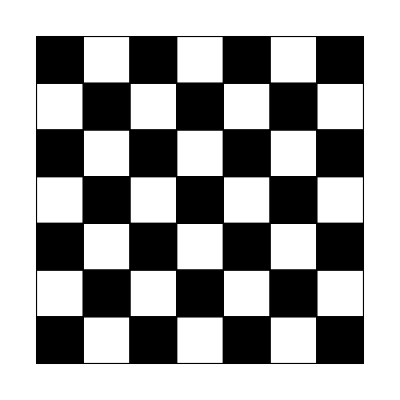

```mathematica
Graphics@{grid,blacks}
```

```mathematica
Export["Checkerboard.png",Graphics@{grid,blacks}]
```

Checkerboard.png

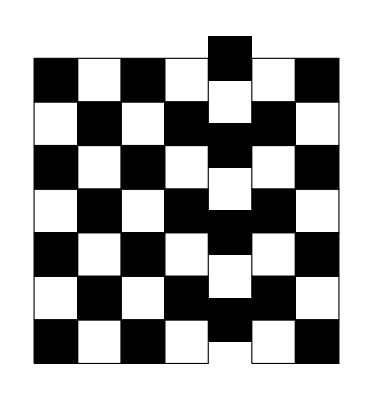

CheckerboardAperiodic.png

```mathematica
newgrid=Complement[grid,Cases[grid,{EdgeForm[{Thickness[Tiny]}],FaceForm[-Graphics-],Translate[Rectangle[{0,0}],{4,_}]}]];
Translate[#,{0,0.5}]&/@Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]];
Complement[blacks,Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]]];
Graphics[{newgrid,%%,%}]
Export["CheckerboardAperiodic.png",%]
```

```mathematica
Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
newblacks=Take[%,{1,-1,3}];
```

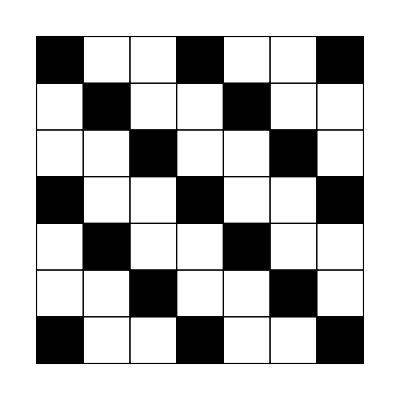

CheckerboardOther.png

```mathematica
Graphics@{grid,newblacks}
Export["CheckerboardOther.png",%]
```

```mathematica
circles=Flatten[Table[Translate[Disk[],{i,j}],{i,0,7,2},{j,0,7,2}],1];
```

```mathematica
Rotate[Graphics[{FaceForm[Black],#}&/@circles],Pi/4];
Graphics[Rotate[circles,Pi/4]]
Table[Graphics[Translate[Rotate[circles,Pi/4],{0,i*2Sqrt[2]}]],{i,-2,1}];
Show[{%,%%},PlotRange->{{-2.3,8.3},{-3.75,6.85}}]
Export["CheckerboardCircles.png",%]
```

-Graphics-

-Graphics-

CheckerboardCircles.png

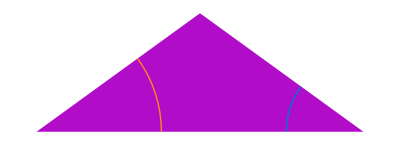

RobinsonFat.png

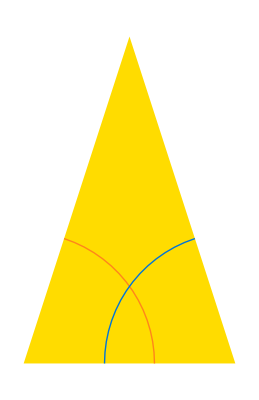

RobinsonSkinny.png

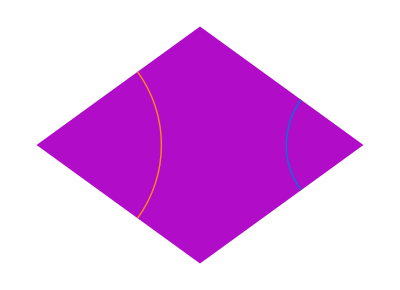

RhombFat.png

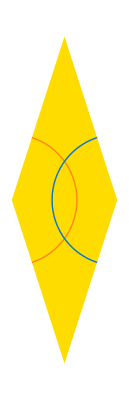

RhombSkinny.png

```mathematica
Show[See@{unitfat},Graphics[MakeCurveRules/@Inflate[{unitfat},0]]]
Export["RobinsonFat.png",%,Background->None,ImageResolution->200]
Show[See@{unitskinny},Graphics[MakeCurveRules/@Inflate[{unitskinny},0]]]
Export["RobinsonSkinny.png",%,Background->None,ImageResolution->200]
Show[See@AddConj@{unitfat},Graphics[MakeCurveRules/@AddConj@Inflate[{unitfat},0]]]
Export["RhombFat.png",%,Background->None,ImageResolution->200]
Show[See@AddConj@{unitskinny},Graphics[MakeCurveRules/@AddConj@Inflate[{unitskinny},0]]]
Export["RhombSkinny.png",%,Background->None,ImageResolution->200]
```

```mathematica
rhombfatunit=Rotate[Polygon/@Coor/@First/@Rhomb/@{unitfat},Pi/5];
rhombskinnyunit=Rotate[Polygon/@Coor/@First/@Rhomb/@{unitskinny},2Pi/5];

rhombfatgrid=Flatten[Table[Translate[rhombfatunit,{i,j}],{i,0,6},{j,0,6,2*0.951}],1];
rhombskinnygrid=Translate[Flatten[Table[Translate[rhombskinnyunit,{i,j}],{i,0,6,ϕ},{j,0.951,6,2*0.951}],1],{0.8,0}];

fatrules=Rotate[MakeCurveRules/@AddConj@Inflate[{unitfat},0],Pi/5];
fatrulesgrid=Flatten[Table[Translate[fatrules,{i,j}],{i,0,6},{j,0,6,2*0.951}],1];

skinnyrules=Rotate[MakeCurveRules/@AddConj@Inflate[{unitskinny},0],2Pi/5];
skinnyrulesgrid=Translate[Flatten[Table[Translate[skinnyrules,{i,j}],{i,0,6,ϕ},{j,0.951,6,2*0.951}],1],{0.8,0}];

Show[Graphics[{FaceForm[None],EdgeForm[Black],rhombfatgrid}],
Graphics[{FaceForm[None],EdgeForm[Black],rhombskinnygrid}],PlotRange->{{-1,7.3},{-0.6,6.5}}]
Export["RhombPeriodic.png",%,Background->None,ImageResolution->200]

Show[Graphics[{FaceForm[None],EdgeForm[Black],rhombfatgrid}],
Graphics[{FaceForm[None],EdgeForm[Black],rhombskinnygrid}],Graphics[fatrulesgrid],Graphics[skinnyrulesgrid],PlotRange->{{-1,7.3},{-0.6,6.5}}]
Export["RhombPeriodicRules.png",%,Background->None,ImageResolution->200]
```

-Graphics-

RhombPeriodic.png

-Graphics-

RhombPeriodicRules.png

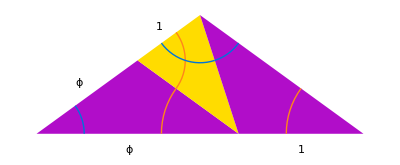

RobFatSub.png

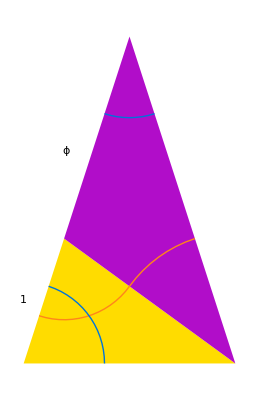

RobSkinnySub.png

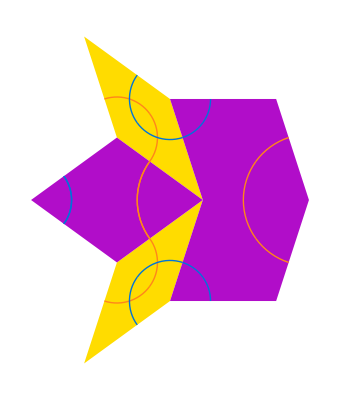

RhombFatSub.png

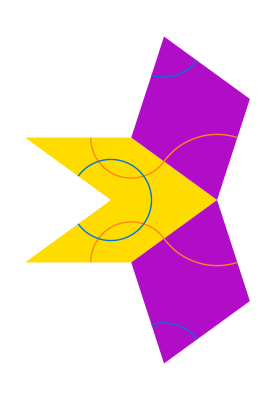

RhombSkinnySub.png

RobFatSub.png

-Graphics-

RobSkinnySub.png

-Graphics-

RhombFatSub.png

-Graphics-

RhombSkinnySub.png

```mathematica
Show[See@Inflate[{unitfat},1],Graphics[MakeCurveRules/@Inflate[{unitfat},1]],Graphics[Text[Style["ϕ",Large],{-0.6,0.25}]],Graphics[Text[Style["1",Large],{-0.2,0.53}]],Graphics[Text[Style["ϕ",Large],{-0.35,-0.08}]],Graphics[Text[Style["1",Large],{0.5,-0.08}]]]
Export["RobFatSub.png",%,Background->None,ImageResolution->200]
Show[See@Inflate[{unitskinny},1],Graphics[MakeCurveRules/@Inflate[{unitskinny},1]],Graphics[Text[Style["ϕ",Large],{-0.3,1}]],Graphics[Text[Style["1",Large],{-0.5,0.3}]]]
Export["RobSkinnySub.png",%,Background->None,ImageResolution->200]
Show[See@FullInflate[{unitfat},1],Graphics[MakeCurveRules/@AddConj@AddRhombTris@Inflate[{unitfat},1]]]
Export["RhombFatSub.png",%,Background->None,ImageResolution->200]
Show[See@FullInflate[{unitskinny},1],Graphics[MakeCurveRules/@AddConj@AddRhombTris@Inflate[{unitskinny},1]]]
Export["RhombSkinnySub.png",%,Background->None,ImageResolution->200]
```

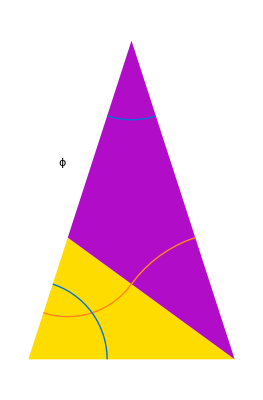

```mathematica
Show[See@FullInflate[starseed,6]]
```

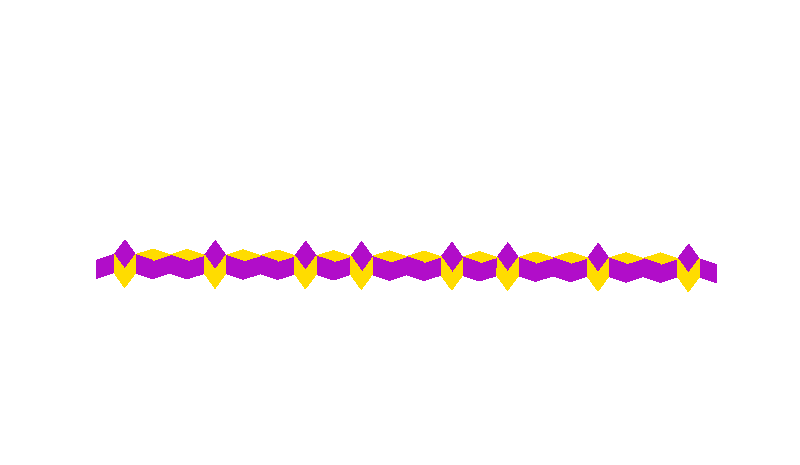

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.0730658003275355,0.46395030173298013],List[1.0726551073229873,0.4082237250715891],List[1.125527320069748,0.3906126735867088],List[1.1259380130742964,0.44633925024809973]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.0406427980253743,0.5092754485816768],List[1.0075552804829124,0.4644331003155664],List[1.0399782827850736,0.4191079534668697],List[1.0730658003275355,0.46395030173298013]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[1.072655107322987,0.4082237250715893],List[1.0395675897805252,0.3633813768054789],List[1.0399782827850736,0.4191079534668697],List[1.0730658003275355,0.46395030173298013]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.0075552804829124,0.4644331003155664],List[0.954429245500399,0.44760323334703084],List[0.9540185524958507,0.39187665668563987],List[1.0071445874783642,0.4087065236541755]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[1.0071445874783642,0.4087065236541755],List[1.0395675897805252,0.3633813768054788],List[1.0399782827850736,0.4191079534668697],List[1.0075552804829124,0.4644331003155664]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.954429245500399,0.4476032333470307],List[0.9015570327536381,0.4652142848319112],List[0.9546830677361515,0.4820441518004469],List[1.0075552804829124,0.4644331003155664]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.901557032753638,0.4652142848319112],List[0.9011463397490899,0.4094877081705204],List[0.9540185524958507,0.39187665668563987],List[0.954429245500399,0.4476032333470307]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.901557032753638,0.4652142848319112],List[0.8484309977711244,0.4483844178633756],List[0.8480203047665762,0.39265784120198477],List[0.9011463397490899,0.4094877081705204]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.8484309977711245,0.44838441786337546],List[0.7955587850243636,0.46599546934825586],List[0.8486848200068771,0.4828253363167916],List[0.901557032753638,0.4652142848319112]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7955587850243635,0.465995469348256],List[0.7951480920198153,0.4102688926868653],List[0.8480203047665762,0.39265784120198477],List[0.8484309977711245,0.44838441786337546]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7631357827222025,0.5113206161969527],List[0.7300482651797406,0.46647826793084207],List[0.7624712674819016,0.42115312108214553],List[0.7955587850243635,0.465995469348256]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.7951480920198154,0.41026889268686506],List[0.7620605744773534,0.3654265444207546],List[0.7624712674819016,0.42115312108214553],List[0.7955587850243635,0.465995469348256]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7300482651797406,0.46647826793084224],List[0.6769222301972271,0.4496484009623066],List[0.6765115371926789,0.3939218243009157],List[0.7296375721751924,0.4107516912694513]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.7296375721751924,0.4107516912694513],List[0.7620605744773534,0.3654265444207546],List[0.7624712674819016,0.42115312108214553],List[0.7300482651797406,0.46647826793084224]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.6769222301972271,0.4496484009623065],List[0.6240500174504662,0.4672594524471871],List[0.6771760524329796,0.48408931941572275],List[0.7300482651797406,0.46647826793084224]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.6240500174504662,0.4672594524471871],List[0.623639324445918,0.4115328757857961],List[0.6765115371926789,0.3939218243009157],List[0.6769222301972271,0.4496484009623065]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.6240500174504662,0.4672594524471871],List[0.5709239824679526,0.45042958547865136],List[0.5705132894634044,0.3947030088172606],List[0.623639324445918,0.4115328757857961]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5709239824679526,0.45042958547865136],List[0.5180517697211917,0.4680406369635318],List[0.5711778047037053,0.48487050393206754],List[0.6240500174504662,0.4672594524471871]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.5180517697211917,0.46804063696353193],List[0.5176410767166435,0.4123140603021411],List[0.5705132894634044,0.3947030088172606],List[0.5709239824679526,0.45042958547865136]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.4856287674190306,0.5133657838122285],List[0.45254124987656885,0.46852343554611803],List[0.4849642521787299,0.4231982886974215],List[0.5180517697211917,0.46804063696353193]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5176410767166435,0.412314060302141],List[0.48455355917418175,0.36747171203603046],List[0.4849642521787299,0.4231982886974215],List[0.5180517697211917,0.46804063696353193]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.45254124987656874,0.46852343554611814],List[0.3994152148940553,0.4516935685775824],List[0.3990045218895071,0.39596699191619156],List[0.45213055687202064,0.41279685888472717]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.45213055687202064,0.41279685888472717],List[0.45254124987656885,0.46852343554611803],List[0.4849642521787299,0.4231982886974215],List[0.4845535591741817,0.3674717120360306]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3994152148940553,0.4516935685775824],List[0.3465430021472944,0.4693046200624629],List[0.39966903712980784,0.4861344870309986],List[0.45254124987656874,0.46852343554611814]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.34654300214729433,0.4693046200624629],List[0.3461323091427462,0.41357804340107196],List[0.3990045218895071,0.39596699191619156],List[0.3994152148940553,0.4516935685775824]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3461323091427462,0.41357804340107196],List[0.3130447916002843,0.3687356951349616],List[0.31345548460483247,0.42446227179635254],List[0.34654300214729433,0.4693046200624629]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.3141199998451333,0.5146297669111595],List[0.28103248230267136,0.4697874186450491],List[0.31345548460483247,0.42446227179635254],List[0.34654300214729433,0.4693046200624629]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.28103248230267136,0.4697874186450491],List[0.22790644732015786,0.45295755167651336],List[0.22749575431560964,0.3972309750151226],List[0.2806217892981232,0.4140608419836582]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2806217892981232,0.4140608419836582],List[0.28103248230267136,0.4697874186450492],List[0.31345548460483247,0.42446227179635254],List[0.3130447916002843,0.3687356951349616]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.22790644732015786,0.4529575516765134],List[0.1750342345733969,0.47056860316139393],List[0.22816026955591046,0.4873984701299296],List[0.28103248230267136,0.4697874186450491]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.1750342345733969,0.47056860316139393],List[0.1746235415688487,0.414842026500003],List[0.22749575431560964,0.3972309750151226],List[0.22790644732015786,0.4529575516765134]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.1750342345733969,0.47056860316139393],List[0.12190819959088336,0.4537387361928582],List[0.12149750658633518,0.3980121595314673],List[0.1746235415688487,0.414842026500003]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.12190819959088339,0.45373873619285815],List[0.06903598684412243,0.47134978767773866],List[0.12216202182663596,0.48817965464627444],List[0.1750342345733969,0.47056860316139393]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.06903598684412246,0.4713497876777386],List[0.0686252938395743,0.4156232110163477],List[0.12149750658633518,0.3980121595314673],List[0.12190819959088339,0.45373873619285815]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.0686252938395743,0.4156232110163478],List[0.03553777629711241,0.37078086275023736],List[0.035948469301660596,0.4265074394116283],List[0.06903598684412246,0.4713497876777386]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.03661298454196138,0.5166749345264352],List[0.0035254669994994603,0.47183258626032487],List[0.035948469301660596,0.4265074394116283],List[0.06903598684412246,0.4713497876777386]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.003525466999499488,0.4718325862603248],List[-0.04960056798301404,0.4550027192917891],List[-0.05001126098756223,0.39927614263039823],List[0.003114773994951331,0.41610600959893407]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.003114773994951331,0.41610600959893407],List[0.0035254669994994603,0.47183258626032487],List[0.035948469301660596,0.4265074394116283],List[0.035537776297112356,0.37078086275023736]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.049600567983014016,0.4550027192917891],List[-0.10247278072977489,0.47261377077666966],List[-0.04934674574726139,0.48944363774520533],List[0.003525466999499488,0.4718325862603248]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.10247278072977495,0.47261377077666955],List[-0.10288347373432316,0.41688719411527864],List[-0.05001126098756223,0.39927614263039823],List[-0.049600567983014016,0.4550027192917891]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.13489578303193606,0.5179389176253661],List[-0.16798330057439792,0.47309656935925576],List[-0.1355602982722368,0.4277714225105592],List[-0.10247278072977495,0.47261377077666955]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.10288347373432316,0.41688719411527875],List[-0.13597099127678502,0.3720448458491683],List[-0.1355602982722368,0.4277714225105592],List[-0.10247278072977495,0.47261377077666955]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.16798330057439786,0.47309656935925576],List[-0.22110933555691137,0.45626670239072],List[-0.22152002856145953,0.4005401257293292],List[-0.16839399357894608,0.417369992697865]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.16839399357894608,0.417369992697865],List[-0.13597099127678502,0.3720448458491683],List[-0.1355602982722368,0.4277714225105592],List[-0.16798330057439786,0.47309656935925576]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.22110933555691137,0.4562667023907201],List[-0.27398154830367216,0.47387775387560055],List[-0.22085551332115877,0.4907076208441362],List[-0.16798330057439786,0.47309656935925576]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.2739815483036723,0.4738777538756005],List[-0.27439224130822054,0.4181511772142096],List[-0.22152002856145953,0.4005401257293292],List[-0.22110933555691137,0.4562667023907201]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.2739815483036723,0.4738777538756005],List[-0.32710758328618583,0.4570478869070649],List[-0.32751827629073405,0.40132131024567397],List[-0.27439224130822054,0.4181511772142096]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.32710758328618583,0.4570478869070649],List[-0.37997979603294674,0.4746589383919454],List[-0.3268537610504333,0.4914888053604811],List[-0.2739815483036723,0.4738777538756005]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.3799797960329466,0.4746589383919454],List[-0.38039048903749495,0.4189323617305545],List[-0.32751827629073405,0.40132131024567397],List[-0.32710758328618583,0.4570478869070649]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.41240279833510773,0.5199840852406421],List[-0.4454903158775696,0.4751417369745316],List[-0.4130673135754086,0.42981659012583495],List[-0.3799797960329466,0.4746589383919454]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.38039048903749495,0.4189323617305545],List[-0.4134780065799568,0.37409001346444404],List[-0.4130673135754086,0.42981659012583495],List[-0.3799797960329466,0.4746589383919454]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.4454903158775696,0.4751417369745316],List[-0.49861635086008316,0.45831187000599594],List[-0.49902704386463137,0.402585293344605],List[-0.4459010088821179,0.41941516031314074]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4459010088821179,0.41941516031314074],List[-0.4134780065799568,0.37409001346444404],List[-0.4130673135754086,0.42981659012583495],List[-0.4454903158775696,0.4751417369745316]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.49861635086008316,0.45831187000599594],List[-0.5514885636068441,0.4759229214908764],List[-0.4983625286243305,0.49275278845941206],List[-0.4454903158775696,0.4751417369745316]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5514885636068441,0.4759229214908764],List[-0.5518992566113924,0.42019634482948554],List[-0.49902704386463137,0.402585293344605],List[-0.49861635086008316,0.45831187000599594]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5514885636068441,0.4759229214908764],List[-0.6046145985893577,0.4590930545223407],List[-0.6050252915939058,0.4033664778609499],List[-0.5518992566113924,0.42019634482948554]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.6046145985893576,0.4590930545223407],List[-0.6574868113361186,0.47670410600722124],List[-0.604360776353605,0.4935339729757569],List[-0.5514885636068441,0.4759229214908764]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.6574868113361185,0.47670410600722124],List[-0.6578975043406667,0.4209775293458303],List[-0.6050252915939058,0.4033664778609499],List[-0.6046145985893576,0.4590930545223407]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.6899098136382796,0.5220292528559178],List[-0.7229973311807415,0.4771869045898074],List[-0.6905743288785804,0.4318617577411107],List[-0.6574868113361185,0.47670410600722124]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.6578975043406667,0.4209775293458303],List[-0.6909850218831286,0.3761351810797199],List[-0.6905743288785804,0.4318617577411107],List[-0.6574868113361185,0.47670410600722124]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.7229973311807415,0.4771869045898074],List[-0.7761233661632551,0.46035703762127167],List[-0.7765340591678032,0.40463046095988087],List[-0.7234080241852896,0.4214603279284165]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.7234080241852896,0.4214603279284165],List[-0.6909850218831285,0.3761351810797199],List[-0.6905743288785804,0.4318617577411107],List[-0.7229973311807415,0.4771869045898074]]]]],Rule[ImageMargins,0.],Rule[ImagePadding,List[List[0.,0.625],List[0.625,0.]]],Rule[ImageSize,List[800.374999999993,Automatic]],Rule[PlotRange,List[List[-0.849163889856715,1.1581808842316623],List[-0.038541019662496845,1.1283548116705382]]],Rule[PlotRangePadding,Automatic]]
```

-Graphics-

```mathematica
automaton=({{"B"->"A'","α'"},{"A'"->"A'","β'"},{"A'"->"B'","δ"},{"B'"->"B'","ϵ"},{"B'"->"A","α"},{"A"->"A","β"},{"A"->"B","δ'"},{"B"->"B","ϵ'"}, {"B"->"B'","γ"},{"B'"->"B","γ'"}}/.Rule->DirectedEdge)/.{"B"->"T'","B'"->"T","A"->"t","A'"->"t'"}
names={"A","B'","A'","B"}/.{"B"->"T","B'"->"T'","A"->"t","A'"->"t'"}
```

{{T'->t',α'},{t'->t',β'},{t'->T,δ},{T->T,ϵ},{T->t,α},{t->t,β},{t->T',δ'},{T'->T',ϵ'},{T'->T,γ},{T->T',γ'}}

{t,T',t',T}

```mathematica
vertexrules=MapThread[Rule[#1,Placed[#1,#2]]&,{names,{{Before},{Above},{After},{Below}}}]
```

{t→Placed[t,{Before}],T'→Placed[T',{Above}],t'→Placed[t',{After}],T→Placed[T,{Below}]}

```mathematica
Graph[MapThread[Labeled,{automaton[[All,1]],automaton[[All,2]]}], VertexLabels->vertexrules, VertexLabelStyle->Directive[20], EdgeLabelStyle->Directive[20],GraphStyle->"BasicBlack"]
```

-Graphics-

```mathematica
Edg
```

```mathematica
automaton[[All,1]]
```

{B→A',A'→A',A'→B',B'→B',B'→A,A→A,A→B,B→B,B→B',B'→B}

```mathematica
edgerules=MapThread[#1->Graphics[{Table[{Opacity[0.4-1/n],FaceForm[White],Disk[{0,0},1/n]},{n,1,50}],{Text[Style[#2,20, FontFamily->"CMU Serif"]]}}]&,{automaton[[All,1]],automaton[[All,2]],{{Above,After},{After},{Below,After},{Below},{Below,Before},{Before},{Above, Before},{Above},{After},{Before}}}]
```

{T'->t'→-Graphics-,t'->t'→-Graphics-,t'->T→-Graphics-,T->T→-Graphics-,T->t→-Graphics-,t->t→-Graphics-,t->T'→-Graphics-,T'->T'→-Graphics-,T'->T→-Graphics-,T->T'→-Graphics-}

```mathematica
Graph[automaton[[All,1]],VertexLabels->vertexrules, EdgeLabels->edgerules,VertexLabelStyle->Directive[20,FontFamily->"CMU Serif"],GraphStyle->"BasicBlack",ImageSize->600]
Export["UpDownGraph.png",%,ImageResolution->300]
```

-Graphics-

UpDownGraph.png

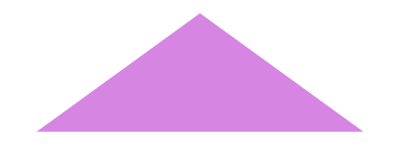

```mathematica
SeeFaded@{unitfat}
```

```mathematica
a1=Graphics[Line[{{{1,1/2},{2,0},{1,-1/2}}}]];
a2=Graphics[Line[{{{0,1/2},{1,0},{0,-1/2}},{{1,1/2},{2,0},{1,-1/2}}}]];
a3=Graphics[Line[{{{-1,1/2},{0,0},{-1,-1/2}},{{0,1/2},{1,0},{0,-1/2}},{{1,1/2},{2,0},{1,-1/2}}}]];
```

```mathematica
ArrowEdges[{{A_,B_,C_},T_}]:=
If[T=="fat",
Graphics[{
{Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[1]],#[[3]]}]},
{Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]}
}]&@Coor@{A,B,C},
Graphics[{
{Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[3]],#[[1]]}]},
{Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]}
}]&@Coor@{A,B,C}]

SeeFaded:=Graphics[{Opacity[0.3],Transpose[{((IfFat[#1,NicePurple,NiceYellow]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}]&
```

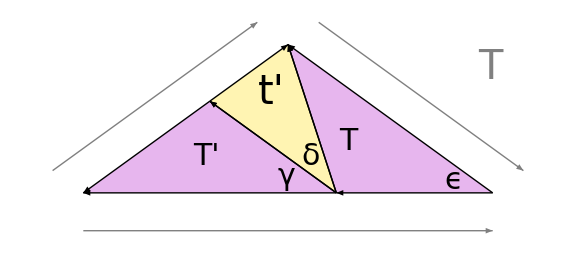

TF.png

```mathematica
Show[SeeFaded@Inflate[{unitfat},1],ArrowEdges/@Inflate[{unitfat},1],
Graphics[Text[Style["γ",30, FontFamily->"CMU Serif"],{-0.005852264137550245,0.07022716965060338}]],Graphics[Text[Style["δ",30, FontFamily->"CMU Serif"],{0.0907100941320289,0.14903866899467566}]],Graphics[Text[Style["ϵ",30, FontFamily->"CMU Serif"],{0.6554535834056285,0.05247631072509673}]],Graphics[Text[Style["T'",30, FontFamily->"CMU Serif"],{-0.32187452756526413,0.14903866899467522}]],Graphics[Text[Style["t'",40, FontFamily->"CMU Serif"],{-0.0643749055130527,0.4006860269093364}]],Graphics[Text[Style["T",30, FontFamily->"CMU Serif"],{0.23994282963956048,0.2075613103701781}]],
Graphics[{Gray,Text[Style["T",40, FontFamily->"CMU Serif"],{0.8,0.5}]}],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[1]],#[[3]]}]},0.15(#[[3]]-#[[2]])]&@Coor@Δ@unitfat],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},0.15(#[[3]]-#[[1]])]&@Coor@Δ@unitfat],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]},0.15({0,-1})]&@Coor@Δ@unitfat],
ImageSize->Large
]
Export["TF.png",%,ImageResolution->300]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["T.png"]]]
```

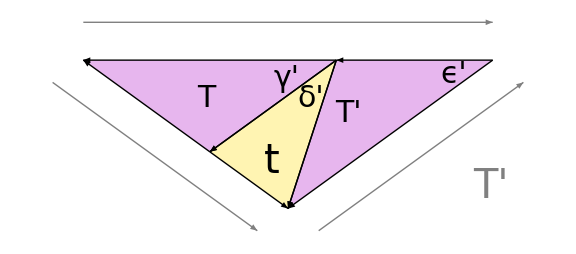

TF'.png

```mathematica
Show[SeeFaded@Inflate[{Conj@unitfat},1],ArrowEdges/@Inflate[{Conj@unitfat},1],
Graphics[Text[Style["γ'",30, FontFamily->"CMU Serif"],{-0.005852264137550245,-0.07022716965060338}]],Graphics[Text[Style["δ'",30, FontFamily->"CMU Serif"],{0.0907100941320289,-0.14903866899467566}]],Graphics[Text[Style["ϵ'",30, FontFamily->"CMU Serif"],{0.6554535834056285,-0.05247631072509673}]],Graphics[Text[Style["T",30, FontFamily->"CMU Serif"],{-0.32187452756526413,-0.14903866899467522}]],Graphics[Text[Style["t",40, FontFamily->"CMU Serif"],{-0.0643749055130527,-0.4006860269093364}]],Graphics[Text[Style["T'",30, FontFamily->"CMU Serif"],{0.23994282963956048,-0.2075613103701781}]],
Graphics[{Gray,Text[Style["T'",40, FontFamily->"CMU Serif"],{0.8,-0.5}]}],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[1]],#[[3]]}]},0.15(#[[3]]-#[[2]])]&@Coor@Δ@Conj@unitfat],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},0.15(#[[3]]-#[[1]])]&@Coor@Δ@Conj@unitfat],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]},0.15({0,1})]&@Coor@Δ@Conj@unitfat],
ImageSize->Large
]
Export["TF'.png",%,ImageResolution->300]
```

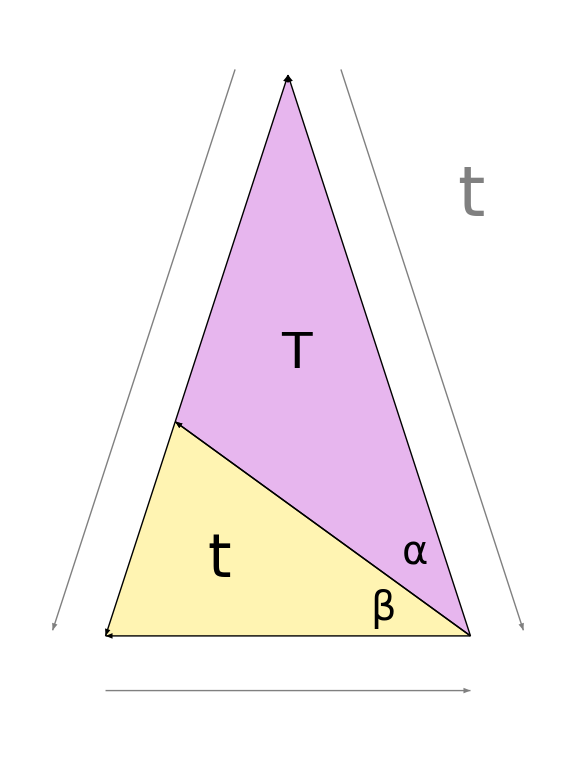

tS.png

```mathematica
Show[SeeFaded@Inflate[{unitskinny},1],ArrowEdges/@Inflate[{unitskinny},1],
Graphics[Text[Style["β",40, FontFamily->"CMU Serif"],{0.25910539662002213,0.07303394842367927}]],Graphics[Text[Style["α",40, FontFamily->"CMU Serif"],{0.34755820241294855,0.22703397043860196}]],Graphics[Text[Style["t",60, FontFamily->"CMU Serif"],{-0.189885164661828,0.2070478594952605}]],Graphics[Text[Style["T",50, FontFamily->"CMU Serif"],{0.021951326907476976,0.7734004519241982}]],
Graphics[{Gray,Text[Style["t",70, FontFamily->"CMU Serif"],{0.5,1.2042972031781072}]}],
Graphics[Translate[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[3]],#[[1]]}]},0.15(#[[3]]-#[[2]])],0.14(#[[1]]-#[[3]])]&@Coor@Δ@unitskinny],
Graphics[Translate[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},0.15(#[[3]]-#[[1]])],0.14(#[[2]]-#[[3]])]&@Coor@Δ@unitskinny],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]},0.15({0,-1})]&@Coor@Δ@unitskinny],
ImageSize->Large
]
Export["tS.png",%,ImageResolution->300]
```

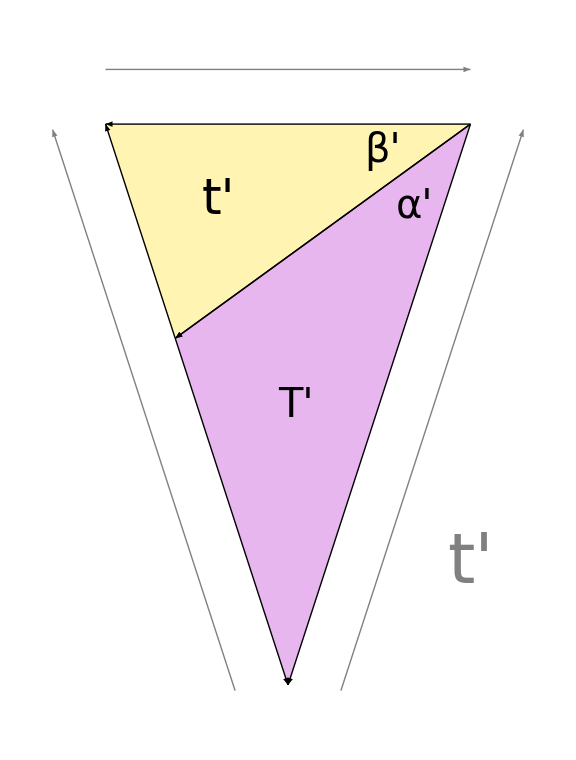

tS'.png

```mathematica
Show[SeeFaded@Inflate[{Conj@unitskinny},1],ArrowEdges/@Inflate[{Conj@unitskinny},1],
Graphics[Text[Style["β'",40, FontFamily->"CMU Serif"],{0.25910539662002213,-0.07303394842367927}]],Graphics[Text[Style["α'",40, FontFamily->"CMU Serif"],{0.34755820241294855,-0.22703397043860196}]],Graphics[Text[Style["t'",50, FontFamily->"CMU Serif"],{-0.189885164661828,-0.2070478594952605}]],Graphics[Text[Style["T'",40, FontFamily->"CMU Serif"],{0.021951326907476976,-0.7734004519241982}]],
Graphics[{Gray,Text[Style["t'",70, FontFamily->"CMU Serif"],{0.5,-1.2042972031781072}]}],
Graphics[Translate[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[3]],#[[1]]}]},0.15(#[[3]]-#[[2]])],0.14(#[[1]]-#[[3]])]&@Coor@Δ@Conj@unitskinny],
Graphics[Translate[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[3]],#[[2]]}]},0.15(#[[3]]-#[[1]])],0.14(#[[2]]-#[[3]])]&@Coor@Δ@Conj@unitskinny],
Graphics[Translate[
{Gray,Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]},0.15({0,1})]&@Coor@Δ@Conj@unitskinny],
ImageSize->Large
]
Export["tS'.png",%,ImageResolution->300]
```

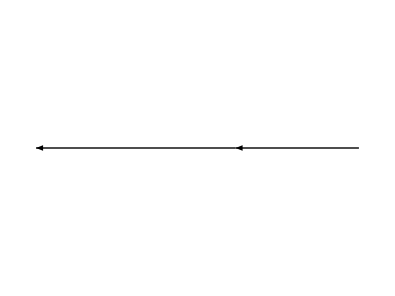
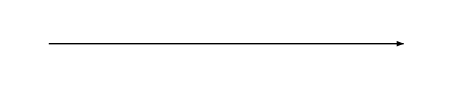
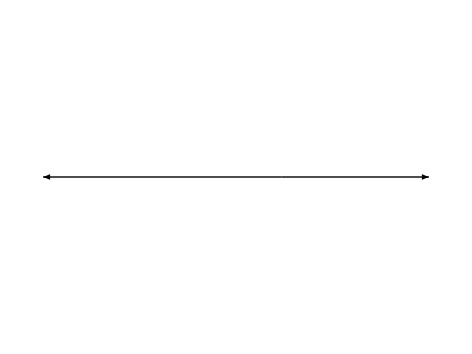
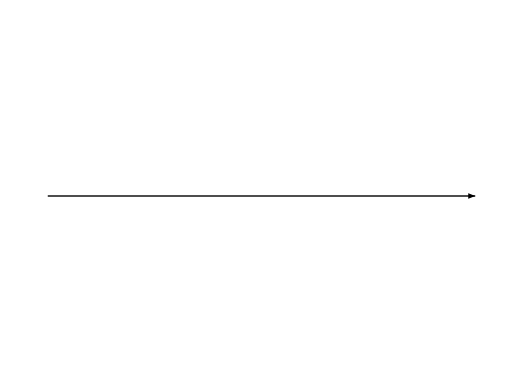
```mathematica
Export["a1inflate.png",-Graphics-,ImageResolution->300]
Export["a1.png",-Graphics-,ImageResolution->300]

Export["a2inflate.png",-Graphics-,ImageResolution->300]
Export["a2.png",-Graphics-,ImageResolution->300]
```

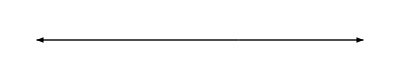

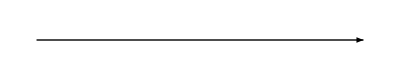

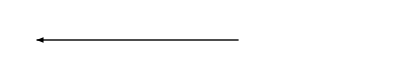

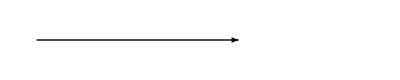

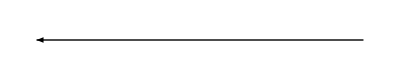

-Graphics-

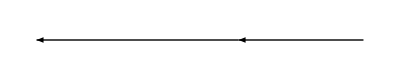

-Graphics-

```mathematica
Graphics[{
{Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[2]],#[[1]]}]},
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[2]],#[[3]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a1inflate.png",%,ImageResolution->300];
Graphics[{
{Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[1]],#[[3]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a1.png",%,ImageResolution->300];

Graphics[{
{Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[2]],#[[1]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a2inflate.png",%,ImageResolution->300];
Graphics[{
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[2]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a2.png",%,ImageResolution->300];

Graphics[{
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[3]],#[[1]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a3inflate.png",%,ImageResolution->300];
Graphics[{
{Arrowheads[{{Automatic,0.5,a2}}],Arrow[{#[[1]],#[[3]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a3.png",%,ImageResolution->300];

Graphics[{
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[2]],#[[1]]}]},
{Arrowheads[{{Automatic,0.5,a1}}],Arrow[{#[[3]],#[[2]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a4inflate.png",%,ImageResolution->300];
Graphics[{
{Arrowheads[{{Automatic,0.5,a3}}],Arrow[{#[[1]],#[[3]]}]}
},PlotRange->{{0,ϕ},{-0.1,0.1}}]&@{{0,0},{1,0},{ϕ,0}}
Export["a4.png",%,ImageResolution->300];
```

```mathematica
See@{unitskinny}
```

```mathematica
Graphics[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5,0],List[0.5,0],List[0.,1.5388417685876268]]]]]
```

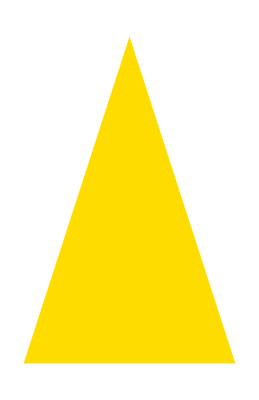

```mathematica
Graphics[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5,0],List[0.5,0],List[0.,1.5388417685876268]]]]]
```

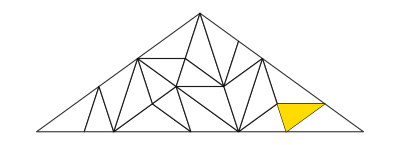

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[-0.42705098312484224,0],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.1180339887498949,0.22451398828979272],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.5,0.22451398828979272],List[-0.8090169943749475,0],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0],List[-0.42705098312484224,0],List[-0.5,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0],List[-0.5,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.1180339887498949,0.22451398828979272],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.30901699437494756,0.3632712640026805],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.19098300562505244,0]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[1.1102230246251565*^-16,0.5877852522924732],List[0.1909830056250527,0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.30901699437494756,0.3632712640026805],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805],List[0.11803398874989479,0.22451398828979274]]]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]]]]
Export["Down1.png",%,ImageResolution->300];
```

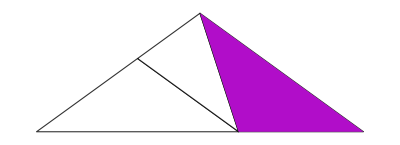

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.8090169943749475,0],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]]
Export["Down1.png",%,ImageResolution->300];
```

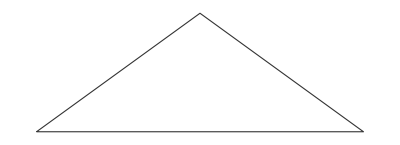

```mathematica
Graphics[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[GrayLevel[1],Polygon[List[List[-0.8090169943749475,0],List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732]]]]]]
Export["Down4.png",%,ImageResolution->300];
```

```mathematica
Show[See@Inflate[{unitfat},2],ArrowEdges/@Inflate[{unitfat},2]]
```

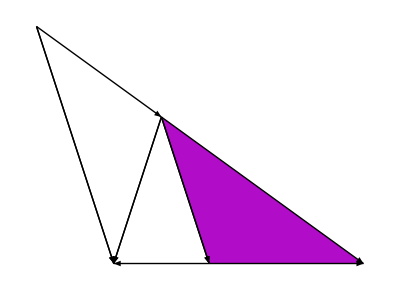

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.30901699437494756,0.3632712640026805],List[0.8090169943749475,0],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.30901699437494756,0.3632712640026805],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.42705098312484224,0],List[0.8090169943749475,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.30901699437494756,0.3632712640026805],List[0.8090169943749475,0]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.30901699437494756,0.3632712640026805],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.30901699437494756,0.3632712640026805],List[0.19098300562505244,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.42705098312484224,0],List[0.19098300562505244,0]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.30901699437494756,0.3632712640026805]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.30901699437494756,0.3632712640026805],List[0.19098300562505244,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]]]
Export["Up3Left.png",%,ImageResolution->300];
```

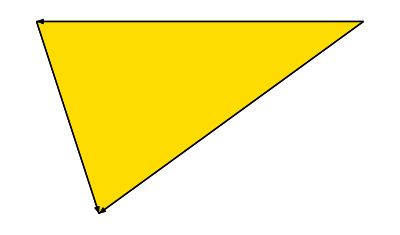
```mathematica
-Graphics-//FullForm
```

```mathematica
Graphics[List[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0]]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0]]]]]]
Export["Up1Left.png",%,ImageResolution->300];
```

-Graphics-

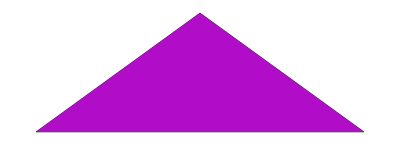

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[GrayLevel[1],Polygon[List[List[-0.8090169943749475,0],List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732]]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.8090169943749475,0],List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732]]]]]]
Export["Down4.png",%,ImageResolution->300];
```

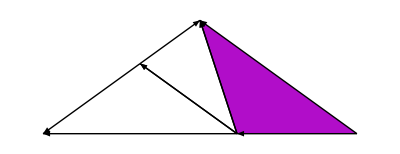
```mathematica
-Graphics-//FullForm
```

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.19098300562505244,0],List[-0.30901699437494745,0.3632712640026805]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[-0.30901699437494745,0.3632712640026805],List[-0.8090169943749475,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.19098300562505244,0],List[-0.8090169943749475,0]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.19098300562505244,0],List[-0.30901699437494745,0.3632712640026805]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.19098300562505244,0],List[1.1102230246251565*^-16,0.5877852522924732]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.8090169943749475,0],List[0.19098300562505244,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.19098300562505244,0],List[1.1102230246251565*^-16,0.5877852522924732]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732]]]]]],Rule[ImagePadding,List[List[0.,0.909091],List[0.909091,0.]]],Rule[PlotRange,List[List[-0.8427260358072369,0.8427260358072369],List[-0.032360679774997896,0.6201459320674712]]],Rule[PlotRangePadding,Automatic]]
Export["Up4Left.png",%,ImageResolution->300]
```

-Graphics-

Up4Left.png

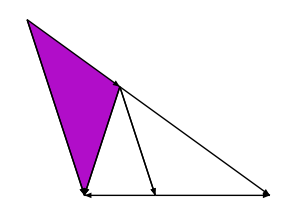
```mathematica
-Graphics-//FullForm
```

-Graphics-

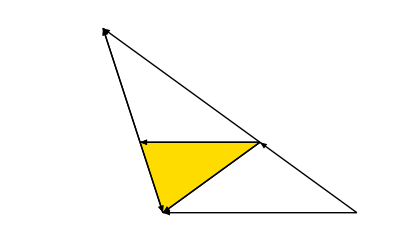

```mathematica
Graphics[List[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.30901699437494756,0.3632712640026805]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.30901699437494756,0.3632712640026805]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0]]]]],List[List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.8090169943749475,0],List[0.6180339887498949,0.1387572757128878]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.6180339887498949,0.1387572757128878],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.8090169943749475,0],List[0.42705098312484224,0]]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[-1,Rational[1,2]],List[0,0],List[-1,Rational[-1,2]]],List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[-1,0.5],List[0,0],List[-1,-0.5]],List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0]]]],List[Arrowheads[List[List[Automatic,0.5,GraphicsBox[LineBox[NCache[List[List[List[0,Rational[1,2]],List[1,0],List[0,Rational[-1,2]]],List[List[1,Rational[1,2]],List[2,0],List[1,Rational[-1,2]]]],List[List[List[0,0.5],List[1,0],List[0,-0.5]],List[List[1,0.5],List[2,0],List[1,-0.5]]]]]]]]],Arrow[List[List[0.3819660112501052,0.1387572757128878],List[0.30901699437494756,0.3632712640026805]]]]],Rule[ImagePadding,List[List[0.,0.909091],List[0.909091,0.]]],Rule[PlotRange,List[List[0.1781072975260963,0.8218927024739036],List[-0.0123606797749979,0.3756319437776784]]],Rule[PlotRangePadding,Automatic]]
Export["Up2Left.png",%,ImageResolution->300];
```

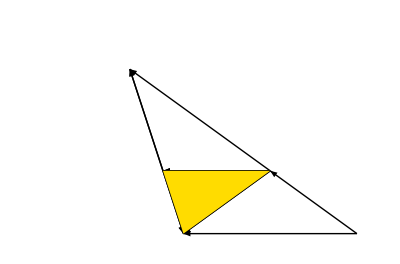

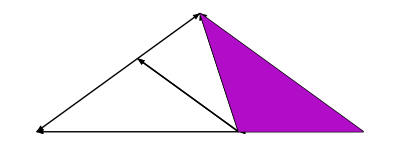

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.8090169943749475,0],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]]
Export["Down3.png",%,ImageResolution->300];
```

-Graphics-

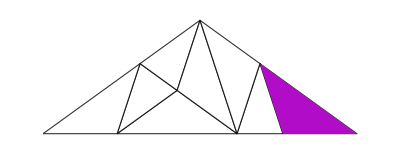

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[List[GrayLevel[1],Polygon[List[List[-0.42705098312484224,0],List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0]]]],List[GrayLevel[1],Polygon[List[List[-0.8090169943749475,0],List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0]]]],List[GrayLevel[1],Polygon[List[List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732]]]],List[GrayLevel[1],Polygon[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[0.30901699437494756,0.3632712640026805],List[0.8090169943749475,0],List[0.42705098312484224,0]]]],List[GrayLevel[1],Polygon[List[List[0.42705098312484224,0],List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805]]]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.30901699437494756,0.3632712640026805],List[0.8090169943749475,0],List[0.42705098312484224,0]]]]],Rule[ImagePadding,List[List[0.,0.909091],List[0.909091,0.]]],Rule[PlotRange,List[List[-0.8427260358072369,0.8427260358072369],List[-0.032360679774997896,0.6201459320674712]]],Rule[PlotRangePadding,Automatic]]
Export["Down2.png",%,ImageResolution->300];
```

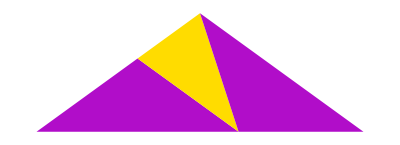

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.19098300562505244,0],List[-0.8090169943749475,0],List[-0.30901699437494745,0.3632712640026805]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.8090169943749475,0],List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0]]]]]]
Export["Up4.png",%,ImageResolution->300];
```

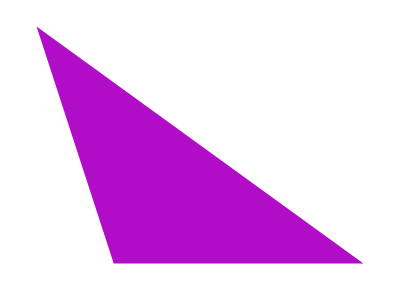

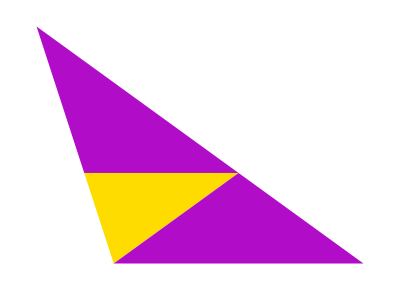

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.30901699437494756,0.3632712640026805],List[0.3819660112501052,0.1387572757128878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.8090169943749475,0],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]]]]
Export["Up2.png",%,ImageResolution->300];
```

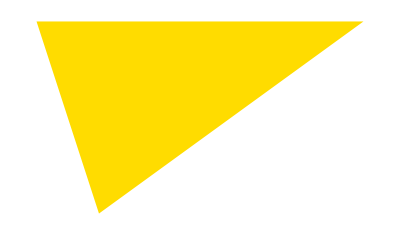

```mathematica
Graphics[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]]]
Export["Up1.png",%,ImageResolution->300];
```

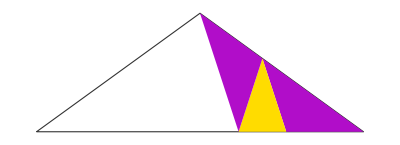

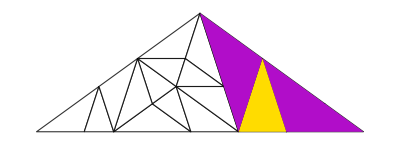
```mathematica
-Graphics-//FullForm
```

```mathematica
Graphics[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],List[List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[-0.42705098312484224,0],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.1180339887498949,0.22451398828979272],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.5,0.22451398828979272],List[-0.8090169943749475,0],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0],List[-0.42705098312484224,0],List[-0.5,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.42705098312484224,0],List[-0.5,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.1180339887498949,0.22451398828979272],List[-0.30901699437494745,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.1180339887498949,0.22451398828979272],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[-0.1180339887498949,0.22451398828979272],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.30901699437494756,0.3632712640026805],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[0.42705098312484224,0],List[0.6180339887498949,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.42705098312484224,0],List[0.19098300562505244,0]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[1.1102230246251565*^-16,0.5877852522924732],List[0.1909830056250527,0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.30901699437494756,0.3632712640026805],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805],List[0.11803398874989479,0.22451398828979274]]]]]],List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.30901699437494756,0.3632712640026805],List[0.8090169943749475,0],List[0.42705098312484224,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.42705098312484224,0],List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.1102230246251565*^-16,0.5877852522924732],List[0.19098300562505244,0],List[0.30901699437494756,0.3632712640026805]]]]]]]
Export["Down3.png",%,ImageResolution->300];
```

-Graphics-

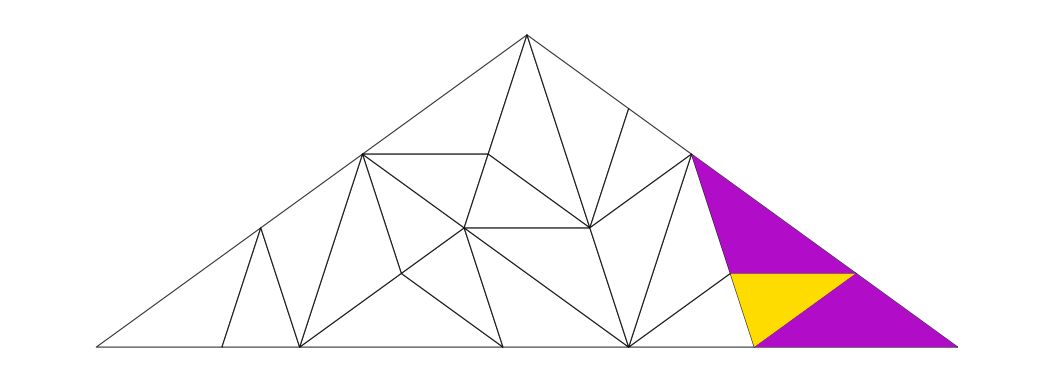

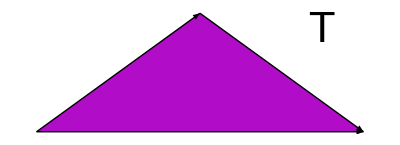

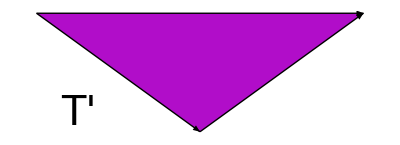

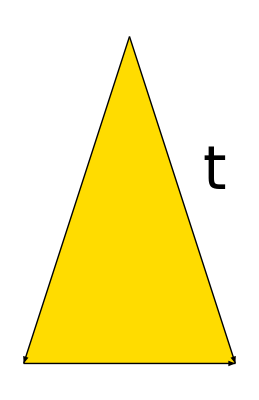

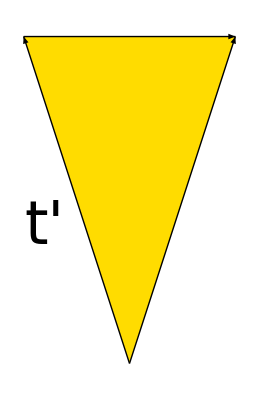

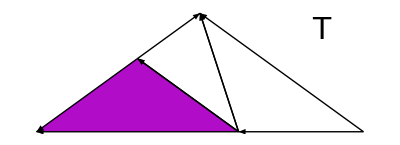
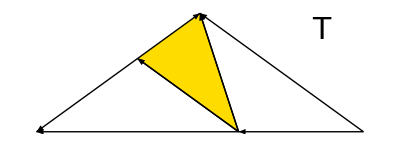
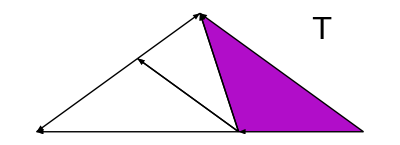

```mathematica
TR=Show[See@Inflate[{unitfat},0],ArrowEdges/@Inflate[{unitfat},0],Graphics[Text[Style["T",2*20, FontFamily->"CMU Serif"],{0.6,0.5}]]]

TL=Rotate[Show[See@Inflate[{Conj@unitfat},0],ArrowEdges/@Inflate[{Conj@unitfat},0],Graphics[Rotate[Text[Style["T'",2*20, FontFamily->"CMU Serif"],{-0.6,-0.5}],Pi]]],Pi]

tR=Show[See@Inflate[{unitskinny},0],ArrowEdges/@Inflate[{unitskinny},0],Graphics[Text[Style["t",2*30, FontFamily->"CMU Serif"],{0.4,0.9}]]]

tL=Rotate[Show[See@Inflate[{Conj@unitskinny},0],ArrowEdges/@Inflate[{Conj@unitskinny},0],Graphics[Rotate[Text[Style["t'",2*30, FontFamily->"CMU Serif"],{-0.4,-0.9}],Pi]]],Pi]

{TR1,TR2,TR3}=Table[Show[See@{Inflate[{unitfat},1][[i]]},ArrowEdges/@Inflate[{unitfat},1],Graphics[Text[Style["T",2*15, FontFamily->"CMU Serif"],{0.6,0.5}]]],{i,{1,2,3}}]

{tR1,tR2}=Table[Show[See@{Inflate[{unitskinny},1][[i]]},ArrowEdges/@Inflate[{unitskinny},1],Graphics[Text[Style["t",2*20, FontFamily->"CMU Serif"],{0.4,0.9}]]],{i,{1,2}}]

{TL1,TL2,TL3}=Table[Rotate[Show[See@{Inflate[{Conj@unitfat},1][[i]]},ArrowEdges/@Inflate[{Conj@unitfat},1],Graphics[Rotate[Text[Style["T'",2*15, FontFamily->"CMU Serif"],{-0.6,-0.5}],Pi]]],Pi],{i,{1,2,3}}]

{tL1,tL2}=Table[Rotate[Show[See@{Inflate[{Conj@unitskinny},1][[i]]},ArrowEdges/@Inflate[{Conj@unitskinny},1],Graphics[Rotate[Text[Style["t'",2*20, FontFamily->"CMU Serif"],{-0.4,-0.9}],Pi]]],Pi],{i,{1,2}}]
```

```mathematica
graphedgelabel:=Graphics[{Table[{Opacity[0.4-1/n],FaceForm[White],Disk[{0,0},1/n]},{n,1,50}],{Text[Style[#,40, FontFamily->"CMU Serif"]]}}]&
```

```mathematica
Graph[{Labeled[TR->TR3,graphedgelabel["ϵ"]],Labeled[TR->TL1,graphedgelabel["γ'"]],Labeled[TR->tR2,graphedgelabel["α"]]},
VertexShapeFunction->"Name",
VertexSize->0.5,
GraphStyle->"BasicBlack",ImagePadding->50,ImageSize->Large
]
Export["TRgraph.png",%,ImageResolution->300]
```

-Graphics-

TRgraph.png

```mathematica
Graph[{Labeled[TL->TL3,graphedgelabel["ϵ'"]],Labeled[TL->tL2,graphedgelabel["α'"]],Labeled[TL->TR1,graphedgelabel["γ"]]},
VertexShapeFunction->"Name",
VertexSize->0.6,
GraphStyle->"BasicBlack",ImagePadding->60,ImageSize->Large
]
Export["TLgraph.png",%,ImageResolution->300]
```

-Graphics-

TLgraph.png

```mathematica
Graph[{Labeled[tL->tL1,graphedgelabel["β'"]],Labeled[tL->TR2,graphedgelabel["δ"]]},
VertexShapeFunction->"Name",
VertexSize->0.7,
GraphStyle->"BasicBlack",ImagePadding->120,ImageSize->Large
]
Export["tslgraph.png",%,ImageResolution->300]
```

-Graphics-

tslgraph.png

```mathematica
Graph[{Labeled[tR->tR1,graphedgelabel["β"]],Labeled[tR->TL2,graphedgelabel["δ'"]]},
VertexShapeFunction->"Name",
VertexSize->0.7,
GraphStyle->"BasicBlack",ImagePadding->120,ImageSize->Large
]
Export["tsrgraph.png",%,ImageResolution->300]
```

-Graphics-

tsrgraph.png

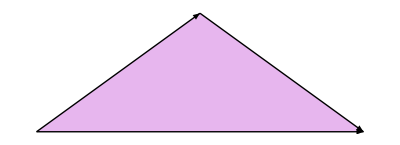

TFRob.png

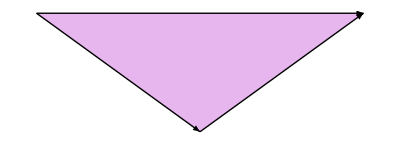

T'FRob.png

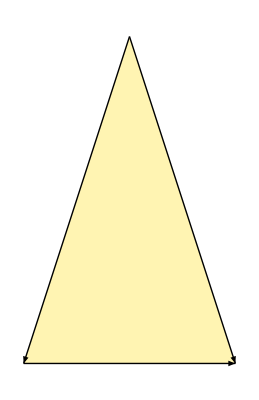

TSRob.png

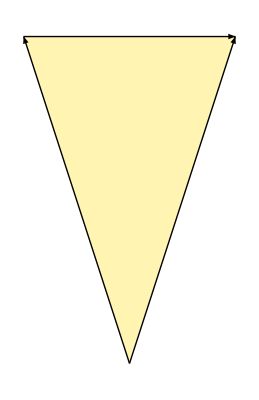

T'SRob.png

-Graphics-

-Graphics-

```mathematica
Show[SeeFaded[{unitfat}],ArrowEdges[unitfat]]
Export["TFRob.png",%,ImageResolution->300]
Rotate[Show[SeeFaded[{Conj@unitfat}],ArrowEdges[Conj@unitfat]],Pi]
Export["T'FRob.png",%,ImageResolution->300]
Show[SeeFaded[{unitskinny}],ArrowEdges[unitskinny]]
Export["TSRob.png",%,ImageResolution->300]
Rotate[Show[SeeFaded[{Conj@unitskinny}],ArrowEdges[Conj@unitskinny]],Pi]
Export["T'SRob.png",%,ImageResolution->300]
```

```mathematica
??See
```

Displays list of polygons as a graphic

See:=Graphics[{Transpose[{((IfFat[#1,NicePurple,NiceYellow]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}]&

```mathematica
unitskinny
```

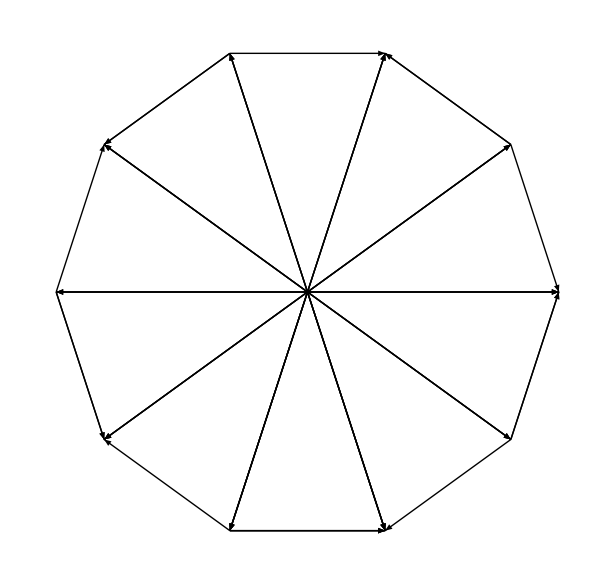

WedgeWheel.png

```mathematica
Show[Table[ArrowEdges@{Exp[i I Pi/5]*({0.5,-0.5,0.+1.5388417685876268 ⅈ}-(0.+1.5388417685876268 ⅈ)),"skinny"},{i,1,10,2}],Table[ArrowEdges@{Exp[i I 2Pi/5]*({-0.5,0.5,0.+1.5388417685876268 ⅈ}-(0.+1.5388417685876268 ⅈ)),"skinny"},{i,0,10}]]
Export["WedgeWheel.png",%,ImageResolution->300]
```

```mathematica
locality={{{0.8090169943749475,0.6180339887498951-0.5877852522924732 ⅈ,1.1102230246251565*^-16-0.5877852522924732 ⅈ,0.19098300562505244},"fat"},{{0.8090169943749475,0.6180339887498951+0.5877852522924732 ⅈ,1.1102230246251565*^-16+0.5877852522924732 ⅈ,0.19098300562505244},"fat"}};
localityshifted={{{0.8090169943749475,0.6180339887498951-0.5877852522924732 ⅈ,1.1102230246251565*^-16-0.5877852522924732 ⅈ,0.19098300562505244}+2*0.5877852522924732 ⅈ,"fat"},{{0.8090169943749475,0.6180339887498951+0.5877852522924732 ⅈ,1.1102230246251565*^-16+0.5877852522924732 ⅈ,0.19098300562505244}+2*0.5877852522924732 ⅈ,"fat"}};
slide=-0.405+0.294I
skinny=Show[See@{{{5.551115123125783*^-17+0.3632712640026805 ⅈ,0.1909830056250526+0.9510565162951538 ⅈ,-0.3090169943749474+0.5877852522924732 ⅈ,-0.5}*Exp[I (Pi/5+Pi)]+slide,"skinny"}},Graphics[MakeCurveRules/@AddRhombTris@{{{5.551115123125783*^-17+0.3632712640026805 ⅈ,-0.3090169943749474+0.5877852522924732 ⅈ,0.1909830056250526+0.9510565162951535 ⅈ}* Exp[I (Pi/5+Pi)]+slide,"skinny"}}]];
```

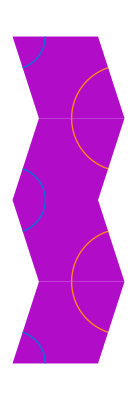

Mistake.png

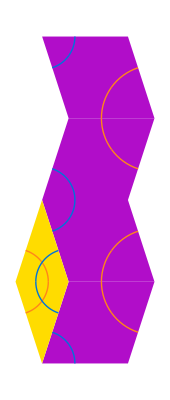

MistakeNext.png

```mathematica
Rotate[Show[See@locality,See@localityshifted,
Graphics[MakeCurveRules/@AddConj@AddRhombTris@{Last@Inflate[{unitfat},1]}],Graphics[Translate[MakeCurveRules/@AddConj@AddRhombTris@{Last@Inflate[{unitfat},1]},{0,2*0.5877852522924732}]]],-Pi/2]
Export["Mistake.png",%,Background->None,ImageResolution->200]
Rotate[Show[See@locality,See@localityshifted,
Graphics[MakeCurveRules/@AddConj@AddRhombTris@{Last@Inflate[{unitfat},1]}],Graphics[Translate[MakeCurveRules/@AddConj@AddRhombTris@{Last@Inflate[{unitfat},1]},{0,2*0.5877852522924732}]],skinny],-Pi/2]
Export["MistakeNext.png",%,Background->None,ImageResolution->200]
```

```mathematica
1/ϕ
```

0.618034

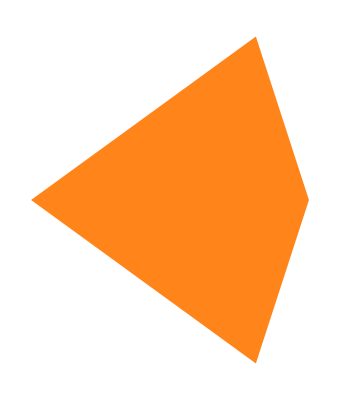

Kite.png

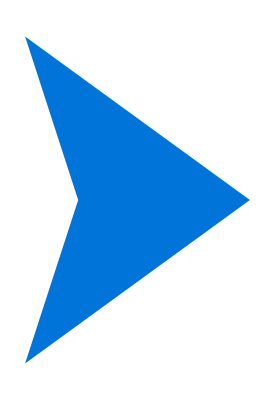

Dart.png

```mathematica
Graphics[(KiteFill/@AddConj@Flatten[KiteBreak/@Inflate[{unitfat},0],1])[[1;;2]]]
Export["Kite.png",%,ImageResolution->300]
Graphics[(KiteFill/@AddConj@Flatten[KiteBreak/@Inflate[{unitfat},0],1])[[3;;4]]]
Export["Dart.png",%,ImageResolution->300]
```

```mathematica
SeeFadedEdges:=Graphics[{EdgeForm[Gray],FaceForm[None],{Transpose[{((IfFat[#1,White,White]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}}]&
```

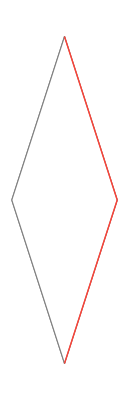

ThinKiteRule.png

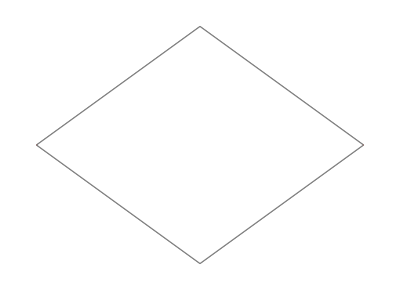

ThickKiteRule.png

```mathematica
Show[Sort@Flatten[{SeeFadedEdges@FullInflate[{#},0],Graphics[{Thick,NiceRed,KitesEdges[#]}]}&/@{Conj@unitskinny,unitskinny}]]
Export["ThinKiteRule.png",%,ImageResolution->300]
Show[Show[Graphics[{Thick,NiceRed,KitesEdges[#]}],SeeFadedEdges@FullInflate[{#},0]]&/@{Conj@unitfat,unitfat}]
Export["ThickKiteRule.png",%,ImageResolution->300]
```

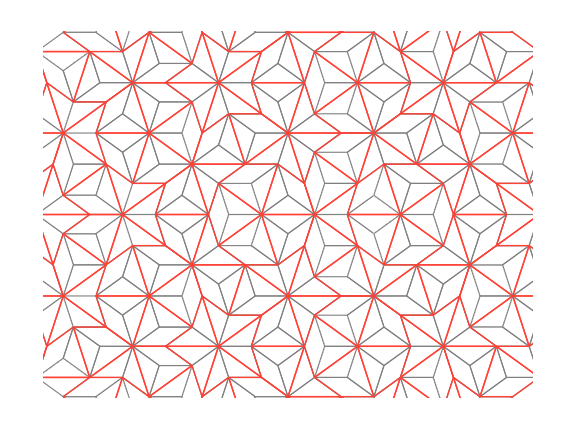

KiteRules.png

```mathematica
Show[SeeFadedEdges@FullInflate[{unitfat},6],Graphics[{NiceRed,Thick,KitesEdges/@AddConj@Inflate[{unitfat},6]}],PlotRange->{{-0.4,0.4},{-0.3,0.3}},ImageSize->Large]
Export["KiteRules.png",%,ImageResolution->300]
```

```mathematica
inflate11=SeeFaded@FullInflate[{unitfat},9];
```

-Graphics-

PatternFind2.png

```mathematica
Show[inflate11,
Graphics[List[Thickness[Large],StrokeForm[NiceRed],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[0.04572085008615734,-0.000057438253877023504],1/2*ϕ^3*0.037219988512349256+0.037219988512349256]]],Graphics[List[Thickness[Large],StrokeForm[NiceGreen],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[0.04572085008615734,-0.000057438253877023504],0.037219988512349256]]],
Graphics[List[Thickness[Large],StrokeForm[NiceBlue],EdgeForm[GrayLevel[0]],EdgeForm[None],Circle[List[0.0002154011847065318,0.13801830910070007],0.037219988512349256]]],
PlotRange->{{-0.4,0.4},{-0.3,0.3}}]
Export["PatternFind3.png",%,Background->None,ImageResolution->200];
```

-Graphics-

```mathematica
graphic={FaceForm[None],Polygon/@Coor/@Δ/@#1}&@FullInflate[starseed,7];
x=0.527; 
(*x=1.91;*)
y=0;
```

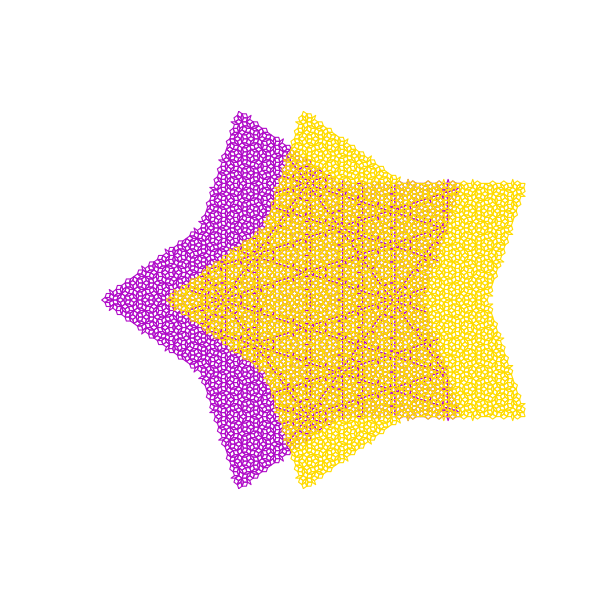

reTranslateFar.png

```mathematica
Show[{Graphics[{EdgeForm[{NicePurple}],graphic},PlotRange->{{-2,2},{-2,2}}],Graphics[Translate[{Opacity[1],EdgeForm[NiceYellow],graphic},{x,0}]]},ImageSize->600]
Export["reTranslateFar.png",%,ImageResolution->300]
```

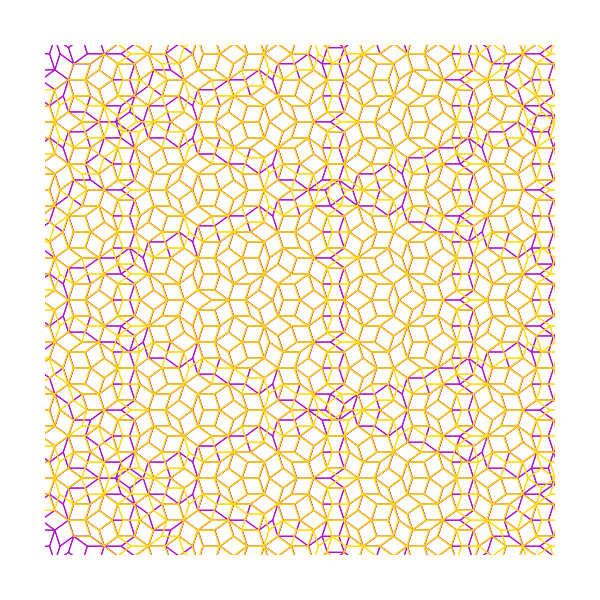

reTranslateClose.png

```mathematica
Show[{Graphics[{EdgeForm[{NicePurple}],graphic},PlotRange->{{-0.5,0.5},{-0.5,0.5}}],Graphics[Translate[{Opacity[1],EdgeForm[NiceYellow],graphic},{x,0}]]},ImageSize->600]
Export["reTranslateClose.png",%,ImageResolution->300]
```

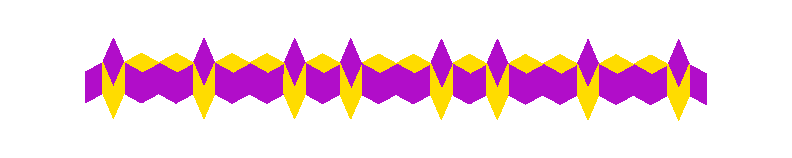

reWorm.png

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.0729328564164158,0.46882723759618633],List[1.0728247117542193,0.41309925252697793],List[1.1257917565558193,0.39577550639263526],List[1.1258999012180158,0.45150349146184354]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.0402642595223277,0.5139756904170022],List[1.0074206808891042,0.46895436927129247],List[1.0400892777831925,0.4238059164504766],List[1.0729328564164158,0.46882723759618633]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[1.0728247117542193,0.41309925252697816],List[1.039981133120996,0.3680779313812684],List[1.0400892777831925,0.4238059164504766],List[1.0729328564164158,0.46882723759618633]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.0074206808891042,0.46895436927129247],List[0.954386799010565,0.4518363265083182],List[0.9542786543483688,0.39610834143910983],List[1.0073125362269078,0.41322638420208424]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[1.0073125362269078,0.41322638420208424],List[1.039981133120996,0.36807793138126826],List[1.0400892777831925,0.4238059164504766],List[1.0074206808891042,0.46895436927129247]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.954386799010565,0.45183632650831806],List[0.9014197542089651,0.46916007264266096],List[0.9544536360875041,0.4862781154056354],List[1.0074206808891042,0.46895436927129247]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.901419754208965,0.46916007264266096],List[0.9013116095467689,0.41343208757345273],List[0.9542786543483688,0.39610834143910983],List[0.954386799010565,0.45183632650831806]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.901419754208965,0.46916007264266096],List[0.8483858723304258,0.4520420298796865],List[0.8482777276682296,0.3963140448104784],List[0.9013116095467689,0.41343208757345273]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.848385872330426,0.4520420298796864],List[0.7954188275288261,0.46936577601402923],List[0.8484527094073651,0.4864838187770037],List[0.901419754208965,0.46916007264266096]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.795418827528826,0.46936577601402935],List[0.7953106828666296,0.4136377909448213],List[0.8482777276682296,0.3963140448104784],List[0.848385872330426,0.4520420298796864]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7627502306347379,0.5145142288348452],List[0.7299066520015145,0.4694929076891353],List[0.7625752488956025,0.42434445486831956],List[0.795418827528826,0.46936577601402935]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.7953106828666298,0.41363779094482106],List[0.7624671042334062,0.3686164697991113],List[0.7625752488956025,0.42434445486831956],List[0.795418827528826,0.46936577601402935]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7299066520015144,0.4694929076891355],List[0.6768727701229753,0.45237486492616114],List[0.6767646254607791,0.3966468798569528],List[0.7297985073393183,0.4137649226199272]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.7297985073393183,0.4137649226199272],List[0.7624671042334062,0.3686164697991113],List[0.7625752488956025,0.42434445486831956],List[0.7299066520015144,0.4694929076891355]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.6768727701229753,0.452374864926161],List[0.6239057253213753,0.4696986110605039],List[0.6769396071999144,0.4868166538234784],List[0.7299066520015144,0.4694929076891355]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.6239057253213753,0.4696986110605039],List[0.6237975806591792,0.41397062599129564],List[0.6767646254607791,0.3966468798569528],List[0.6768727701229753,0.452374864926161]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.6239057253213753,0.4696986110605039],List[0.5708718434428363,0.45258056829752946],List[0.57076369878064,0.3968525832283214],List[0.6237975806591792,0.41397062599129564]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5708718434428363,0.45258056829752946],List[0.5179047986412363,0.4699043144318723],List[0.5709386805197754,0.4870223571948468],List[0.6239057253213753,0.4696986110605039]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.5179047986412363,0.4699043144318724],List[0.5177966539790402,0.4141763293626643],List[0.57076369878064,0.3968525832283214],List[0.5708718434428363,0.45258056829752946]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.48523620174714815,0.5150527672526882],List[0.4523926231139249,0.47003144610697845],List[0.48506122000801294,0.4248829932861627],List[0.5179047986412363,0.4699043144318724]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5177966539790402,0.4141763293626642],List[0.48495307534581683,0.3691550082169543],List[0.48506122000801294,0.4248829932861627],List[0.5179047986412363,0.4699043144318724]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.4523926231139248,0.47003144610697856],List[0.3993587412353858,0.4529134033440041],List[0.39925059657318956,0.3971854182747958],List[0.4522844784517287,0.41430346103777016]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.4522844784517287,0.41430346103777016],List[0.4523926231139249,0.47003144610697845],List[0.48506122000801294,0.4248829932861627],List[0.4849530753458168,0.3691550082169544]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3993587412353858,0.4529134033440041],List[0.3463916964337858,0.4702371494783469],List[0.39942557831232484,0.4873551922413214],List[0.4523926231139248,0.47003144610697856]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.34639169643378576,0.4702371494783469],List[0.34628355177158965,0.41450916440913865],List[0.39925059657318956,0.3971854182747958],List[0.3993587412353858,0.4529134033440041]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.34628355177158965,0.41450916440913865],List[0.31343997313836625,0.369487843263429],List[0.3135481178005624,0.42521582833263727],List[0.34639169643378576,0.4702371494783469]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.3137230995396977,0.5153856022991627],List[0.2808795209064743,0.470364281153453],List[0.3135481178005624,0.42521582833263727],List[0.34639169643378576,0.4702371494783469]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.2808795209064743,0.470364281153453],List[0.2278456390279352,0.4532462383904785],List[0.22773749436573898,0.3975182533212704],List[0.2807713762442781,0.4146362960842448]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2807713762442781,0.4146362960842448],List[0.2808795209064743,0.47036428115345313],List[0.3135481178005624,0.42521582833263727],List[0.31343997313836625,0.369487843263429]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2278456390279352,0.45324623839047856],List[0.17487859422633514,0.4705699845248215],List[0.22791247610487428,0.4876880272877959],List[0.2808795209064743,0.470364281153453]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.17487859422633514,0.4705699845248215],List[0.174770449564139,0.4148419994556132],List[0.22773749436573898,0.3975182533212704],List[0.2278456390279352,0.45324623839047856]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.17487859422633514,0.4705699845248215],List[0.12184471234779605,0.453451941761847],List[0.12173656768559989,0.3977239566926387],List[0.174770449564139,0.4148419994556132]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.12184471234779608,0.45345194176184694],List[0.06887766754619606,0.47077568789618984],List[0.12191154942473517,0.4878937306591644],List[0.17487859422633514,0.4705699845248215]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.0688776675461961,0.4707756878961898],List[0.06876952288399996,0.4150477028269815],List[0.12173656768559989,0.3977239566926387],List[0.12184471234779608,0.45345194176184694]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.06876952288399996,0.4150477028269816],List[0.035925944250776554,0.37002638168127183],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.036209070652107996,0.5159241407170057],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.003365492018884592,0.47090281957129587],List[-0.04966838985965451,0.4537847768083214],List[-0.04977653452185068,0.3980567917391132],List[0.0032573473566884547,0.4151748345020878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.0032573473566884547,0.4151748345020878],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0359259442507765,0.37002638168127183]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.04966838985965448,0.4537847768083214],List[-0.10263543466125441,0.47110852294266437],List[-0.049601552782715344,0.4882265657056388],List[0.003365492018884592,0.47090281957129587]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.10263543466125447,0.47110852294266425],List[-0.10274357932345066,0.41538053787345597],List[-0.04977653452185068,0.3980567917391132],List[-0.04966838985965448,0.4537847768083214]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.1353040315553426,0.5162569757634802],List[-0.16814761018856597,0.4712356546177704],List[-0.13547901329447784,0.4260872017969546],List[-0.10263543466125447,0.47110852294266425]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.10274357932345066,0.4153805378734561],List[-0.13558715795667406,0.37035921672774635],List[-0.13547901329447784,0.4260872017969546],List[-0.10263543466125447,0.47110852294266425]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.16814761018856592,0.4712356546177704],List[-0.221181492067105,0.4541176118547958],List[-0.22128963672930113,0.39838962678558765],List[-0.1682557548507621,0.4155076695485622]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.1682557548507621,0.4155076695485622],List[-0.13558715795667406,0.37035921672774635],List[-0.13547901329447784,0.4260872017969546],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.221181492067105,0.45411761185479593],List[-0.27414853686870483,0.4714413579891388],List[-0.2211146549901659,0.48855940075211324],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.2742566815309012,0.4157133729199305],List[-0.22128963672930113,0.39838962678558765],List[-0.221181492067105,0.45411761185479593]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.32718241874724413,0.45432331522616437],List[-0.3272905634094403,0.39859533015695603],List[-0.2742566815309012,0.4157133729199305]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.32718241874724413,0.45432331522616437],List[-0.38014946354884405,0.47164706136050727],List[-0.327115581670305,0.48876510412348173],List[-0.27414853686870494,0.4714413579891387]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.38014946354884394,0.47164706136050727],List[-0.38025760821104027,0.415919076291299],List[-0.3272905634094403,0.39859533015695603],List[-0.32718241874724413,0.45432331522616437]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.41281806044293207,0.5167955141813231],List[-0.44566163907615547,0.4717741930356134],List[-0.4129930421820674,0.4266257402147975],List[-0.38014946354884394,0.47164706136050727]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.38025760821104027,0.415919076291299],List[-0.4131011868442636,0.3708977551455892],List[-0.4129930421820674,0.4266257402147975],List[-0.38014946354884394,0.47164706136050727]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.44566163907615547,0.4717741930356134],List[-0.4986955209546946,0.45465615027263895],List[-0.4988036656168907,0.39892816520343066],List[-0.44576978373835174,0.4160462079664051]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.44576978373835174,0.4160462079664051],List[-0.4131011868442636,0.3708977551455892],List[-0.4129930421820674,0.4266257402147975],List[-0.44566163907615547,0.4717741930356134]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4986955209546946,0.45465615027263895],List[-0.5516625657562946,0.4719798964069818],List[-0.4986286838777554,0.4890979391699562],List[-0.44566163907615547,0.4717741930356134]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5516625657562946,0.4719798964069818],List[-0.5517707104184908,0.41625191133777356],List[-0.4988036656168907,0.39892816520343066],List[-0.4986955209546946,0.45465615027263895]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5516625657562946,0.4719798964069818],List[-0.6046964476348338,0.4548618536440074],List[-0.6048045922970299,0.39913386857479916],List[-0.5517707104184908,0.41625191133777356]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.6046964476348337,0.4548618536440074],List[-0.6576634924364337,0.4721855997783503],List[-0.6046296105578945,0.4893036425413247],List[-0.5516625657562946,0.4719798964069818]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.6576634924364336,0.4721855997783503],List[-0.6577716370986298,0.41645761470914194],List[-0.6048045922970299,0.39913386857479916],List[-0.6046964476348337,0.4548618536440074]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.6903320893305217,0.517334052599166],List[-0.7231756679637451,0.4723127314534563],List[-0.6905070710696569,0.4271642786326404],List[-0.6576634924364336,0.4721855997783503]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.6577716370986298,0.41645761470914194],List[-0.6906152157318531,0.3714362935634322],List[-0.6905070710696569,0.4271642786326404],List[-0.6576634924364336,0.4721855997783503]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.7231756679637451,0.4723127314534563],List[-0.7762095498422842,0.4551946886904818],List[-0.7763176945044803,0.3994667036212737],List[-0.7232838126259412,0.41658474638424803]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.7232838126259412,0.41658474638424803],List[-0.690615215731853,0.3714362935634322],List[-0.6905070710696569,0.4271642786326404],List[-0.7231756679637451,0.4723127314534563]]]]],Rule[ImagePadding,List[List[0.,0.],List[0.,0.]]],Rule[ImageSize,List[792.7272727272739,Automatic]],Rule[PlotRange,List[List[-0.8161688940061802,1.1655728479126735],List[0.32533193536063676,0.5600786943007598]]],Rule[PlotRangePadding,Automatic]]
Export["reWorm.png",%,ImageResolution->300]
```

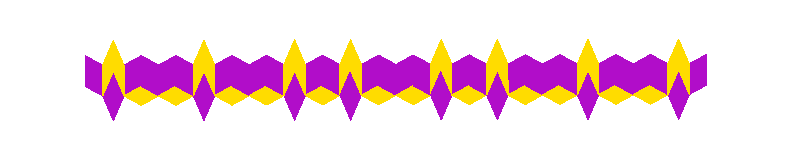

reWormDown.png

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.7234392987635927,0.4119687393985594],List[-0.7235177166259348,0.4676967742264693],List[-0.7765424597414682,0.4848431042324375],List[-0.7764640418791259,0.42911506940452765]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.6906197403692083,0.3669299050226627],List[-0.6579270647414188,0.4120609251245618],List[-0.6907466231358037,0.4570997595004586],List[-0.7234392987635927,0.4119687393985594]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.7235177166259348,0.4676967742264691],List[-0.6908250409981458,0.5128277943283683],List[-0.6907466231358037,0.4570997595004586],List[-0.7234392987635927,0.4119687393985594]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.6579270647414188,0.4120609251245618],List[-0.6049507865301385,0.4293564147684795],List[-0.605029204392481,0.48508444959638936],List[-0.658005482603761,0.4677889599524716]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.658005482603761,0.4677889599524716],List[-0.6908250409981458,0.5128277943283686],List[-0.6907466231358037,0.4570997595004586],List[-0.6579270647414188,0.4120609251245618]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.6049507865301385,0.42935641476847963],List[-0.5519260434146054,0.41221008476251136],List[-0.6049023216258856,0.3949145951185935],List[-0.6579270647414188,0.4120609251245618]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5519260434146053,0.41221008476251136],List[-0.5520044612769478,0.46793811959042114],List[-0.605029204392481,0.48508444959638936],List[-0.6049507865301385,0.42935641476847963]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5519260434146053,0.41221008476251136],List[-0.4989497652033247,0.42950557440642917],List[-0.4990281830656671,0.4852336092343388],List[-0.5520044612769478,0.46793811959042114]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4989497652033248,0.4295055744064293],List[-0.44592502208779167,0.412359244400461],List[-0.498901300299072,0.3950637547565432],List[-0.5519260434146053,0.41221008476251136]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.44592502208779156,0.4123592444004609],List[-0.4460034399501338,0.46808727922837046],List[-0.4990281830656671,0.4852336092343388],List[-0.4989497652033248,0.4295055744064293]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.4131054636934072,0.3673204100245643],List[-0.38041278806561823,0.4124514301264635],List[-0.4132323464600024,0.45749026450236013],List[-0.44592502208779156,0.4123592444004609]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4460034399501339,0.4680872792283707],List[-0.4133107643223448,0.5132182993302699],List[-0.4132323464600024,0.45749026450236013],List[-0.44592502208779156,0.4123592444004609]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.3804127880656181,0.41245143012646335],List[-0.3274365098543377,0.42974691977038104],List[-0.32751492771668,0.485474954598291],List[-0.3804912059279607,0.4681794649543732]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.3804912059279607,0.4681794649543732],List[-0.4133107643223448,0.5132182993302699],List[-0.4132323464600024,0.45749026450236013],List[-0.3804127880656181,0.41245143012646335]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.3274365098543377,0.42974691977038115],List[-0.27441176673880435,0.41260058976441294],List[-0.32738804495008483,0.395305100120495],List[-0.3804127880656181,0.41245143012646335]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27441176673880435,0.41260058976441294],List[-0.27449018460114705,0.46832862459232266],List[-0.32751492771668,0.485474954598291],List[-0.3274365098543377,0.42974691977038115]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27441176673880435,0.41260058976441294],List[-0.2214354885275239,0.4298960794083307],List[-0.22151390638986637,0.4856241142362403],List[-0.27449018460114705,0.46832862459232266]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.2214354885275239,0.4298960794083307],List[-0.1684107454119906,0.4127497494023625],List[-0.22138702362327117,0.39545425975844456],List[-0.27441176673880435,0.41260058976441294]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.1684107454119906,0.41274974940236236],List[-0.1684891632743333,0.46847778423027203],List[-0.22151390638986637,0.4856241142362403],List[-0.2214354885275239,0.4298960794083307]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.13559118701760633,0.36771091502646563],List[-0.10289851138981747,0.4128419351283649],List[-0.1357180697842017,0.45788076950426154],List[-0.1684107454119906,0.41274974940236236]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.1684891632743333,0.46847778423027214],List[-0.1357964876465442,0.5136088043321714],List[-0.1357180697842017,0.45788076950426154],List[-0.1684107454119906,0.41274974940236236]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.10289851138981736,0.4128419351283648],List[-0.049922233178536904,0.4301374247722826],List[-0.050000651040879425,0.48586545960019245],List[-0.10297692925215989,0.4685699699562747]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.10297692925215989,0.4685699699562747],List[-0.10289851138981747,0.4128419351283649],List[-0.1357180697842017,0.45788076950426154],List[-0.13579648764654415,0.5136088043321713]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.049922233178536904,0.4301374247722826],List[0.0031025099369962725,0.4129910947663144],List[-0.04987376827428408,0.39569560512239654],List[-0.10289851138981736,0.4128419351283648]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.003102509936996328,0.4129910947663144],List[0.003024092074653806,0.4687191295942242],List[-0.050000651040879425,0.48586545960019245],List[-0.049922233178536904,0.4301374247722826]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.003024092074653806,0.4687191295942242],List[0.03571676770244289,0.5138501496961233],List[0.035795185564785365,0.45812211486821347],List[0.003102509936996328,0.4129910947663144]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.035922068331380654,0.3679522603904177],List[0.06861474395916968,0.41308328049231685],List[0.035795185564785365,0.45812211486821347],List[0.003102509936996328,0.4129910947663144]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.06861474395916968,0.41308328049231685],List[0.12159102217045017,0.4303787701362347],List[0.1215126043081077,0.4861068049641444],List[0.06853632609682722,0.4688113153202265]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.06853632609682722,0.4688113153202265],List[0.06861474395916968,0.41308328049231674],List[0.035795185564785365,0.45812211486821347],List[0.03571676770244289,0.5138501496961233]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.12159102217045017,0.43037877013623466],List[0.1746157652859835,0.41323244013026633],List[0.12163948707470297,0.3959369504863486],List[0.06861474395916968,0.41308328049231685]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.1746157652859835,0.41323244013026633],List[0.174537347423641,0.46896047495817617],List[0.1215126043081077,0.4861068049641444],List[0.12159102217045017,0.43037877013623466]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.1746157652859835,0.41323244013026633],List[0.22759204349726395,0.4305279297741842],List[0.22751362563492145,0.4862559646020941],List[0.174537347423641,0.46896047495817617]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.22759204349726395,0.43052792977418425],List[0.2806167866127972,0.413381599768216],List[0.22764050840151673,0.39608611012429795],List[0.1746157652859835,0.41323244013026633]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.28061678661279715,0.41338159976821603],List[0.2805383687504547,0.46910963459612587],List[0.22751362563492145,0.4862559646020941],List[0.22759204349726395,0.43052792977418425]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2805383687504547,0.46910963459612576],List[0.31323104437824373,0.5142406546980248],List[0.3133094622405862,0.45851261987011505],List[0.28061678661279715,0.41338159976821603]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.3134363450071815,0.36834276539231925],List[0.3461290206349706,0.4134737854942184],List[0.3133094622405862,0.45851261987011505],List[0.28061678661279715,0.41338159976821603]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.34612902063497053,0.4134737854942185],List[0.39910529884625107,0.4307692751381364],List[0.39902688098390854,0.4864973099660461],List[0.346050602772628,0.4692018203221281]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.346050602772628,0.4692018203221281],List[0.3461290206349706,0.4134737854942184],List[0.3133094622405862,0.45851261987011505],List[0.3132310443782438,0.5142406546980248]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.399105298846251,0.4307692751381364],List[0.45213004196178425,0.41362294513216796],List[0.39915376375050377,0.39632745548825016],List[0.34612902063497053,0.4134737854942185]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.45213004196178425,0.4136229451321681],List[0.4520516240994417,0.4693509799600779],List[0.39902688098390854,0.4864973099660461],List[0.399105298846251,0.4307692751381364]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.48494960035616863,0.3685841107562713],List[0.5176422759839576,0.4137151308581705],List[0.48482271758957335,0.4587539652340672],List[0.45213004196178425,0.4136229451321681]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.4520516240994417,0.4693509799600778],List[0.4847442997272308,0.514482000061977],List[0.48482271758957335,0.4587539652340672],List[0.45213004196178425,0.4136229451321681]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.5176422759839576,0.4137151308581705],List[0.5706185541952381,0.43101062050208844],List[0.5705401363328955,0.48673865532999816],List[0.5175638581216151,0.46944316568608024]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5175638581216151,0.46944316568608024],List[0.4847442997272308,0.514482000061977],List[0.48482271758957335,0.4587539652340672],List[0.5176422759839576,0.4137151308581705]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5706185541952381,0.4310106205020883],List[0.6236432973107712,0.4138642904961201],List[0.5706670190994908,0.3965688008522023],List[0.5176422759839576,0.4137151308581705]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.6236432973107713,0.41386429049612017],List[0.6235648794484289,0.46959232532402995],List[0.5705401363328955,0.48673865532999816],List[0.5706185541952381,0.4310106205020883]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.6236432973107713,0.41386429049612017],List[0.6766195755220518,0.4311597801400379],List[0.6765411576597092,0.48688781496794775],List[0.6235648794484289,0.46959232532402995]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.6766195755220518,0.4311597801400379],List[0.7296443186375849,0.4140134501340696],List[0.6766680404263047,0.3967179604901518],List[0.6236432973107713,0.41386429049612017]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7296443186375848,0.41401345013406954],List[0.7295659007752426,0.4697414849619793],List[0.6765411576597092,0.48688781496794775],List[0.6766195755220518,0.4311597801400379]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7624638770319692,0.3689746157581729],List[0.7951565526597584,0.41410563586007204],List[0.7623369942653739,0.4591444702359688],List[0.7296443186375848,0.41401345013406954]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.7295659007752426,0.4697414849619793],List[0.7622585764030316,0.5148725050638787],List[0.7623369942653739,0.4591444702359688],List[0.7296443186375848,0.41401345013406954]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.7951565526597584,0.41410563586007204],List[0.8481328308710387,0.4314011255039898],List[0.8480544130086962,0.4871291603318997],List[0.795078134797416,0.4698336706879819]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.795078134797416,0.4698336706879819],List[0.7622585764030316,0.5148725050638787],List[0.7623369942653739,0.4591444702359688],List[0.7951565526597584,0.41410563586007204]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.8481328308710387,0.4314011255039898],List[0.901157573986572,0.4142547954980215],List[0.8481812957752916,0.3969593058541038],List[0.7951565526597584,0.41410563586007204]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.901157573986572,0.4142547954980215],List[0.9010791561242296,0.46998283032593136],List[0.8480544130086962,0.4871291603318997],List[0.8481328308710387,0.4314011255039898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.901157573986572,0.4142547954980215],List[0.9541338521978525,0.4315502851419394],List[0.9540554343355101,0.4872783199698491],List[0.9010791561242296,0.46998283032593136]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.9541338521978524,0.4315502851419394],List[1.007158595313386,0.414403955135971],List[0.9541823171021052,0.39710846549205325],List[0.901157573986572,0.4142547954980215]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.007158595313386,0.414403955135971],List[1.0070801774510434,0.47013198996388095],List[0.9540554343355101,0.4872783199698491],List[0.9541338521978524,0.4315502851419394]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.03997815370777,0.36936512076007455],List[1.072670829335559,0.4144961408619736],List[1.039851270941175,0.45953497523787035],List[1.007158595313386,0.414403955135971]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[1.0070801774510434,0.47013198996388095],List[1.0397728530788324,0.5152630100657801],List[1.039851270941175,0.45953497523787035],List[1.007158595313386,0.414403955135971]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[1.072670829335559,0.4144961408619736],List[1.1256471075468395,0.4317916305058915],List[1.125568689684497,0.48751966533380114],List[1.0725924114732164,0.47022417568988345]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[1.0725924114732164,0.47022417568988345],List[1.0397728530788324,0.5152630100657801],List[1.039851270941175,0.45953497523787035],List[1.072670829335559,0.4144961408619736]]]]],Rule[ImagePadding,List[List[0.,0.],List[0.,0.]]],Rule[ImageSize,List[792.7272727272739,Automatic]],Rule[PlotRange,List[List[-0.8161688940061802,1.1655728479126735],List[0.32533193536063676,0.5600786943007598]]],Rule[PlotRangePadding,Automatic]]
QuickExport["reWormDown.png"]
```

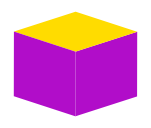

reWideWorm.png

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.16814761018856592,0.4712356546177704],List[-0.221181492067105,0.4541176118547958],List[-0.22128963672930113,0.39838962678558765],List[-0.1682557548507621,0.4155076695485622]]]],List[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.221181492067105,0.45411761185479593],List[-0.27414853686870483,0.4714413579891388],List[-0.2211146549901659,0.48855940075211324],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.2742566815309012,0.4157133729199305],List[-0.22128963672930113,0.39838962678558765],List[-0.221181492067105,0.45411761185479593]]]]]],Rule[ImageSize,List[151.81818181818193,Automatic]]]
QuickExport["reWideWorm.png"]
```

```mathematica
Graphics[List[List[List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.06876952288399996,0.4150477028269816],List[0.035925944250776554,0.37002638168127183],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.036209070652107996,0.5159241407170057],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.0032573473566884547,0.4151748345020878],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0359259442507765,0.37002638168127183]]]]],Rule[ImageSize,List[104.76448052380978,Automatic]]]
QuickExport["reTallWorm.png"]
```

-Graphics-

reTallWorm.png

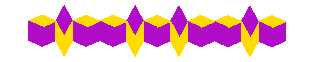

reValidWorm0.png

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.4523926231139248,0.47003144610697856],List[0.3993587412353858,0.4529134033440041],List[0.39925059657318956,0.3971854182747958],List[0.4522844784517287,0.41430346103777016]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3993587412353858,0.4529134033440041],List[0.3463916964337858,0.4702371494783469],List[0.39942557831232484,0.4873551922413214],List[0.4523926231139248,0.47003144610697856]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.34639169643378576,0.4702371494783469],List[0.34628355177158965,0.41450916440913865],List[0.39925059657318956,0.3971854182747958],List[0.3993587412353858,0.4529134033440041]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.34628355177158965,0.41450916440913865],List[0.31343997313836625,0.369487843263429],List[0.3135481178005624,0.42521582833263727],List[0.34639169643378576,0.4702371494783469]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.3137230995396977,0.5153856022991627],List[0.2808795209064743,0.470364281153453],List[0.3135481178005624,0.42521582833263727],List[0.34639169643378576,0.4702371494783469]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.2808795209064743,0.470364281153453],List[0.2278456390279352,0.4532462383904785],List[0.22773749436573898,0.3975182533212704],List[0.2807713762442781,0.4146362960842448]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2807713762442781,0.4146362960842448],List[0.2808795209064743,0.47036428115345313],List[0.3135481178005624,0.42521582833263727],List[0.31343997313836625,0.369487843263429]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2278456390279352,0.45324623839047856],List[0.17487859422633514,0.4705699845248215],List[0.22791247610487428,0.4876880272877959],List[0.2808795209064743,0.470364281153453]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.17487859422633514,0.4705699845248215],List[0.174770449564139,0.4148419994556132],List[0.22773749436573898,0.3975182533212704],List[0.2278456390279352,0.45324623839047856]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.17487859422633514,0.4705699845248215],List[0.12184471234779605,0.453451941761847],List[0.12173656768559989,0.3977239566926387],List[0.174770449564139,0.4148419994556132]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.12184471234779608,0.45345194176184694],List[0.06887766754619606,0.47077568789618984],List[0.12191154942473517,0.4878937306591644],List[0.17487859422633514,0.4705699845248215]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.0688776675461961,0.4707756878961898],List[0.06876952288399996,0.4150477028269815],List[0.12173656768559989,0.3977239566926387],List[0.12184471234779608,0.45345194176184694]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.06876952288399996,0.4150477028269816],List[0.035925944250776554,0.37002638168127183],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.036209070652107996,0.5159241407170057],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.003365492018884592,0.47090281957129587],List[-0.04966838985965451,0.4537847768083214],List[-0.04977653452185068,0.3980567917391132],List[0.0032573473566884547,0.4151748345020878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.0032573473566884547,0.4151748345020878],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0359259442507765,0.37002638168127183]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.04966838985965448,0.4537847768083214],List[-0.10263543466125441,0.47110852294266437],List[-0.049601552782715344,0.4882265657056388],List[0.003365492018884592,0.47090281957129587]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.10263543466125447,0.47110852294266425],List[-0.10274357932345066,0.41538053787345597],List[-0.04977653452185068,0.3980567917391132],List[-0.04966838985965448,0.4537847768083214]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.1353040315553426,0.5162569757634802],List[-0.16814761018856597,0.4712356546177704],List[-0.13547901329447784,0.4260872017969546],List[-0.10263543466125447,0.47110852294266425]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.10274357932345066,0.4153805378734561],List[-0.13558715795667406,0.37035921672774635],List[-0.13547901329447784,0.4260872017969546],List[-0.10263543466125447,0.47110852294266425]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.16814761018856592,0.4712356546177704],List[-0.221181492067105,0.4541176118547958],List[-0.22128963672930113,0.39838962678558765],List[-0.1682557548507621,0.4155076695485622]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.1682557548507621,0.4155076695485622],List[-0.13558715795667406,0.37035921672774635],List[-0.13547901329447784,0.4260872017969546],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.221181492067105,0.45411761185479593],List[-0.27414853686870483,0.4714413579891388],List[-0.2211146549901659,0.48855940075211324],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.2742566815309012,0.4157133729199305],List[-0.22128963672930113,0.39838962678558765],List[-0.221181492067105,0.45411761185479593]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.32718241874724413,0.45432331522616437],List[-0.3272905634094403,0.39859533015695603],List[-0.2742566815309012,0.4157133729199305]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.32718241874724413,0.45432331522616437],List[-0.38014946354884405,0.47164706136050727],List[-0.327115581670305,0.48876510412348173],List[-0.27414853686870494,0.4714413579891387]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.38014946354884394,0.47164706136050727],List[-0.38025760821104027,0.415919076291299],List[-0.3272905634094403,0.39859533015695603],List[-0.32718241874724413,0.45432331522616437]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.41281806044293207,0.5167955141813231],List[-0.44566163907615547,0.4717741930356134],List[-0.4129930421820674,0.4266257402147975],List[-0.38014946354884394,0.47164706136050727]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.38025760821104027,0.415919076291299],List[-0.4131011868442636,0.3708977551455892],List[-0.4129930421820674,0.4266257402147975],List[-0.38014946354884394,0.47164706136050727]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.44566163907615547,0.4717741930356134],List[-0.4986955209546946,0.45465615027263895],List[-0.4988036656168907,0.39892816520343066],List[-0.44576978373835174,0.4160462079664051]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.44576978373835174,0.4160462079664051],List[-0.4131011868442636,0.3708977551455892],List[-0.4129930421820674,0.4266257402147975],List[-0.44566163907615547,0.4717741930356134]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4986955209546946,0.45465615027263895],List[-0.5516625657562946,0.4719798964069818],List[-0.4986286838777554,0.4890979391699562],List[-0.44566163907615547,0.4717741930356134]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5516625657562946,0.4719798964069818],List[-0.5517707104184908,0.41625191133777356],List[-0.4988036656168907,0.39892816520343066],List[-0.4986955209546946,0.45465615027263895]]]]],Rule[ImageSize,List[314.54545454545456,Automatic]]]
QuickExport["reValidWorm0.png"]
```

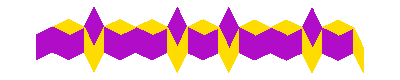

reValidWorm1.png

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.4523926231139248,0.47003144610697856],List[0.3993587412353858,0.4529134033440041],List[0.39925059657318956,0.3971854182747958],List[0.4522844784517287,0.41430346103777016]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.4522844784517287,0.41430346103777016],List[0.4523926231139249,0.47003144610697845],List[0.48506122000801294,0.4248829932861627],List[0.4849530753458168,0.3691550082169544]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3993587412353858,0.4529134033440041],List[0.3463916964337858,0.4702371494783469],List[0.39942557831232484,0.4873551922413214],List[0.4523926231139248,0.47003144610697856]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.34639169643378576,0.4702371494783469],List[0.34628355177158965,0.41450916440913865],List[0.39925059657318956,0.3971854182747958],List[0.3993587412353858,0.4529134033440041]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.34628355177158965,0.41450916440913865],List[0.31343997313836625,0.369487843263429],List[0.3135481178005624,0.42521582833263727],List[0.34639169643378576,0.4702371494783469]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.3137230995396977,0.5153856022991627],List[0.2808795209064743,0.470364281153453],List[0.3135481178005624,0.42521582833263727],List[0.34639169643378576,0.4702371494783469]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.2808795209064743,0.470364281153453],List[0.2278456390279352,0.4532462383904785],List[0.22773749436573898,0.3975182533212704],List[0.2807713762442781,0.4146362960842448]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2807713762442781,0.4146362960842448],List[0.2808795209064743,0.47036428115345313],List[0.3135481178005624,0.42521582833263727],List[0.31343997313836625,0.369487843263429]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2278456390279352,0.45324623839047856],List[0.17487859422633514,0.4705699845248215],List[0.22791247610487428,0.4876880272877959],List[0.2808795209064743,0.470364281153453]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.17487859422633514,0.4705699845248215],List[0.174770449564139,0.4148419994556132],List[0.22773749436573898,0.3975182533212704],List[0.2278456390279352,0.45324623839047856]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.17487859422633514,0.4705699845248215],List[0.12184471234779605,0.453451941761847],List[0.12173656768559989,0.3977239566926387],List[0.174770449564139,0.4148419994556132]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.12184471234779608,0.45345194176184694],List[0.06887766754619606,0.47077568789618984],List[0.12191154942473517,0.4878937306591644],List[0.17487859422633514,0.4705699845248215]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.0688776675461961,0.4707756878961898],List[0.06876952288399996,0.4150477028269815],List[0.12173656768559989,0.3977239566926387],List[0.12184471234779608,0.45345194176184694]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.06876952288399996,0.4150477028269816],List[0.035925944250776554,0.37002638168127183],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.036209070652107996,0.5159241407170057],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.003365492018884592,0.47090281957129587],List[-0.04966838985965451,0.4537847768083214],List[-0.04977653452185068,0.3980567917391132],List[0.0032573473566884547,0.4151748345020878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.0032573473566884547,0.4151748345020878],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0359259442507765,0.37002638168127183]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.04966838985965448,0.4537847768083214],List[-0.10263543466125441,0.47110852294266437],List[-0.049601552782715344,0.4882265657056388],List[0.003365492018884592,0.47090281957129587]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.10263543466125447,0.47110852294266425],List[-0.10274357932345066,0.41538053787345597],List[-0.04977653452185068,0.3980567917391132],List[-0.04966838985965448,0.4537847768083214]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.1353040315553426,0.5162569757634802],List[-0.16814761018856597,0.4712356546177704],List[-0.13547901329447784,0.4260872017969546],List[-0.10263543466125447,0.47110852294266425]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.10274357932345066,0.4153805378734561],List[-0.13558715795667406,0.37035921672774635],List[-0.13547901329447784,0.4260872017969546],List[-0.10263543466125447,0.47110852294266425]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.16814761018856592,0.4712356546177704],List[-0.221181492067105,0.4541176118547958],List[-0.22128963672930113,0.39838962678558765],List[-0.1682557548507621,0.4155076695485622]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.1682557548507621,0.4155076695485622],List[-0.13558715795667406,0.37035921672774635],List[-0.13547901329447784,0.4260872017969546],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.221181492067105,0.45411761185479593],List[-0.27414853686870483,0.4714413579891388],List[-0.2211146549901659,0.48855940075211324],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.2742566815309012,0.4157133729199305],List[-0.22128963672930113,0.39838962678558765],List[-0.221181492067105,0.45411761185479593]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.32718241874724413,0.45432331522616437],List[-0.3272905634094403,0.39859533015695603],List[-0.2742566815309012,0.4157133729199305]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.32718241874724413,0.45432331522616437],List[-0.38014946354884405,0.47164706136050727],List[-0.327115581670305,0.48876510412348173],List[-0.27414853686870494,0.4714413579891387]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.38014946354884394,0.47164706136050727],List[-0.38025760821104027,0.415919076291299],List[-0.3272905634094403,0.39859533015695603],List[-0.32718241874724413,0.45432331522616437]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.41281806044293207,0.5167955141813231],List[-0.44566163907615547,0.4717741930356134],List[-0.4129930421820674,0.4266257402147975],List[-0.38014946354884394,0.47164706136050727]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.38025760821104027,0.415919076291299],List[-0.4131011868442636,0.3708977551455892],List[-0.4129930421820674,0.4266257402147975],List[-0.38014946354884394,0.47164706136050727]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.44566163907615547,0.4717741930356134],List[-0.4986955209546946,0.45465615027263895],List[-0.4988036656168907,0.39892816520343066],List[-0.44576978373835174,0.4160462079664051]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.44576978373835174,0.4160462079664051],List[-0.4131011868442636,0.3708977551455892],List[-0.4129930421820674,0.4266257402147975],List[-0.44566163907615547,0.4717741930356134]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4986955209546946,0.45465615027263895],List[-0.5516625657562946,0.4719798964069818],List[-0.4986286838777554,0.4890979391699562],List[-0.44566163907615547,0.4717741930356134]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5516625657562946,0.4719798964069818],List[-0.5517707104184908,0.41625191133777356],List[-0.4988036656168907,0.39892816520343066],List[-0.4986955209546946,0.45465615027263895]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5516625657562946,0.4719798964069818],List[-0.6046964476348338,0.4548618536440074],List[-0.6048045922970299,0.39913386857479916],List[-0.5517707104184908,0.41625191133777356]]]]]]
QuickExport["reValidWorm1.png"]
```

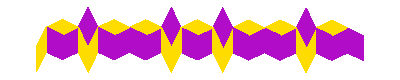

reValidWorm2.png

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.4523926231139248,0.47003144610697856],List[0.3993587412353858,0.4529134033440041],List[0.39925059657318956,0.3971854182747958],List[0.4522844784517287,0.41430346103777016]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3993587412353858,0.4529134033440041],List[0.3463916964337858,0.4702371494783469],List[0.39942557831232484,0.4873551922413214],List[0.4523926231139248,0.47003144610697856]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.34639169643378576,0.4702371494783469],List[0.34628355177158965,0.41450916440913865],List[0.39925059657318956,0.3971854182747958],List[0.3993587412353858,0.4529134033440041]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.34628355177158965,0.41450916440913865],List[0.31343997313836625,0.369487843263429],List[0.3135481178005624,0.42521582833263727],List[0.34639169643378576,0.4702371494783469]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.3137230995396977,0.5153856022991627],List[0.2808795209064743,0.470364281153453],List[0.3135481178005624,0.42521582833263727],List[0.34639169643378576,0.4702371494783469]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.2808795209064743,0.470364281153453],List[0.2278456390279352,0.4532462383904785],List[0.22773749436573898,0.3975182533212704],List[0.2807713762442781,0.4146362960842448]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2807713762442781,0.4146362960842448],List[0.2808795209064743,0.47036428115345313],List[0.3135481178005624,0.42521582833263727],List[0.31343997313836625,0.369487843263429]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2278456390279352,0.45324623839047856],List[0.17487859422633514,0.4705699845248215],List[0.22791247610487428,0.4876880272877959],List[0.2808795209064743,0.470364281153453]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.17487859422633514,0.4705699845248215],List[0.174770449564139,0.4148419994556132],List[0.22773749436573898,0.3975182533212704],List[0.2278456390279352,0.45324623839047856]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.17487859422633514,0.4705699845248215],List[0.12184471234779605,0.453451941761847],List[0.12173656768559989,0.3977239566926387],List[0.174770449564139,0.4148419994556132]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.12184471234779608,0.45345194176184694],List[0.06887766754619606,0.47077568789618984],List[0.12191154942473517,0.4878937306591644],List[0.17487859422633514,0.4705699845248215]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.0688776675461961,0.4707756878961898],List[0.06876952288399996,0.4150477028269815],List[0.12173656768559989,0.3977239566926387],List[0.12184471234779608,0.45345194176184694]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.06876952288399996,0.4150477028269816],List[0.035925944250776554,0.37002638168127183],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.036209070652107996,0.5159241407170057],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.003365492018884592,0.47090281957129587],List[-0.04966838985965451,0.4537847768083214],List[-0.04977653452185068,0.3980567917391132],List[0.0032573473566884547,0.4151748345020878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.0032573473566884547,0.4151748345020878],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0359259442507765,0.37002638168127183]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.04966838985965448,0.4537847768083214],List[-0.10263543466125441,0.47110852294266437],List[-0.049601552782715344,0.4882265657056388],List[0.003365492018884592,0.47090281957129587]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.10263543466125447,0.47110852294266425],List[-0.10274357932345066,0.41538053787345597],List[-0.04977653452185068,0.3980567917391132],List[-0.04966838985965448,0.4537847768083214]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.1353040315553426,0.5162569757634802],List[-0.16814761018856597,0.4712356546177704],List[-0.13547901329447784,0.4260872017969546],List[-0.10263543466125447,0.47110852294266425]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.10274357932345066,0.4153805378734561],List[-0.13558715795667406,0.37035921672774635],List[-0.13547901329447784,0.4260872017969546],List[-0.10263543466125447,0.47110852294266425]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.16814761018856592,0.4712356546177704],List[-0.221181492067105,0.4541176118547958],List[-0.22128963672930113,0.39838962678558765],List[-0.1682557548507621,0.4155076695485622]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.1682557548507621,0.4155076695485622],List[-0.13558715795667406,0.37035921672774635],List[-0.13547901329447784,0.4260872017969546],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.221181492067105,0.45411761185479593],List[-0.27414853686870483,0.4714413579891388],List[-0.2211146549901659,0.48855940075211324],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.2742566815309012,0.4157133729199305],List[-0.22128963672930113,0.39838962678558765],List[-0.221181492067105,0.45411761185479593]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.32718241874724413,0.45432331522616437],List[-0.3272905634094403,0.39859533015695603],List[-0.2742566815309012,0.4157133729199305]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.32718241874724413,0.45432331522616437],List[-0.38014946354884405,0.47164706136050727],List[-0.327115581670305,0.48876510412348173],List[-0.27414853686870494,0.4714413579891387]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.38014946354884394,0.47164706136050727],List[-0.38025760821104027,0.415919076291299],List[-0.3272905634094403,0.39859533015695603],List[-0.32718241874724413,0.45432331522616437]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.41281806044293207,0.5167955141813231],List[-0.44566163907615547,0.4717741930356134],List[-0.4129930421820674,0.4266257402147975],List[-0.38014946354884394,0.47164706136050727]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.38025760821104027,0.415919076291299],List[-0.4131011868442636,0.3708977551455892],List[-0.4129930421820674,0.4266257402147975],List[-0.38014946354884394,0.47164706136050727]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.44566163907615547,0.4717741930356134],List[-0.4986955209546946,0.45465615027263895],List[-0.4988036656168907,0.39892816520343066],List[-0.44576978373835174,0.4160462079664051]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.44576978373835174,0.4160462079664051],List[-0.4131011868442636,0.3708977551455892],List[-0.4129930421820674,0.4266257402147975],List[-0.44566163907615547,0.4717741930356134]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4986955209546946,0.45465615027263895],List[-0.5516625657562946,0.4719798964069818],List[-0.4986286838777554,0.4890979391699562],List[-0.44566163907615547,0.4717741930356134]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5516625657562946,0.4719798964069818],List[-0.5517707104184908,0.41625191133777356],List[-0.4988036656168907,0.39892816520343066],List[-0.4986955209546946,0.45465615027263895]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5520417060699779,0.417370310190975],List[-0.5848852847032014,0.3723489890452653],List[-0.5847771400410052,0.4280769741144736],List[-0.5519335614077819,0.4730982952601832]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.45198709595475484,0.4696623103465333],List[0.4518789512925586,0.413934325277325],List[0.5048459960941586,0.3966105791429822],List[0.5049541407563548,0.45233856421219043]]]]]]
QuickExport["reValidWorm2.png"]
```

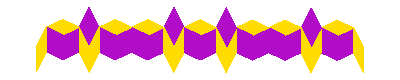

reInvalidWorm.png

```mathematica
Graphics[List[List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.4523926231139248,0.47003144610697856],List[0.3993587412353858,0.4529134033440041],List[0.39925059657318956,0.3971854182747958],List[0.4522844784517287,0.41430346103777016]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3993587412353858,0.4529134033440041],List[0.3463916964337858,0.4702371494783469],List[0.39942557831232484,0.4873551922413214],List[0.4523926231139248,0.47003144610697856]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.34639169643378576,0.4702371494783469],List[0.34628355177158965,0.41450916440913865],List[0.39925059657318956,0.3971854182747958],List[0.3993587412353858,0.4529134033440041]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.34628355177158965,0.41450916440913865],List[0.31343997313836625,0.369487843263429],List[0.3135481178005624,0.42521582833263727],List[0.34639169643378576,0.4702371494783469]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.3137230995396977,0.5153856022991627],List[0.2808795209064743,0.470364281153453],List[0.3135481178005624,0.42521582833263727],List[0.34639169643378576,0.4702371494783469]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.2808795209064743,0.470364281153453],List[0.2278456390279352,0.4532462383904785],List[0.22773749436573898,0.3975182533212704],List[0.2807713762442781,0.4146362960842448]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2807713762442781,0.4146362960842448],List[0.2808795209064743,0.47036428115345313],List[0.3135481178005624,0.42521582833263727],List[0.31343997313836625,0.369487843263429]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2278456390279352,0.45324623839047856],List[0.17487859422633514,0.4705699845248215],List[0.22791247610487428,0.4876880272877959],List[0.2808795209064743,0.470364281153453]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.17487859422633514,0.4705699845248215],List[0.174770449564139,0.4148419994556132],List[0.22773749436573898,0.3975182533212704],List[0.2278456390279352,0.45324623839047856]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.17487859422633514,0.4705699845248215],List[0.12184471234779605,0.453451941761847],List[0.12173656768559989,0.3977239566926387],List[0.174770449564139,0.4148419994556132]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.12184471234779608,0.45345194176184694],List[0.06887766754619606,0.47077568789618984],List[0.12191154942473517,0.4878937306591644],List[0.17487859422633514,0.4705699845248215]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.0688776675461961,0.4707756878961898],List[0.06876952288399996,0.4150477028269815],List[0.12173656768559989,0.3977239566926387],List[0.12184471234779608,0.45345194176184694]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.06876952288399996,0.4150477028269816],List[0.035925944250776554,0.37002638168127183],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.036209070652107996,0.5159241407170057],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0688776675461961,0.4707756878961898]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[0.003365492018884592,0.47090281957129587],List[-0.04966838985965451,0.4537847768083214],List[-0.04977653452185068,0.3980567917391132],List[0.0032573473566884547,0.4151748345020878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.0032573473566884547,0.4151748345020878],List[0.003365492018884564,0.4709028195712959],List[0.03603408891297272,0.4257543667504802],List[0.0359259442507765,0.37002638168127183]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.04966838985965448,0.4537847768083214],List[-0.10263543466125441,0.47110852294266437],List[-0.049601552782715344,0.4882265657056388],List[0.003365492018884592,0.47090281957129587]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.10263543466125447,0.47110852294266425],List[-0.10274357932345066,0.41538053787345597],List[-0.04977653452185068,0.3980567917391132],List[-0.04966838985965448,0.4537847768083214]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.1353040315553426,0.5162569757634802],List[-0.16814761018856597,0.4712356546177704],List[-0.13547901329447784,0.4260872017969546],List[-0.10263543466125447,0.47110852294266425]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.10274357932345066,0.4153805378734561],List[-0.13558715795667406,0.37035921672774635],List[-0.13547901329447784,0.4260872017969546],List[-0.10263543466125447,0.47110852294266425]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.16814761018856592,0.4712356546177704],List[-0.221181492067105,0.4541176118547958],List[-0.22128963672930113,0.39838962678558765],List[-0.1682557548507621,0.4155076695485622]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.1682557548507621,0.4155076695485622],List[-0.13558715795667406,0.37035921672774635],List[-0.13547901329447784,0.4260872017969546],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.221181492067105,0.45411761185479593],List[-0.27414853686870483,0.4714413579891388],List[-0.2211146549901659,0.48855940075211324],List[-0.16814761018856592,0.4712356546177704]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.2742566815309012,0.4157133729199305],List[-0.22128963672930113,0.39838962678558765],List[-0.221181492067105,0.45411761185479593]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.27414853686870494,0.4714413579891387],List[-0.32718241874724413,0.45432331522616437],List[-0.3272905634094403,0.39859533015695603],List[-0.2742566815309012,0.4157133729199305]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.32718241874724413,0.45432331522616437],List[-0.38014946354884405,0.47164706136050727],List[-0.327115581670305,0.48876510412348173],List[-0.27414853686870494,0.4714413579891387]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.38014946354884394,0.47164706136050727],List[-0.38025760821104027,0.415919076291299],List[-0.3272905634094403,0.39859533015695603],List[-0.32718241874724413,0.45432331522616437]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.41281806044293207,0.5167955141813231],List[-0.44566163907615547,0.4717741930356134],List[-0.4129930421820674,0.4266257402147975],List[-0.38014946354884394,0.47164706136050727]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.38025760821104027,0.415919076291299],List[-0.4131011868442636,0.3708977551455892],List[-0.4129930421820674,0.4266257402147975],List[-0.38014946354884394,0.47164706136050727]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.44566163907615547,0.4717741930356134],List[-0.4986955209546946,0.45465615027263895],List[-0.4988036656168907,0.39892816520343066],List[-0.44576978373835174,0.4160462079664051]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.44576978373835174,0.4160462079664051],List[-0.4131011868442636,0.3708977551455892],List[-0.4129930421820674,0.4266257402147975],List[-0.44566163907615547,0.4717741930356134]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4986955209546946,0.45465615027263895],List[-0.5516625657562946,0.4719798964069818],List[-0.4986286838777554,0.4890979391699562],List[-0.44566163907615547,0.4717741930356134]]]],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.5516625657562946,0.4719798964069818],List[-0.5517707104184908,0.41625191133777356],List[-0.4988036656168907,0.39892816520343066],List[-0.4986955209546946,0.45465615027263895]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5520417060699779,0.417370310190975],List[-0.5848852847032014,0.3723489890452653],List[-0.5847771400410052,0.4280769741144736],List[-0.5519335614077819,0.4730982952601832]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.45230635845517864,0.4158979408001531],List[0.45241450311737474,0.4716259258693612],List[0.4850831000114629,0.42647747304854544],List[0.48497495534926666,0.3707494879793371]]]]]]
QuickExport["reInvalidWorm.png"]
```

```mathematica
??SeeEdges
```

PenroseTilingFunctions`SeeEdges

SeeEdges:=Graphics[{EdgeForm[Black],FaceForm[None],Opacity[0.8],{Transpose[{((IfFat[#1,White,White]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}}]&

```mathematica
ribbon1:=Graphics[{Opacity[0.5],Transpose[{((IfFat[#1,NiceRed,NiceRed]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}]&
ribbon2:=Graphics[{Opacity[0.5],Transpose[{((IfFat[#1,NiceYellow,NiceYellow]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}]&
```

```mathematica
Show[SeeEdges@FullInflate[{unitfat},5],ribbon1@FullInflate[{unitfat},5],PlotRange->{{-0.3,0.3},{-0.3,0.3}}]
Show[SeeEdges@FullInflate[{unitfat},5],ribbon2@FullInflate[{unitfat},5],PlotRange->{{-0.3,0.3},{-0.3,0.3}}]
```

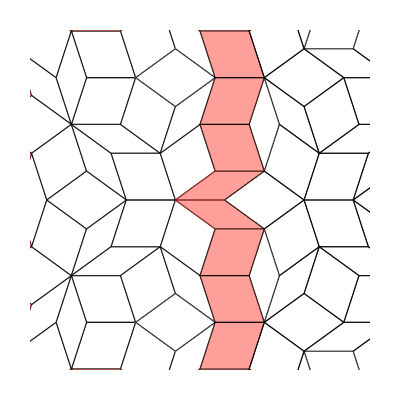

-Graphics-

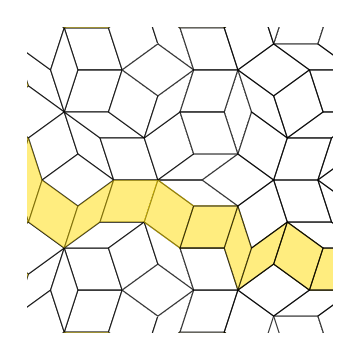

-Graphics-

```mathematica
Show[-Graphics-,-Graphics-]
```

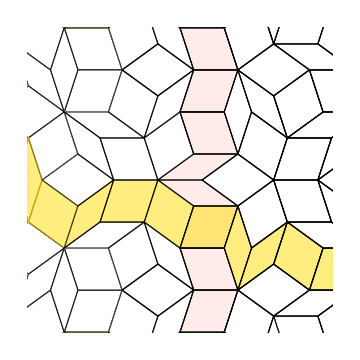

Ribbons.png

```mathematica
Graphics[List[List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],FaceForm[None],List[GrayLevel[1],Polygon[List[List[-0.7360679774997897,-0.05300056313598284],List[-0.7639320225002102,-0.1387572757128878],List[-0.6909830056250525,-0.08575671257690495],List[-0.663118960624632,0]]]],List[GrayLevel[1],Polygon[List[List[-0.7360679774997897,0.05300056313598284],List[-0.7639320225002102,0.1387572757128878],List[-0.6909830056250525,0.08575671257690495],List[-0.663118960624632,0]]]],List[GrayLevel[1],Polygon[List[List[-0.663118960624632,0],List[-0.7360679774997898,0.05300056313598284],List[-0.8090169943749475,0],List[-0.7360679774997897,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[-0.6008130618755784,-0.08575671257690495],List[-0.5729490168751578,-0.1715134251538099],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.6008130618755784,0.08575671257690495],List[-0.5729490168751578,0.1715134251538099],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0],List[-0.6008130618755783,-0.08575671257690495],List[-0.6909830056250525,-0.08575671257690495],List[-0.663118960624632,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0],List[-0.6008130618755783,0.08575671257690495],List[-0.6909830056250525,0.08575671257690495],List[-0.663118960624632,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0],List[-0.5,0.05300056313598284],List[-0.42705098312484224,0],List[-0.5,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,-0.17151342515380988],List[-0.6631189606246319,-0.17151342515380988],List[-0.6909830056250525,-0.08575671257690495],List[-0.6008130618755784,-0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0.17151342515380988],List[-0.6631189606246319,0.17151342515380988],List[-0.6909830056250525,0.08575671257690495],List[-0.6008130618755784,0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.5,-0.05300056313598284],List[-0.4721359549995794,-0.1387572757128878],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5,0.05300056313598284],List[-0.4721359549995794,0.1387572757128878],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5,-0.22451398828979272],List[-0.4721359549995794,-0.1387572757128878],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,-0.17151342515380988]]]],List[GrayLevel[1],Polygon[List[List[-0.5,-0.22451398828979272],List[-0.40983005625052576,-0.22451398828979274],List[-0.38196601125010515,-0.1387572757128878],List[-0.4721359549995794,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.5,0.22451398828979272],List[-0.4721359549995794,0.1387572757128878],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0.17151342515380988]]]],List[GrayLevel[1],Polygon[List[List[-0.5,0.22451398828979272],List[-0.40983005625052576,0.22451398828979274],List[-0.38196601125010515,0.1387572757128878],List[-0.4721359549995794,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.4721359549995794,-0.13875727571288776],List[-0.39918693812442163,-0.08575671257690493],List[-0.42705098312484224,0],List[-0.5,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[-0.4721359549995794,0.13875727571288776],List[-0.39918693812442163,0.08575671257690493],List[-0.42705098312484224,0],List[-0.5,0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[-0.4098300562505257,-0.22451398828979274],List[-0.33688103937536795,-0.27751455142577564],List[-0.42705098312484224,-0.2775145514257756],List[-0.5,-0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.4098300562505257,0.22451398828979274],List[-0.33688103937536795,0.27751455142577564],List[-0.42705098312484224,0.2775145514257756],List[-0.5,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.39918693812442163,-0.08575671257690494],List[-0.3090169943749474,-0.08575671257690497],List[-0.38196601125010515,-0.1387572757128878],List[-0.4721359549995794,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.39918693812442163,0.08575671257690494],List[-0.3090169943749474,0.08575671257690497],List[-0.38196601125010515,0.1387572757128878],List[-0.4721359549995794,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.33688103937536806,0],List[-0.30901699437494745,0.08575671257690493],List[-0.28115294937452684,0],List[-0.30901699437494745,-0.08575671257690493]]]],List[GrayLevel[1],Polygon[List[List[-0.33688103937536806,-0.2775145514257755],List[-0.3090169943749475,-0.19175783884887057],List[-0.38196601125010515,-0.1387572757128878],List[-0.4098300562505257,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[-0.33688103937536806,0.2775145514257755],List[-0.3090169943749475,0.19175783884887057],List[-0.38196601125010515,0.1387572757128878],List[-0.4098300562505257,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,-0.08575671257690493],List[-0.33688103937536806,1.3877787807814457*^-17],List[-0.42705098312484224,0],List[-0.39918693812442163,-0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.08575671257690493],List[-0.33688103937536806,-1.3877787807814457*^-17],List[-0.42705098312484224,0],List[-0.39918693812442163,0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,-0.1917578388488706],List[-0.23606797749978975,-0.1387572757128878],List[-0.26393202250021036,-0.22451398828979272],List[-0.33688103937536806,-0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.1917578388488706],List[-0.23606797749978975,0.1387572757128878],List[-0.26393202250021036,0.22451398828979272],List[-0.33688103937536806,0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,-0.3632712640026805],List[-0.39918693812442163,-0.36327126400268056],List[-0.42705098312484224,-0.2775145514257756],List[-0.33688103937536806,-0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,-0.3632712640026805],List[-0.23606797749978975,-0.3102707008666977],List[-0.26393202250021036,-0.22451398828979272],List[-0.33688103937536806,-0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,-0.3632712640026805],List[-0.2360679774997897,-0.41627182713866334],List[-0.16311896062463196,-0.3632712640026805],List[-0.23606797749978972,-0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.39918693812442163,0.36327126400268056],List[-0.42705098312484224,0.2775145514257756],List[-0.33688103937536806,0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.23606797749978975,0.3102707008666977],List[-0.26393202250021036,0.22451398828979272],List[-0.33688103937536806,0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.2360679774997897,0.41627182713866334],List[-0.16311896062463196,0.3632712640026805],List[-0.23606797749978972,0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,-0.13875727571288776],List[-0.30901699437494745,-0.19175783884887063],List[-0.38196601125010515,-0.1387572757128878],List[-0.30901699437494745,-0.08575671257690493]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,-0.13875727571288776],List[-0.20820393249936914,-0.05300056313598284],List[-0.28115294937452684,0],List[-0.30901699437494745,-0.08575671257690493]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,-0.13875727571288776],List[-0.14589803375031551,-0.13875727571288776],List[-0.1180339887498949,-0.22451398828979272],List[-0.20820393249936914,-0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.30901699437494745,0.19175783884887063],List[-0.38196601125010515,0.1387572757128878],List[-0.30901699437494745,0.08575671257690493]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.20820393249936914,0.05300056313598284],List[-0.28115294937452684,0],List[-0.30901699437494745,0.08575671257690493]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.14589803375031551,0.13875727571288776],List[-0.1180339887498949,0.22451398828979272],List[-0.20820393249936914,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978972,-0.31027070086669767],List[-0.1458980337503155,-0.31027070086669767],List[-0.1180339887498949,-0.22451398828979272],List[-0.20820393249936914,-0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978972,0.31027070086669767],List[-0.1458980337503155,0.31027070086669767],List[-0.1180339887498949,0.22451398828979272],List[-0.20820393249936914,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.2360679774997897,-0.41627182713866334],List[-0.20820393249936908,-0.5020285397155683],List[-0.11803398874989482,-0.5020285397155683],List[-0.14589803375031543,-0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.2360679774997897,0.41627182713866334],List[-0.20820393249936908,0.5020285397155683],List[-0.11803398874989482,0.5020285397155683],List[-0.14589803375031543,0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.20820393249936914,-0.05300056313598282],List[-0.13525491562421144,1.3877787807814457*^-17],List[-0.16311896062463205,-0.08575671257690493],List[-0.23606797749978975,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.20820393249936914,0.05300056313598282],List[-0.13525491562421144,-1.3877787807814457*^-17],List[-0.16311896062463205,0.08575671257690493],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.20820393249936914,-0.22451398828979272],List[-0.23606797749978975,-0.31027070086669767],List[-0.26393202250021036,-0.22451398828979272],List[-0.23606797749978975,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.20820393249936914,0.22451398828979272],List[-0.23606797749978975,0.31027070086669767],List[-0.26393202250021036,0.22451398828979272],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031551,-0.13875727571288776],List[-0.07294901687515781,-0.08575671257690493],List[-0.16311896062463205,-0.08575671257690493],List[-0.23606797749978975,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031551,0.13875727571288776],List[-0.07294901687515781,0.08575671257690493],List[-0.16311896062463205,0.08575671257690493],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031546,-0.31027070086669767],List[-0.0729490168751577,-0.3632712640026805],List[-0.16311896062463196,-0.3632712640026805],List[-0.23606797749978972,-0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031546,0.31027070086669767],List[-0.0729490168751577,0.3632712640026805],List[-0.16311896062463196,0.3632712640026805],List[-0.23606797749978972,0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031543,-0.41627182713866334],List[-0.0729490168751577,-0.3632712640026805],List[-0.16311896062463196,-0.3632712640026805],List[-0.2360679774997897,-0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031543,0.41627182713866334],List[-0.0729490168751577,0.3632712640026805],List[-0.16311896062463196,0.3632712640026805],List[-0.2360679774997897,0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.13525491562421146,0],List[-0.20820393249936917,0.05300056313598282],List[-0.28115294937452684,0],List[-0.20820393249936914,-0.05300056313598282]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515784,-0.08575671257690495],List[-0.04508497187473723,-0.1715134251538099],List[-0.1180339887498949,-0.22451398828979272],List[-0.14589803375031551,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515784,0.08575671257690495],List[-0.04508497187473723,0.1715134251538099],List[-0.1180339887498949,0.22451398828979272],List[-0.14589803375031551,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,-0.3632712640026805],List[-0.04508497187473716,-0.2775145514257755],List[-0.1180339887498949,-0.22451398828979272],List[-0.14589803375031546,-0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,-0.3632712640026805],List[-0.045084971874737104,-0.44902797657958543],List[-0.11803398874989482,-0.5020285397155683],List[-0.14589803375031543,-0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,-0.3632712640026805],List[0.017220926874316526,-0.3632712640026805],List[0.04508497187473717,-0.4490279765795855],List[-0.04508497187473707,-0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.04508497187473716,0.2775145514257755],List[-0.1180339887498949,0.22451398828979272],List[-0.14589803375031546,0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.045084971874737104,0.44902797657958543],List[-0.11803398874989482,0.5020285397155683],List[-0.14589803375031543,0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[0.017220926874316526,0.3632712640026805],List[0.04508497187473717,0.4490279765795855],List[-0.04508497187473707,0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515766,-0.5347846891564904],List[-0.1458980337503154,-0.5877852522924731],List[-0.11803398874989482,-0.5020285397155683],List[-0.04508497187473707,-0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515766,0.5347846891564904],List[-0.1458980337503154,0.5877852522924731],List[-0.11803398874989482,0.5020285397155683],List[-0.04508497187473707,0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[-0.07294901687515784,-0.08575671257690493],List[-0.16311896062463205,-0.08575671257690493],List[-0.13525491562421146,0]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[-0.07294901687515784,0.08575671257690493],List[-0.16311896062463205,0.08575671257690493],List[-0.13525491562421146,0]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[0.02786404500042053,-0.05300056313598281],List[-5.551115123125783*^-17,-0.13875727571288776],List[-0.07294901687515784,-0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[0.02786404500042053,0.05300056313598281],List[-5.551115123125783*^-17,0.13875727571288776],List[-0.07294901687515784,0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.04508497187473719,-0.17151342515380988],List[0.027864045000420598,-0.2245139882897927],List[-5.551115123125783*^-17,-0.13875727571288776],List[-0.07294901687515784,-0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.04508497187473719,0.17151342515380988],List[0.027864045000420598,0.2245139882897927],List[-5.551115123125783*^-17,0.13875727571288776],List[-0.07294901687515784,0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737145,-0.2775145514257755],List[0.02786404500042057,-0.2245139882897927],List[0.,-0.31027070086669767],List[-0.07294901687515772,-0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737145,0.2775145514257755],List[0.02786404500042057,0.2245139882897927],List[0.,0.31027070086669767],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.04508497187473707,-0.4490279765795855],List[0.027864045000420702,-0.5020285397155684],List[1.1102230246251565*^-16,-0.5877852522924732],List[-0.07294901687515766,-0.5347846891564904]]]],List[GrayLevel[1],Polygon[List[List[-0.04508497187473707,0.4490279765795855],List[0.027864045000420702,0.5020285397155684],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515766,0.5347846891564904]]]],List[GrayLevel[1],Polygon[List[List[0.017220926874316537,-0.3632712640026805],List[0.09016994374947425,-0.31027070086669767],List[0.,-0.31027070086669767],List[-0.07294901687515772,-0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.017220926874316537,0.3632712640026805],List[0.09016994374947425,0.31027070086669767],List[0.,0.31027070086669767],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.02786404500042051,-0.05300056313598284],List[0.11803398874989478,-0.05300056313598284],List[0.045084971874737007,0],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[0.02786404500042051,0.05300056313598284],List[0.11803398874989478,0.05300056313598284],List[0.045084971874737007,0],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[0.02786404500042053,-0.22451398828979274],List[-0.04508497187473719,-0.2775145514257756],List[-0.1180339887498949,-0.22451398828979272],List[-0.04508497187473719,-0.17151342515380988]]]],List[GrayLevel[1],Polygon[List[List[0.02786404500042053,0.22451398828979274],List[-0.04508497187473719,0.2775145514257756],List[-0.1180339887498949,0.22451398828979272],List[-0.04508497187473719,0.17151342515380988]]]],List[GrayLevel[1],Polygon[List[List[0.027864045000420678,-0.5020285397155684],List[0.11803398874989492,-0.5020285397155684],List[0.04508497187473717,-0.4490279765795855],List[-0.04508497187473707,-0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[0.027864045000420678,0.5020285397155684],List[0.11803398874989492,0.5020285397155684],List[0.04508497187473717,0.4490279765795855],List[-0.04508497187473707,0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[0.09016994374947417,-0.1387572757128878],List[0.1180339887498948,-0.22451398828979274],List[0.14589803375031538,-0.1387572757128878],List[0.11803398874989474,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.09016994374947417,0.1387572757128878],List[0.1180339887498948,0.22451398828979274],List[0.14589803375031538,0.1387572757128878],List[0.11803398874989474,0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.09016994374947422,-0.3102707008666977],List[0.11803398874989486,-0.3960274134436027],List[0.04508497187473717,-0.4490279765795855],List[0.017220926874316537,-0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.09016994374947422,0.3102707008666977],List[0.11803398874989486,0.3960274134436027],List[0.04508497187473717,0.4490279765795855],List[0.017220926874316537,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989474,-0.05300056313598284],List[0.09016994374947417,-0.13875727571288776],List[-5.551115123125783*^-17,-0.13875727571288776],List[0.02786404500042051,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989474,0.05300056313598284],List[0.09016994374947417,0.13875727571288776],List[-5.551115123125783*^-17,0.13875727571288776],List[0.02786404500042051,0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,-0.22451398828979274],List[0.09016994374947421,-0.13875727571288776],List[-5.551115123125783*^-17,-0.13875727571288776],List[0.02786404500042053,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,-0.22451398828979274],List[0.09016994374947426,-0.31027070086669767],List[0.,-0.31027070086669767],List[0.02786404500042053,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,-0.22451398828979274],List[0.1909830056250526,-0.2775145514257755],List[0.16311896062463202,-0.3632712640026805],List[0.09016994374947422,-0.3102707008666977]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,-0.22451398828979274],List[0.19098300562505255,-0.2775145514257755],List[0.2639320225002103,-0.22451398828979272],List[0.19098300562505255,-0.1715134251538099]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[0.09016994374947421,0.13875727571288776],List[-5.551115123125783*^-17,0.13875727571288776],List[0.02786404500042053,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[0.09016994374947426,0.31027070086669767],List[0.,0.31027070086669767],List[0.02786404500042053,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[0.1909830056250526,0.2775145514257755],List[0.16311896062463202,0.3632712640026805],List[0.09016994374947422,0.3102707008666977]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[0.19098300562505255,0.2775145514257755],List[0.2639320225002103,0.22451398828979272],List[0.19098300562505255,0.1715134251538099]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989489,-0.39602741344360265],List[0.1909830056250527,-0.44902797657958543],List[0.16311896062463202,-0.3632712640026805],List[0.09016994374947422,-0.3102707008666977]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989489,0.39602741344360265],List[0.1909830056250527,0.44902797657958543],List[0.16311896062463202,0.3632712640026805],List[0.09016994374947422,0.3102707008666977]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989494,-0.5020285397155684],List[0.09016994374947437,-0.5877852522924732],List[1.1102230246251565*^-16,-0.5877852522924732],List[0.027864045000420678,-0.5020285397155684]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989494,0.5020285397155684],List[0.09016994374947437,0.5877852522924732],List[1.1102230246251565*^-16,0.5877852522924732],List[0.027864045000420678,0.5020285397155684]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.11803398874989471,0.05300056313598284],List[0.045084971874737007,0],List[0.11803398874989474,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.21884705062547308,-0.08575671257690495],List[0.14589803375031538,-0.1387572757128878],List[0.11803398874989474,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.21884705062547308,0.08575671257690495],List[0.14589803375031538,0.1387572757128878],List[0.11803398874989474,0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.28115294937452673,1.3877787807814457*^-17],List[0.3090169943749474,-0.08575671257690494],List[0.2188470506254731,-0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.28115294937452673,-1.3877787807814457*^-17],List[0.3090169943749474,0.08575671257690494],List[0.2188470506254731,0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505255,-0.1715134251538099],List[0.21884705062547313,-0.08575671257690495],List[0.14589803375031538,-0.1387572757128878],List[0.11803398874989479,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505255,0.1715134251538099],List[0.21884705062547313,0.08575671257690495],List[0.14589803375031538,0.1387572757128878],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250526,-0.2775145514257756],List[0.2811529493745269,-0.2775145514257756],List[0.30901699437494756,-0.3632712640026805],List[0.21884705062547327,-0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250526,0.2775145514257756],List[0.2811529493745269,0.2775145514257756],List[0.30901699437494756,0.3632712640026805],List[0.21884705062547327,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,-0.4490279765795855],List[0.11803398874989497,-0.5020285397155684],List[0.04508497187473717,-0.4490279765795855],List[0.11803398874989489,-0.39602741344360265]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,-0.4490279765795855],List[0.28115294937452695,-0.4490279765795855],List[0.30901699437494756,-0.3632712640026805],List[0.21884705062547327,-0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.11803398874989497,0.5020285397155684],List[0.04508497187473717,0.4490279765795855],List[0.11803398874989489,0.39602741344360265]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.28115294937452695,0.4490279765795855],List[0.30901699437494756,0.3632712640026805],List[0.21884705062547327,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.2188470506254731,-0.08575671257690495],List[0.29179606750063086,-0.13875727571288776],List[0.2639320225002103,-0.22451398828979272],List[0.19098300562505255,-0.1715134251538099]]]],List[GrayLevel[1],Polygon[List[List[0.2188470506254731,0.08575671257690495],List[0.29179606750063086,0.13875727571288776],List[0.2639320225002103,0.22451398828979272],List[0.19098300562505255,0.1715134251538099]]]],List[GrayLevel[1],Polygon[List[List[0.21884705062547327,-0.3632712640026805],List[0.1909830056250527,-0.44902797657958543],List[0.16311896062463202,-0.3632712640026805],List[0.1909830056250526,-0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.21884705062547327,0.3632712640026805],List[0.1909830056250527,0.44902797657958543],List[0.16311896062463202,0.3632712640026805],List[0.1909830056250526,0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.28115294937452673,0],List[0.35410196624968443,0.05300056313598283],List[0.42705098312484224,0],List[0.35410196624968454,-0.05300056313598283]]]],List[GrayLevel[1],Polygon[List[List[0.2811529493745269,-0.2775145514257756],List[0.3541019662496846,-0.22451398828979272],List[0.2639320225002103,-0.22451398828979272],List[0.1909830056250526,-0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.2811529493745269,0.2775145514257756],List[0.3541019662496846,0.22451398828979272],List[0.2639320225002103,0.22451398828979272],List[0.1909830056250526,0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.2917960675006309,-0.1387572757128878],List[0.3819660112501052,-0.13875727571288776],List[0.3090169943749474,-0.08575671257690494],List[0.2188470506254731,-0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[0.2917960675006309,0.1387572757128878],List[0.3819660112501052,0.13875727571288776],List[0.3090169943749474,0.08575671257690494],List[0.2188470506254731,0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[0.35410196624968454,-0.05300056313598283],List[0.3819660112501052,-0.13875727571288776],List[0.3090169943749474,-0.08575671257690494],List[0.28115294937452673,0]]]],List[GrayLevel[1],Polygon[List[List[0.35410196624968454,0.05300056313598283],List[0.3819660112501052,0.13875727571288776],List[0.3090169943749474,0.08575671257690494],List[0.28115294937452673,0]]]],List[GrayLevel[1],Polygon[List[List[0.35410196624968465,-0.22451398828979274],List[0.3819660112501053,-0.31027070086669767],List[0.30901699437494756,-0.3632712640026805],List[0.2811529493745269,-0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.35410196624968465,0.22451398828979274],List[0.3819660112501053,0.31027070086669767],List[0.30901699437494756,0.3632712640026805],List[0.2811529493745269,0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.3541019662496846,-0.22451398828979272],List[0.2639320225002103,-0.22451398828979272],List[0.2917960675006309,-0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.4549150281252629,-0.08575671257690495],List[0.42705098312484224,0],List[0.35410196624968454,-0.05300056313598283]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.45491502812526297,-0.19175783884887057],List[0.4270509831248424,-0.2775145514257755],List[0.35410196624968465,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.3541019662496846,0.22451398828979272],List[0.2639320225002103,0.22451398828979272],List[0.2917960675006309,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.4549150281252629,0.08575671257690495],List[0.42705098312484224,0],List[0.35410196624968454,0.05300056313598283]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.45491502812526297,0.19175783884887057],List[0.4270509831248424,0.2775145514257755],List[0.35410196624968465,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.38196601125010526,-0.31027070086669767],List[0.454915028125263,-0.36327126400268045],List[0.4270509831248424,-0.2775145514257755],List[0.35410196624968465,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.38196601125010526,0.31027070086669767],List[0.454915028125263,0.36327126400268045],List[0.4270509831248424,0.2775145514257755],List[0.35410196624968465,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.4549150281252629,-0.08575671257690494],List[0.5450849718747373,-0.08575671257690494],List[0.4721359549995795,-0.1387572757128878],List[0.3819660112501052,-0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.4549150281252629,0.08575671257690494],List[0.5450849718747373,0.08575671257690494],List[0.4721359549995795,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.45491502812526297,-0.1917578388488706],List[0.5450849718747373,-0.1917578388488706],List[0.4721359549995795,-0.1387572757128878],List[0.3819660112501052,-0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.45491502812526297,0.1917578388488706],List[0.5450849718747373,0.1917578388488706],List[0.4721359549995795,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.5172209268743165,0],List[0.5450849718747371,0.08575671257690494],List[0.5729490168751578,0],List[0.5450849718747371,-0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.5450849718747371,-0.08575671257690494],List[0.5172209268743164,0.],List[0.42705098312484224,0],List[0.4549150281252629,-0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.5450849718747371,0.08575671257690494],List[0.5172209268743164,0.],List[0.42705098312484224,0],List[0.4549150281252629,0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.5450849718747373,-0.1917578388488706],List[0.5172209268743166,-0.2775145514257755],List[0.4270509831248424,-0.2775145514257755],List[0.45491502812526297,-0.1917578388488706]]]],List[GrayLevel[1],Polygon[List[List[0.5450849718747373,0.1917578388488706],List[0.5172209268743166,0.2775145514257755],List[0.4270509831248424,0.2775145514257755],List[0.45491502812526297,0.1917578388488706]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,-0.1387572757128878],List[0.5450849718747373,-0.19175783884887065],List[0.4721359549995795,-0.1387572757128878],List[0.5450849718747371,-0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,-0.1387572757128878],List[0.6458980337503155,-0.05300056313598285],List[0.5729490168751578,0],List[0.5450849718747371,-0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.5450849718747373,0.19175783884887065],List[0.4721359549995795,0.1387572757128878],List[0.5450849718747371,0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.6458980337503155,0.05300056313598285],List[0.5729490168751578,0],List[0.5450849718747371,0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.6458980337503155,-0.05300056313598283],List[0.7188470506254733,1.3877787807814457*^-17],List[0.6909830056250527,-0.08575671257690494],List[0.6180339887498949,-0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.6458980337503155,0.05300056313598283],List[0.7188470506254733,-1.3877787807814457*^-17],List[0.6909830056250527,0.08575671257690494],List[0.6180339887498949,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.7188470506254732,0],List[0.6458980337503154,0.05300056313598283],List[0.5729490168751578,0],List[0.6458980337503155,-0.05300056313598283]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[0.781152949374527,-0.08575671257690494],List[0.6909830056250527,-0.08575671257690494],List[0.7188470506254732,0]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[0.781152949374527,0.08575671257690494],List[0.6909830056250527,0.08575671257690494],List[0.7188470506254732,0]]]]],List[Opacity[0.5],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.7360679774997897,-0.05300056313598284],List[-0.7639320225002102,-0.1387572757128878],List[-0.6909830056250525,-0.08575671257690495],List[-0.663118960624632,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.7360679774997897,0.05300056313598284],List[-0.7639320225002102,0.1387572757128878],List[-0.6909830056250525,0.08575671257690495],List[-0.663118960624632,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.663118960624632,0],List[-0.7360679774997898,0.05300056313598284],List[-0.8090169943749475,0],List[-0.7360679774997897,-0.05300056313598284]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.6008130618755784,-0.08575671257690495],List[-0.5729490168751578,-0.1715134251538099],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.6008130618755784,0.08575671257690495],List[-0.5729490168751578,0.1715134251538099],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5729490168751578,0],List[-0.6008130618755783,-0.08575671257690495],List[-0.6909830056250525,-0.08575671257690495],List[-0.663118960624632,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5729490168751578,0],List[-0.6008130618755783,0.08575671257690495],List[-0.6909830056250525,0.08575671257690495],List[-0.663118960624632,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5729490168751578,0],List[-0.5,0.05300056313598284],List[-0.42705098312484224,0],List[-0.5,-0.05300056313598284]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5729490168751578,-0.17151342515380988],List[-0.6631189606246319,-0.17151342515380988],List[-0.6909830056250525,-0.08575671257690495],List[-0.6008130618755784,-0.08575671257690495]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5729490168751578,0.17151342515380988],List[-0.6631189606246319,0.17151342515380988],List[-0.6909830056250525,0.08575671257690495],List[-0.6008130618755784,0.08575671257690495]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5,-0.05300056313598284],List[-0.4721359549995794,-0.1387572757128878],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5,0.05300056313598284],List[-0.4721359549995794,0.1387572757128878],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5,-0.22451398828979272],List[-0.4721359549995794,-0.1387572757128878],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,-0.17151342515380988]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5,-0.22451398828979272],List[-0.40983005625052576,-0.22451398828979274],List[-0.38196601125010515,-0.1387572757128878],List[-0.4721359549995794,-0.13875727571288776]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5,0.22451398828979272],List[-0.4721359549995794,0.1387572757128878],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0.17151342515380988]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.5,0.22451398828979272],List[-0.40983005625052576,0.22451398828979274],List[-0.38196601125010515,0.1387572757128878],List[-0.4721359549995794,0.13875727571288776]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.4721359549995794,-0.13875727571288776],List[-0.39918693812442163,-0.08575671257690493],List[-0.42705098312484224,0],List[-0.5,-0.05300056313598284]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.4721359549995794,0.13875727571288776],List[-0.39918693812442163,0.08575671257690493],List[-0.42705098312484224,0],List[-0.5,0.05300056313598284]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.4098300562505257,-0.22451398828979274],List[-0.33688103937536795,-0.27751455142577564],List[-0.42705098312484224,-0.2775145514257756],List[-0.5,-0.22451398828979272]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.4098300562505257,0.22451398828979274],List[-0.33688103937536795,0.27751455142577564],List[-0.42705098312484224,0.2775145514257756],List[-0.5,0.22451398828979272]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.39918693812442163,-0.08575671257690494],List[-0.3090169943749474,-0.08575671257690497],List[-0.38196601125010515,-0.1387572757128878],List[-0.4721359549995794,-0.13875727571288776]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.39918693812442163,0.08575671257690494],List[-0.3090169943749474,0.08575671257690497],List[-0.38196601125010515,0.1387572757128878],List[-0.4721359549995794,0.13875727571288776]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.33688103937536806,-0.2775145514257755],List[-0.3090169943749475,-0.19175783884887057],List[-0.38196601125010515,-0.1387572757128878],List[-0.4098300562505257,-0.22451398828979274]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.33688103937536806,0.2775145514257755],List[-0.3090169943749475,0.19175783884887057],List[-0.38196601125010515,0.1387572757128878],List[-0.4098300562505257,0.22451398828979274]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.30901699437494745,-0.08575671257690493],List[-0.33688103937536806,1.3877787807814457*^-17],List[-0.42705098312484224,0],List[-0.39918693812442163,-0.08575671257690494]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.30901699437494745,0.08575671257690493],List[-0.33688103937536806,-1.3877787807814457*^-17],List[-0.42705098312484224,0],List[-0.39918693812442163,0.08575671257690494]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.30901699437494745,-0.3632712640026805],List[-0.39918693812442163,-0.36327126400268056],List[-0.42705098312484224,-0.2775145514257756],List[-0.33688103937536806,-0.2775145514257755]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.30901699437494745,-0.3632712640026805],List[-0.2360679774997897,-0.41627182713866334],List[-0.16311896062463196,-0.3632712640026805],List[-0.23606797749978972,-0.31027070086669767]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.39918693812442163,0.36327126400268056],List[-0.42705098312484224,0.2775145514257756],List[-0.33688103937536806,0.2775145514257755]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.2360679774997897,0.41627182713866334],List[-0.16311896062463196,0.3632712640026805],List[-0.23606797749978972,0.31027070086669767]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.2360679774997897,-0.41627182713866334],List[-0.20820393249936908,-0.5020285397155683],List[-0.11803398874989482,-0.5020285397155683],List[-0.14589803375031543,-0.41627182713866334]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.2360679774997897,0.41627182713866334],List[-0.20820393249936908,0.5020285397155683],List[-0.11803398874989482,0.5020285397155683],List[-0.14589803375031543,0.41627182713866334]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.14589803375031546,-0.31027070086669767],List[-0.0729490168751577,-0.3632712640026805],List[-0.16311896062463196,-0.3632712640026805],List[-0.23606797749978972,-0.31027070086669767]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.14589803375031546,0.31027070086669767],List[-0.0729490168751577,0.3632712640026805],List[-0.16311896062463196,0.3632712640026805],List[-0.23606797749978972,0.31027070086669767]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.14589803375031543,-0.41627182713866334],List[-0.0729490168751577,-0.3632712640026805],List[-0.16311896062463196,-0.3632712640026805],List[-0.2360679774997897,-0.41627182713866334]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.14589803375031543,0.41627182713866334],List[-0.0729490168751577,0.3632712640026805],List[-0.16311896062463196,0.3632712640026805],List[-0.2360679774997897,0.41627182713866334]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.07294901687515772,-0.3632712640026805],List[-0.045084971874737104,-0.44902797657958543],List[-0.11803398874989482,-0.5020285397155683],List[-0.14589803375031543,-0.41627182713866334]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.07294901687515772,-0.3632712640026805],List[0.017220926874316526,-0.3632712640026805],List[0.04508497187473717,-0.4490279765795855],List[-0.04508497187473707,-0.4490279765795855]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.045084971874737104,0.44902797657958543],List[-0.11803398874989482,0.5020285397155683],List[-0.14589803375031543,0.41627182713866334]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[0.017220926874316526,0.3632712640026805],List[0.04508497187473717,0.4490279765795855],List[-0.04508497187473707,0.4490279765795855]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.07294901687515766,-0.5347846891564904],List[-0.1458980337503154,-0.5877852522924731],List[-0.11803398874989482,-0.5020285397155683],List[-0.04508497187473707,-0.4490279765795855]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.07294901687515766,0.5347846891564904],List[-0.1458980337503154,0.5877852522924731],List[-0.11803398874989482,0.5020285397155683],List[-0.04508497187473707,0.4490279765795855]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.04508497187473707,-0.4490279765795855],List[0.027864045000420702,-0.5020285397155684],List[1.1102230246251565*^-16,-0.5877852522924732],List[-0.07294901687515766,-0.5347846891564904]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[-0.04508497187473707,0.4490279765795855],List[0.027864045000420702,0.5020285397155684],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515766,0.5347846891564904]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.017220926874316537,-0.3632712640026805],List[0.09016994374947425,-0.31027070086669767],List[0.,-0.31027070086669767],List[-0.07294901687515772,-0.3632712640026805]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.017220926874316537,0.3632712640026805],List[0.09016994374947425,0.31027070086669767],List[0.,0.31027070086669767],List[-0.07294901687515772,0.3632712640026805]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.02786404500042051,-0.05300056313598284],List[0.11803398874989478,-0.05300056313598284],List[0.045084971874737007,0],List[-0.045084971874737256,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.02786404500042051,0.05300056313598284],List[0.11803398874989478,0.05300056313598284],List[0.045084971874737007,0],List[-0.045084971874737256,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.027864045000420678,-0.5020285397155684],List[0.11803398874989492,-0.5020285397155684],List[0.04508497187473717,-0.4490279765795855],List[-0.04508497187473707,-0.4490279765795855]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.027864045000420678,0.5020285397155684],List[0.11803398874989492,0.5020285397155684],List[0.04508497187473717,0.4490279765795855],List[-0.04508497187473707,0.4490279765795855]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.09016994374947422,-0.3102707008666977],List[0.11803398874989486,-0.3960274134436027],List[0.04508497187473717,-0.4490279765795855],List[0.017220926874316537,-0.3632712640026805]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.09016994374947422,0.3102707008666977],List[0.11803398874989486,0.3960274134436027],List[0.04508497187473717,0.4490279765795855],List[0.017220926874316537,0.3632712640026805]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.11803398874989474,-0.05300056313598284],List[0.09016994374947417,-0.13875727571288776],List[-5.551115123125783*^-17,-0.13875727571288776],List[0.02786404500042051,-0.05300056313598284]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.11803398874989474,0.05300056313598284],List[0.09016994374947417,0.13875727571288776],List[-5.551115123125783*^-17,0.13875727571288776],List[0.02786404500042051,0.05300056313598284]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.11803398874989479,-0.22451398828979274],List[0.09016994374947421,-0.13875727571288776],List[-5.551115123125783*^-17,-0.13875727571288776],List[0.02786404500042053,-0.22451398828979274]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.11803398874989479,-0.22451398828979274],List[0.09016994374947426,-0.31027070086669767],List[0.,-0.31027070086669767],List[0.02786404500042053,-0.22451398828979274]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[0.09016994374947421,0.13875727571288776],List[-5.551115123125783*^-17,0.13875727571288776],List[0.02786404500042053,0.22451398828979274]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[0.09016994374947426,0.31027070086669767],List[0.,0.31027070086669767],List[0.02786404500042053,0.22451398828979274]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.11803398874989489,-0.39602741344360265],List[0.1909830056250527,-0.44902797657958543],List[0.16311896062463202,-0.3632712640026805],List[0.09016994374947422,-0.3102707008666977]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.11803398874989489,0.39602741344360265],List[0.1909830056250527,0.44902797657958543],List[0.16311896062463202,0.3632712640026805],List[0.09016994374947422,0.3102707008666977]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.11803398874989494,-0.5020285397155684],List[0.09016994374947437,-0.5877852522924732],List[1.1102230246251565*^-16,-0.5877852522924732],List[0.027864045000420678,-0.5020285397155684]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.11803398874989494,0.5020285397155684],List[0.09016994374947437,0.5877852522924732],List[1.1102230246251565*^-16,0.5877852522924732],List[0.027864045000420678,0.5020285397155684]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.1909830056250527,-0.4490279765795855],List[0.11803398874989497,-0.5020285397155684],List[0.04508497187473717,-0.4490279765795855],List[0.11803398874989489,-0.39602741344360265]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.1909830056250527,-0.4490279765795855],List[0.28115294937452695,-0.4490279765795855],List[0.30901699437494756,-0.3632712640026805],List[0.21884705062547327,-0.3632712640026805]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.11803398874989497,0.5020285397155684],List[0.04508497187473717,0.4490279765795855],List[0.11803398874989489,0.39602741344360265]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.28115294937452695,0.4490279765795855],List[0.30901699437494756,0.3632712640026805],List[0.21884705062547327,0.3632712640026805]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.4549150281252629,-0.08575671257690495],List[0.42705098312484224,0],List[0.35410196624968454,-0.05300056313598283]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.45491502812526297,-0.19175783884887057],List[0.4270509831248424,-0.2775145514257755],List[0.35410196624968465,-0.22451398828979274]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.4549150281252629,0.08575671257690495],List[0.42705098312484224,0],List[0.35410196624968454,0.05300056313598283]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.45491502812526297,0.19175783884887057],List[0.4270509831248424,0.2775145514257755],List[0.35410196624968465,0.22451398828979274]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.38196601125010526,-0.31027070086669767],List[0.454915028125263,-0.36327126400268045],List[0.4270509831248424,-0.2775145514257755],List[0.35410196624968465,-0.22451398828979274]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.38196601125010526,0.31027070086669767],List[0.454915028125263,0.36327126400268045],List[0.4270509831248424,0.2775145514257755],List[0.35410196624968465,0.22451398828979274]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.4549150281252629,-0.08575671257690494],List[0.5450849718747373,-0.08575671257690494],List[0.4721359549995795,-0.1387572757128878],List[0.3819660112501052,-0.1387572757128878]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.4549150281252629,0.08575671257690494],List[0.5450849718747373,0.08575671257690494],List[0.4721359549995795,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.45491502812526297,-0.1917578388488706],List[0.5450849718747373,-0.1917578388488706],List[0.4721359549995795,-0.1387572757128878],List[0.3819660112501052,-0.1387572757128878]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.45491502812526297,0.1917578388488706],List[0.5450849718747373,0.1917578388488706],List[0.4721359549995795,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.5172209268743165,0],List[0.5450849718747371,0.08575671257690494],List[0.5729490168751578,0],List[0.5450849718747371,-0.08575671257690494]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.5450849718747371,-0.08575671257690494],List[0.5172209268743164,0.],List[0.42705098312484224,0],List[0.4549150281252629,-0.08575671257690494]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.5450849718747371,0.08575671257690494],List[0.5172209268743164,0.],List[0.42705098312484224,0],List[0.4549150281252629,0.08575671257690494]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.5450849718747373,-0.1917578388488706],List[0.5172209268743166,-0.2775145514257755],List[0.4270509831248424,-0.2775145514257755],List[0.45491502812526297,-0.1917578388488706]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.5450849718747373,0.1917578388488706],List[0.5172209268743166,0.2775145514257755],List[0.4270509831248424,0.2775145514257755],List[0.45491502812526297,0.1917578388488706]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.6180339887498949,-0.1387572757128878],List[0.5450849718747373,-0.19175783884887065],List[0.4721359549995795,-0.1387572757128878],List[0.5450849718747371,-0.08575671257690494]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.6180339887498949,-0.1387572757128878],List[0.6458980337503155,-0.05300056313598285],List[0.5729490168751578,0],List[0.5450849718747371,-0.08575671257690494]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.5450849718747373,0.19175783884887065],List[0.4721359549995795,0.1387572757128878],List[0.5450849718747371,0.08575671257690494]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.6458980337503155,0.05300056313598285],List[0.5729490168751578,0],List[0.5450849718747371,0.08575671257690494]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.6458980337503155,-0.05300056313598283],List[0.7188470506254733,1.3877787807814457*^-17],List[0.6909830056250527,-0.08575671257690494],List[0.6180339887498949,-0.1387572757128878]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.6458980337503155,0.05300056313598283],List[0.7188470506254733,-1.3877787807814457*^-17],List[0.6909830056250527,0.08575671257690494],List[0.6180339887498949,0.1387572757128878]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.7188470506254732,0],List[0.6458980337503154,0.05300056313598283],List[0.5729490168751578,0],List[0.6458980337503155,-0.05300056313598283]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.8090169943749475,0],List[0.781152949374527,-0.08575671257690494],List[0.6909830056250527,-0.08575671257690494],List[0.7188470506254732,0]]]],List[RGBColor[1.,0.2549019607843137,0.21176470588235294],Polygon[List[List[0.8090169943749475,0],List[0.781152949374527,0.08575671257690494],List[0.6909830056250527,0.08575671257690494],List[0.7188470506254732,0]]]]]],List[List[Opacity[0.8],EdgeForm[GrayLevel[0]],FaceForm[None],List[GrayLevel[1],Polygon[List[List[-0.7360679774997897,-0.05300056313598284],List[-0.7639320225002102,-0.1387572757128878],List[-0.6909830056250525,-0.08575671257690495],List[-0.663118960624632,0]]]],List[GrayLevel[1],Polygon[List[List[-0.7360679774997897,0.05300056313598284],List[-0.7639320225002102,0.1387572757128878],List[-0.6909830056250525,0.08575671257690495],List[-0.663118960624632,0]]]],List[GrayLevel[1],Polygon[List[List[-0.663118960624632,0],List[-0.7360679774997898,0.05300056313598284],List[-0.8090169943749475,0],List[-0.7360679774997897,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[-0.6008130618755784,-0.08575671257690495],List[-0.5729490168751578,-0.1715134251538099],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.6008130618755784,0.08575671257690495],List[-0.5729490168751578,0.1715134251538099],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0],List[-0.6008130618755783,-0.08575671257690495],List[-0.6909830056250525,-0.08575671257690495],List[-0.663118960624632,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0],List[-0.6008130618755783,0.08575671257690495],List[-0.6909830056250525,0.08575671257690495],List[-0.663118960624632,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0],List[-0.5,0.05300056313598284],List[-0.42705098312484224,0],List[-0.5,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,-0.17151342515380988],List[-0.6631189606246319,-0.17151342515380988],List[-0.6909830056250525,-0.08575671257690495],List[-0.6008130618755784,-0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.5729490168751578,0.17151342515380988],List[-0.6631189606246319,0.17151342515380988],List[-0.6909830056250525,0.08575671257690495],List[-0.6008130618755784,0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.5,-0.05300056313598284],List[-0.4721359549995794,-0.1387572757128878],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5,0.05300056313598284],List[-0.4721359549995794,0.1387572757128878],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0]]]],List[GrayLevel[1],Polygon[List[List[-0.5,-0.22451398828979272],List[-0.4721359549995794,-0.1387572757128878],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,-0.17151342515380988]]]],List[GrayLevel[1],Polygon[List[List[-0.5,-0.22451398828979272],List[-0.40983005625052576,-0.22451398828979274],List[-0.38196601125010515,-0.1387572757128878],List[-0.4721359549995794,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.5,0.22451398828979272],List[-0.4721359549995794,0.1387572757128878],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0.17151342515380988]]]],List[GrayLevel[1],Polygon[List[List[-0.5,0.22451398828979272],List[-0.40983005625052576,0.22451398828979274],List[-0.38196601125010515,0.1387572757128878],List[-0.4721359549995794,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.4721359549995794,-0.13875727571288776],List[-0.39918693812442163,-0.08575671257690493],List[-0.42705098312484224,0],List[-0.5,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[-0.4721359549995794,0.13875727571288776],List[-0.39918693812442163,0.08575671257690493],List[-0.42705098312484224,0],List[-0.5,0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[-0.4098300562505257,-0.22451398828979274],List[-0.33688103937536795,-0.27751455142577564],List[-0.42705098312484224,-0.2775145514257756],List[-0.5,-0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.4098300562505257,0.22451398828979274],List[-0.33688103937536795,0.27751455142577564],List[-0.42705098312484224,0.2775145514257756],List[-0.5,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.39918693812442163,-0.08575671257690494],List[-0.3090169943749474,-0.08575671257690497],List[-0.38196601125010515,-0.1387572757128878],List[-0.4721359549995794,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.39918693812442163,0.08575671257690494],List[-0.3090169943749474,0.08575671257690497],List[-0.38196601125010515,0.1387572757128878],List[-0.4721359549995794,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.33688103937536806,0],List[-0.30901699437494745,0.08575671257690493],List[-0.28115294937452684,0],List[-0.30901699437494745,-0.08575671257690493]]]],List[GrayLevel[1],Polygon[List[List[-0.33688103937536806,-0.2775145514257755],List[-0.3090169943749475,-0.19175783884887057],List[-0.38196601125010515,-0.1387572757128878],List[-0.4098300562505257,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[-0.33688103937536806,0.2775145514257755],List[-0.3090169943749475,0.19175783884887057],List[-0.38196601125010515,0.1387572757128878],List[-0.4098300562505257,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,-0.08575671257690493],List[-0.33688103937536806,1.3877787807814457*^-17],List[-0.42705098312484224,0],List[-0.39918693812442163,-0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.08575671257690493],List[-0.33688103937536806,-1.3877787807814457*^-17],List[-0.42705098312484224,0],List[-0.39918693812442163,0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,-0.1917578388488706],List[-0.23606797749978975,-0.1387572757128878],List[-0.26393202250021036,-0.22451398828979272],List[-0.33688103937536806,-0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.1917578388488706],List[-0.23606797749978975,0.1387572757128878],List[-0.26393202250021036,0.22451398828979272],List[-0.33688103937536806,0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,-0.3632712640026805],List[-0.39918693812442163,-0.36327126400268056],List[-0.42705098312484224,-0.2775145514257756],List[-0.33688103937536806,-0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,-0.3632712640026805],List[-0.23606797749978975,-0.3102707008666977],List[-0.26393202250021036,-0.22451398828979272],List[-0.33688103937536806,-0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,-0.3632712640026805],List[-0.2360679774997897,-0.41627182713866334],List[-0.16311896062463196,-0.3632712640026805],List[-0.23606797749978972,-0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.39918693812442163,0.36327126400268056],List[-0.42705098312484224,0.2775145514257756],List[-0.33688103937536806,0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.23606797749978975,0.3102707008666977],List[-0.26393202250021036,0.22451398828979272],List[-0.33688103937536806,0.2775145514257755]]]],List[GrayLevel[1],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.2360679774997897,0.41627182713866334],List[-0.16311896062463196,0.3632712640026805],List[-0.23606797749978972,0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,-0.13875727571288776],List[-0.30901699437494745,-0.19175783884887063],List[-0.38196601125010515,-0.1387572757128878],List[-0.30901699437494745,-0.08575671257690493]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,-0.13875727571288776],List[-0.20820393249936914,-0.05300056313598284],List[-0.28115294937452684,0],List[-0.30901699437494745,-0.08575671257690493]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,-0.13875727571288776],List[-0.14589803375031551,-0.13875727571288776],List[-0.1180339887498949,-0.22451398828979272],List[-0.20820393249936914,-0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.30901699437494745,0.19175783884887063],List[-0.38196601125010515,0.1387572757128878],List[-0.30901699437494745,0.08575671257690493]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.20820393249936914,0.05300056313598284],List[-0.28115294937452684,0],List[-0.30901699437494745,0.08575671257690493]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978975,0.13875727571288776],List[-0.14589803375031551,0.13875727571288776],List[-0.1180339887498949,0.22451398828979272],List[-0.20820393249936914,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978972,-0.31027070086669767],List[-0.1458980337503155,-0.31027070086669767],List[-0.1180339887498949,-0.22451398828979272],List[-0.20820393249936914,-0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.23606797749978972,0.31027070086669767],List[-0.1458980337503155,0.31027070086669767],List[-0.1180339887498949,0.22451398828979272],List[-0.20820393249936914,0.22451398828979272]]]],List[GrayLevel[1],Polygon[List[List[-0.2360679774997897,-0.41627182713866334],List[-0.20820393249936908,-0.5020285397155683],List[-0.11803398874989482,-0.5020285397155683],List[-0.14589803375031543,-0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.2360679774997897,0.41627182713866334],List[-0.20820393249936908,0.5020285397155683],List[-0.11803398874989482,0.5020285397155683],List[-0.14589803375031543,0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.20820393249936914,-0.05300056313598282],List[-0.13525491562421144,1.3877787807814457*^-17],List[-0.16311896062463205,-0.08575671257690493],List[-0.23606797749978975,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.20820393249936914,0.05300056313598282],List[-0.13525491562421144,-1.3877787807814457*^-17],List[-0.16311896062463205,0.08575671257690493],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.20820393249936914,-0.22451398828979272],List[-0.23606797749978975,-0.31027070086669767],List[-0.26393202250021036,-0.22451398828979272],List[-0.23606797749978975,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.20820393249936914,0.22451398828979272],List[-0.23606797749978975,0.31027070086669767],List[-0.26393202250021036,0.22451398828979272],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031551,-0.13875727571288776],List[-0.07294901687515781,-0.08575671257690493],List[-0.16311896062463205,-0.08575671257690493],List[-0.23606797749978975,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031551,0.13875727571288776],List[-0.07294901687515781,0.08575671257690493],List[-0.16311896062463205,0.08575671257690493],List[-0.23606797749978975,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031546,-0.31027070086669767],List[-0.0729490168751577,-0.3632712640026805],List[-0.16311896062463196,-0.3632712640026805],List[-0.23606797749978972,-0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031546,0.31027070086669767],List[-0.0729490168751577,0.3632712640026805],List[-0.16311896062463196,0.3632712640026805],List[-0.23606797749978972,0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031543,-0.41627182713866334],List[-0.0729490168751577,-0.3632712640026805],List[-0.16311896062463196,-0.3632712640026805],List[-0.2360679774997897,-0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.14589803375031543,0.41627182713866334],List[-0.0729490168751577,0.3632712640026805],List[-0.16311896062463196,0.3632712640026805],List[-0.2360679774997897,0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.13525491562421146,0],List[-0.20820393249936917,0.05300056313598282],List[-0.28115294937452684,0],List[-0.20820393249936914,-0.05300056313598282]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515784,-0.08575671257690495],List[-0.04508497187473723,-0.1715134251538099],List[-0.1180339887498949,-0.22451398828979272],List[-0.14589803375031551,-0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515784,0.08575671257690495],List[-0.04508497187473723,0.1715134251538099],List[-0.1180339887498949,0.22451398828979272],List[-0.14589803375031551,0.13875727571288776]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,-0.3632712640026805],List[-0.04508497187473716,-0.2775145514257755],List[-0.1180339887498949,-0.22451398828979272],List[-0.14589803375031546,-0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,-0.3632712640026805],List[-0.045084971874737104,-0.44902797657958543],List[-0.11803398874989482,-0.5020285397155683],List[-0.14589803375031543,-0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,-0.3632712640026805],List[0.017220926874316526,-0.3632712640026805],List[0.04508497187473717,-0.4490279765795855],List[-0.04508497187473707,-0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.04508497187473716,0.2775145514257755],List[-0.1180339887498949,0.22451398828979272],List[-0.14589803375031546,0.31027070086669767]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.045084971874737104,0.44902797657958543],List[-0.11803398874989482,0.5020285397155683],List[-0.14589803375031543,0.41627182713866334]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[0.017220926874316526,0.3632712640026805],List[0.04508497187473717,0.4490279765795855],List[-0.04508497187473707,0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515766,-0.5347846891564904],List[-0.1458980337503154,-0.5877852522924731],List[-0.11803398874989482,-0.5020285397155683],List[-0.04508497187473707,-0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[-0.07294901687515766,0.5347846891564904],List[-0.1458980337503154,0.5877852522924731],List[-0.11803398874989482,0.5020285397155683],List[-0.04508497187473707,0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[-0.07294901687515784,-0.08575671257690493],List[-0.16311896062463205,-0.08575671257690493],List[-0.13525491562421146,0]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[-0.07294901687515784,0.08575671257690493],List[-0.16311896062463205,0.08575671257690493],List[-0.13525491562421146,0]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[0.02786404500042053,-0.05300056313598281],List[-5.551115123125783*^-17,-0.13875727571288776],List[-0.07294901687515784,-0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737256,0],List[0.02786404500042053,0.05300056313598281],List[-5.551115123125783*^-17,0.13875727571288776],List[-0.07294901687515784,0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.04508497187473719,-0.17151342515380988],List[0.027864045000420598,-0.2245139882897927],List[-5.551115123125783*^-17,-0.13875727571288776],List[-0.07294901687515784,-0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.04508497187473719,0.17151342515380988],List[0.027864045000420598,0.2245139882897927],List[-5.551115123125783*^-17,0.13875727571288776],List[-0.07294901687515784,0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737145,-0.2775145514257755],List[0.02786404500042057,-0.2245139882897927],List[0.,-0.31027070086669767],List[-0.07294901687515772,-0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.045084971874737145,0.2775145514257755],List[0.02786404500042057,0.2245139882897927],List[0.,0.31027070086669767],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[-0.04508497187473707,-0.4490279765795855],List[0.027864045000420702,-0.5020285397155684],List[1.1102230246251565*^-16,-0.5877852522924732],List[-0.07294901687515766,-0.5347846891564904]]]],List[GrayLevel[1],Polygon[List[List[-0.04508497187473707,0.4490279765795855],List[0.027864045000420702,0.5020285397155684],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515766,0.5347846891564904]]]],List[GrayLevel[1],Polygon[List[List[0.017220926874316537,-0.3632712640026805],List[0.09016994374947425,-0.31027070086669767],List[0.,-0.31027070086669767],List[-0.07294901687515772,-0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.017220926874316537,0.3632712640026805],List[0.09016994374947425,0.31027070086669767],List[0.,0.31027070086669767],List[-0.07294901687515772,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.02786404500042051,-0.05300056313598284],List[0.11803398874989478,-0.05300056313598284],List[0.045084971874737007,0],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[0.02786404500042051,0.05300056313598284],List[0.11803398874989478,0.05300056313598284],List[0.045084971874737007,0],List[-0.045084971874737256,0]]]],List[GrayLevel[1],Polygon[List[List[0.02786404500042053,-0.22451398828979274],List[-0.04508497187473719,-0.2775145514257756],List[-0.1180339887498949,-0.22451398828979272],List[-0.04508497187473719,-0.17151342515380988]]]],List[GrayLevel[1],Polygon[List[List[0.02786404500042053,0.22451398828979274],List[-0.04508497187473719,0.2775145514257756],List[-0.1180339887498949,0.22451398828979272],List[-0.04508497187473719,0.17151342515380988]]]],List[GrayLevel[1],Polygon[List[List[0.027864045000420678,-0.5020285397155684],List[0.11803398874989492,-0.5020285397155684],List[0.04508497187473717,-0.4490279765795855],List[-0.04508497187473707,-0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[0.027864045000420678,0.5020285397155684],List[0.11803398874989492,0.5020285397155684],List[0.04508497187473717,0.4490279765795855],List[-0.04508497187473707,0.4490279765795855]]]],List[GrayLevel[1],Polygon[List[List[0.09016994374947417,-0.1387572757128878],List[0.1180339887498948,-0.22451398828979274],List[0.14589803375031538,-0.1387572757128878],List[0.11803398874989474,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.09016994374947417,0.1387572757128878],List[0.1180339887498948,0.22451398828979274],List[0.14589803375031538,0.1387572757128878],List[0.11803398874989474,0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.09016994374947422,-0.3102707008666977],List[0.11803398874989486,-0.3960274134436027],List[0.04508497187473717,-0.4490279765795855],List[0.017220926874316537,-0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.09016994374947422,0.3102707008666977],List[0.11803398874989486,0.3960274134436027],List[0.04508497187473717,0.4490279765795855],List[0.017220926874316537,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989474,-0.05300056313598284],List[0.09016994374947417,-0.13875727571288776],List[-5.551115123125783*^-17,-0.13875727571288776],List[0.02786404500042051,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989474,0.05300056313598284],List[0.09016994374947417,0.13875727571288776],List[-5.551115123125783*^-17,0.13875727571288776],List[0.02786404500042051,0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,-0.22451398828979274],List[0.09016994374947421,-0.13875727571288776],List[-5.551115123125783*^-17,-0.13875727571288776],List[0.02786404500042053,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,-0.22451398828979274],List[0.09016994374947426,-0.31027070086669767],List[0.,-0.31027070086669767],List[0.02786404500042053,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,-0.22451398828979274],List[0.1909830056250526,-0.2775145514257755],List[0.16311896062463202,-0.3632712640026805],List[0.09016994374947422,-0.3102707008666977]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,-0.22451398828979274],List[0.19098300562505255,-0.2775145514257755],List[0.2639320225002103,-0.22451398828979272],List[0.19098300562505255,-0.1715134251538099]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[0.09016994374947421,0.13875727571288776],List[-5.551115123125783*^-17,0.13875727571288776],List[0.02786404500042053,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[0.09016994374947426,0.31027070086669767],List[0.,0.31027070086669767],List[0.02786404500042053,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[0.1909830056250526,0.2775145514257755],List[0.16311896062463202,0.3632712640026805],List[0.09016994374947422,0.3102707008666977]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989479,0.22451398828979274],List[0.19098300562505255,0.2775145514257755],List[0.2639320225002103,0.22451398828979272],List[0.19098300562505255,0.1715134251538099]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989489,-0.39602741344360265],List[0.1909830056250527,-0.44902797657958543],List[0.16311896062463202,-0.3632712640026805],List[0.09016994374947422,-0.3102707008666977]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989489,0.39602741344360265],List[0.1909830056250527,0.44902797657958543],List[0.16311896062463202,0.3632712640026805],List[0.09016994374947422,0.3102707008666977]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989494,-0.5020285397155684],List[0.09016994374947437,-0.5877852522924732],List[1.1102230246251565*^-16,-0.5877852522924732],List[0.027864045000420678,-0.5020285397155684]]]],List[GrayLevel[1],Polygon[List[List[0.11803398874989494,0.5020285397155684],List[0.09016994374947437,0.5877852522924732],List[1.1102230246251565*^-16,0.5877852522924732],List[0.027864045000420678,0.5020285397155684]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.11803398874989471,0.05300056313598284],List[0.045084971874737007,0],List[0.11803398874989474,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.21884705062547308,-0.08575671257690495],List[0.14589803375031538,-0.1387572757128878],List[0.11803398874989474,-0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.21884705062547308,0.08575671257690495],List[0.14589803375031538,0.1387572757128878],List[0.11803398874989474,0.05300056313598284]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.28115294937452673,1.3877787807814457*^-17],List[0.3090169943749474,-0.08575671257690494],List[0.2188470506254731,-0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505244,0],List[0.28115294937452673,-1.3877787807814457*^-17],List[0.3090169943749474,0.08575671257690494],List[0.2188470506254731,0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505255,-0.1715134251538099],List[0.21884705062547313,-0.08575671257690495],List[0.14589803375031538,-0.1387572757128878],List[0.11803398874989479,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.19098300562505255,0.1715134251538099],List[0.21884705062547313,0.08575671257690495],List[0.14589803375031538,0.1387572757128878],List[0.11803398874989479,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250526,-0.2775145514257756],List[0.2811529493745269,-0.2775145514257756],List[0.30901699437494756,-0.3632712640026805],List[0.21884705062547327,-0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250526,0.2775145514257756],List[0.2811529493745269,0.2775145514257756],List[0.30901699437494756,0.3632712640026805],List[0.21884705062547327,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,-0.4490279765795855],List[0.11803398874989497,-0.5020285397155684],List[0.04508497187473717,-0.4490279765795855],List[0.11803398874989489,-0.39602741344360265]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,-0.4490279765795855],List[0.28115294937452695,-0.4490279765795855],List[0.30901699437494756,-0.3632712640026805],List[0.21884705062547327,-0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.11803398874989497,0.5020285397155684],List[0.04508497187473717,0.4490279765795855],List[0.11803398874989489,0.39602741344360265]]]],List[GrayLevel[1],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.28115294937452695,0.4490279765795855],List[0.30901699437494756,0.3632712640026805],List[0.21884705062547327,0.3632712640026805]]]],List[GrayLevel[1],Polygon[List[List[0.2188470506254731,-0.08575671257690495],List[0.29179606750063086,-0.13875727571288776],List[0.2639320225002103,-0.22451398828979272],List[0.19098300562505255,-0.1715134251538099]]]],List[GrayLevel[1],Polygon[List[List[0.2188470506254731,0.08575671257690495],List[0.29179606750063086,0.13875727571288776],List[0.2639320225002103,0.22451398828979272],List[0.19098300562505255,0.1715134251538099]]]],List[GrayLevel[1],Polygon[List[List[0.21884705062547327,0.3632712640026805],List[0.1909830056250527,0.44902797657958543],List[0.16311896062463202,0.3632712640026805],List[0.1909830056250526,0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.28115294937452673,0],List[0.35410196624968443,0.05300056313598283],List[0.42705098312484224,0],List[0.35410196624968454,-0.05300056313598283]]]],List[GrayLevel[1],Polygon[List[List[0.2811529493745269,-0.2775145514257756],List[0.3541019662496846,-0.22451398828979272],List[0.2639320225002103,-0.22451398828979272],List[0.1909830056250526,-0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.2811529493745269,0.2775145514257756],List[0.3541019662496846,0.22451398828979272],List[0.2639320225002103,0.22451398828979272],List[0.1909830056250526,0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.2917960675006309,-0.1387572757128878],List[0.3819660112501052,-0.13875727571288776],List[0.3090169943749474,-0.08575671257690494],List[0.2188470506254731,-0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[0.2917960675006309,0.1387572757128878],List[0.3819660112501052,0.13875727571288776],List[0.3090169943749474,0.08575671257690494],List[0.2188470506254731,0.08575671257690495]]]],List[GrayLevel[1],Polygon[List[List[0.35410196624968454,-0.05300056313598283],List[0.3819660112501052,-0.13875727571288776],List[0.3090169943749474,-0.08575671257690494],List[0.28115294937452673,0]]]],List[GrayLevel[1],Polygon[List[List[0.35410196624968454,0.05300056313598283],List[0.3819660112501052,0.13875727571288776],List[0.3090169943749474,0.08575671257690494],List[0.28115294937452673,0]]]],List[GrayLevel[1],Polygon[List[List[0.35410196624968465,-0.22451398828979274],List[0.3819660112501053,-0.31027070086669767],List[0.30901699437494756,-0.3632712640026805],List[0.2811529493745269,-0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.35410196624968465,0.22451398828979274],List[0.3819660112501053,0.31027070086669767],List[0.30901699437494756,0.3632712640026805],List[0.2811529493745269,0.2775145514257756]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.3541019662496846,-0.22451398828979272],List[0.2639320225002103,-0.22451398828979272],List[0.2917960675006309,-0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.4549150281252629,-0.08575671257690495],List[0.42705098312484224,0],List[0.35410196624968454,-0.05300056313598283]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.45491502812526297,-0.19175783884887057],List[0.4270509831248424,-0.2775145514257755],List[0.35410196624968465,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.3541019662496846,0.22451398828979272],List[0.2639320225002103,0.22451398828979272],List[0.2917960675006309,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.4549150281252629,0.08575671257690495],List[0.42705098312484224,0],List[0.35410196624968454,0.05300056313598283]]]],List[GrayLevel[1],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.45491502812526297,0.19175783884887057],List[0.4270509831248424,0.2775145514257755],List[0.35410196624968465,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.38196601125010526,-0.31027070086669767],List[0.454915028125263,-0.36327126400268045],List[0.4270509831248424,-0.2775145514257755],List[0.35410196624968465,-0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.38196601125010526,0.31027070086669767],List[0.454915028125263,0.36327126400268045],List[0.4270509831248424,0.2775145514257755],List[0.35410196624968465,0.22451398828979274]]]],List[GrayLevel[1],Polygon[List[List[0.4549150281252629,-0.08575671257690494],List[0.5450849718747373,-0.08575671257690494],List[0.4721359549995795,-0.1387572757128878],List[0.3819660112501052,-0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.4549150281252629,0.08575671257690494],List[0.5450849718747373,0.08575671257690494],List[0.4721359549995795,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.45491502812526297,-0.1917578388488706],List[0.5450849718747373,-0.1917578388488706],List[0.4721359549995795,-0.1387572757128878],List[0.3819660112501052,-0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.45491502812526297,0.1917578388488706],List[0.5450849718747373,0.1917578388488706],List[0.4721359549995795,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.5172209268743165,0],List[0.5450849718747371,0.08575671257690494],List[0.5729490168751578,0],List[0.5450849718747371,-0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.5450849718747371,-0.08575671257690494],List[0.5172209268743164,0.],List[0.42705098312484224,0],List[0.4549150281252629,-0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.5450849718747371,0.08575671257690494],List[0.5172209268743164,0.],List[0.42705098312484224,0],List[0.4549150281252629,0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.5450849718747373,-0.1917578388488706],List[0.5172209268743166,-0.2775145514257755],List[0.4270509831248424,-0.2775145514257755],List[0.45491502812526297,-0.1917578388488706]]]],List[GrayLevel[1],Polygon[List[List[0.5450849718747373,0.1917578388488706],List[0.5172209268743166,0.2775145514257755],List[0.4270509831248424,0.2775145514257755],List[0.45491502812526297,0.1917578388488706]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,-0.1387572757128878],List[0.5450849718747373,-0.19175783884887065],List[0.4721359549995795,-0.1387572757128878],List[0.5450849718747371,-0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,-0.1387572757128878],List[0.6458980337503155,-0.05300056313598285],List[0.5729490168751578,0],List[0.5450849718747371,-0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.5450849718747373,0.19175783884887065],List[0.4721359549995795,0.1387572757128878],List[0.5450849718747371,0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.6458980337503155,0.05300056313598285],List[0.5729490168751578,0],List[0.5450849718747371,0.08575671257690494]]]],List[GrayLevel[1],Polygon[List[List[0.6458980337503155,-0.05300056313598283],List[0.7188470506254733,1.3877787807814457*^-17],List[0.6909830056250527,-0.08575671257690494],List[0.6180339887498949,-0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.6458980337503155,0.05300056313598283],List[0.7188470506254733,-1.3877787807814457*^-17],List[0.6909830056250527,0.08575671257690494],List[0.6180339887498949,0.1387572757128878]]]],List[GrayLevel[1],Polygon[List[List[0.7188470506254732,0],List[0.6458980337503154,0.05300056313598283],List[0.5729490168751578,0],List[0.6458980337503155,-0.05300056313598283]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[0.781152949374527,-0.08575671257690494],List[0.6909830056250527,-0.08575671257690494],List[0.7188470506254732,0]]]],List[GrayLevel[1],Polygon[List[List[0.8090169943749475,0],List[0.781152949374527,0.08575671257690494],List[0.6909830056250527,0.08575671257690494],List[0.7188470506254732,0]]]]],List[Opacity[0.5],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.7360679774997897,-0.05300056313598284],List[-0.7639320225002102,-0.1387572757128878],List[-0.6909830056250525,-0.08575671257690495],List[-0.663118960624632,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.7360679774997897,0.05300056313598284],List[-0.7639320225002102,0.1387572757128878],List[-0.6909830056250525,0.08575671257690495],List[-0.663118960624632,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.663118960624632,0],List[-0.7360679774997898,0.05300056313598284],List[-0.8090169943749475,0],List[-0.7360679774997897,-0.05300056313598284]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.6008130618755784,-0.08575671257690495],List[-0.5729490168751578,-0.1715134251538099],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.6008130618755784,0.08575671257690495],List[-0.5729490168751578,0.1715134251538099],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5729490168751578,0],List[-0.6008130618755783,-0.08575671257690495],List[-0.6909830056250525,-0.08575671257690495],List[-0.663118960624632,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5729490168751578,0],List[-0.6008130618755783,0.08575671257690495],List[-0.6909830056250525,0.08575671257690495],List[-0.663118960624632,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5729490168751578,0],List[-0.5,0.05300056313598284],List[-0.42705098312484224,0],List[-0.5,-0.05300056313598284]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5729490168751578,-0.17151342515380988],List[-0.6631189606246319,-0.17151342515380988],List[-0.6909830056250525,-0.08575671257690495],List[-0.6008130618755784,-0.08575671257690495]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5729490168751578,0.17151342515380988],List[-0.6631189606246319,0.17151342515380988],List[-0.6909830056250525,0.08575671257690495],List[-0.6008130618755784,0.08575671257690495]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5,-0.05300056313598284],List[-0.4721359549995794,-0.1387572757128878],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5,0.05300056313598284],List[-0.4721359549995794,0.1387572757128878],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5,-0.22451398828979272],List[-0.4721359549995794,-0.1387572757128878],List[-0.5450849718747371,-0.08575671257690495],List[-0.5729490168751578,-0.17151342515380988]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5,-0.22451398828979272],List[-0.40983005625052576,-0.22451398828979274],List[-0.38196601125010515,-0.1387572757128878],List[-0.4721359549995794,-0.13875727571288776]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5,0.22451398828979272],List[-0.4721359549995794,0.1387572757128878],List[-0.5450849718747371,0.08575671257690495],List[-0.5729490168751578,0.17151342515380988]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.5,0.22451398828979272],List[-0.40983005625052576,0.22451398828979274],List[-0.38196601125010515,0.1387572757128878],List[-0.4721359549995794,0.13875727571288776]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4721359549995794,-0.13875727571288776],List[-0.39918693812442163,-0.08575671257690493],List[-0.42705098312484224,0],List[-0.5,-0.05300056313598284]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4721359549995794,0.13875727571288776],List[-0.39918693812442163,0.08575671257690493],List[-0.42705098312484224,0],List[-0.5,0.05300056313598284]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4098300562505257,-0.22451398828979274],List[-0.33688103937536795,-0.27751455142577564],List[-0.42705098312484224,-0.2775145514257756],List[-0.5,-0.22451398828979272]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.4098300562505257,0.22451398828979274],List[-0.33688103937536795,0.27751455142577564],List[-0.42705098312484224,0.2775145514257756],List[-0.5,0.22451398828979272]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.39918693812442163,-0.08575671257690494],List[-0.3090169943749474,-0.08575671257690497],List[-0.38196601125010515,-0.1387572757128878],List[-0.4721359549995794,-0.13875727571288776]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.39918693812442163,0.08575671257690494],List[-0.3090169943749474,0.08575671257690497],List[-0.38196601125010515,0.1387572757128878],List[-0.4721359549995794,0.13875727571288776]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.33688103937536806,0],List[-0.30901699437494745,0.08575671257690493],List[-0.28115294937452684,0],List[-0.30901699437494745,-0.08575671257690493]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.33688103937536806,-0.2775145514257755],List[-0.3090169943749475,-0.19175783884887057],List[-0.38196601125010515,-0.1387572757128878],List[-0.4098300562505257,-0.22451398828979274]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.33688103937536806,0.2775145514257755],List[-0.3090169943749475,0.19175783884887057],List[-0.38196601125010515,0.1387572757128878],List[-0.4098300562505257,0.22451398828979274]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.30901699437494745,-0.08575671257690493],List[-0.33688103937536806,1.3877787807814457*^-17],List[-0.42705098312484224,0],List[-0.39918693812442163,-0.08575671257690494]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.30901699437494745,0.08575671257690493],List[-0.33688103937536806,-1.3877787807814457*^-17],List[-0.42705098312484224,0],List[-0.39918693812442163,0.08575671257690494]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.30901699437494745,-0.3632712640026805],List[-0.39918693812442163,-0.36327126400268056],List[-0.42705098312484224,-0.2775145514257756],List[-0.33688103937536806,-0.2775145514257755]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.30901699437494745,-0.3632712640026805],List[-0.2360679774997897,-0.41627182713866334],List[-0.16311896062463196,-0.3632712640026805],List[-0.23606797749978972,-0.31027070086669767]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.39918693812442163,0.36327126400268056],List[-0.42705098312484224,0.2775145514257756],List[-0.33688103937536806,0.2775145514257755]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.30901699437494745,0.3632712640026805],List[-0.2360679774997897,0.41627182713866334],List[-0.16311896062463196,0.3632712640026805],List[-0.23606797749978972,0.31027070086669767]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.23606797749978975,-0.13875727571288776],List[-0.20820393249936914,-0.05300056313598284],List[-0.28115294937452684,0],List[-0.30901699437494745,-0.08575671257690493]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.2360679774997897,-0.41627182713866334],List[-0.20820393249936908,-0.5020285397155683],List[-0.11803398874989482,-0.5020285397155683],List[-0.14589803375031543,-0.41627182713866334]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.2360679774997897,0.41627182713866334],List[-0.20820393249936908,0.5020285397155683],List[-0.11803398874989482,0.5020285397155683],List[-0.14589803375031543,0.41627182713866334]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.20820393249936914,-0.05300056313598282],List[-0.13525491562421144,1.3877787807814457*^-17],List[-0.16311896062463205,-0.08575671257690493],List[-0.23606797749978975,-0.13875727571288776]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.14589803375031546,-0.31027070086669767],List[-0.0729490168751577,-0.3632712640026805],List[-0.16311896062463196,-0.3632712640026805],List[-0.23606797749978972,-0.31027070086669767]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.14589803375031546,0.31027070086669767],List[-0.0729490168751577,0.3632712640026805],List[-0.16311896062463196,0.3632712640026805],List[-0.23606797749978972,0.31027070086669767]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.14589803375031543,-0.41627182713866334],List[-0.0729490168751577,-0.3632712640026805],List[-0.16311896062463196,-0.3632712640026805],List[-0.2360679774997897,-0.41627182713866334]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.14589803375031543,0.41627182713866334],List[-0.0729490168751577,0.3632712640026805],List[-0.16311896062463196,0.3632712640026805],List[-0.2360679774997897,0.41627182713866334]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.07294901687515772,-0.3632712640026805],List[-0.045084971874737104,-0.44902797657958543],List[-0.11803398874989482,-0.5020285397155683],List[-0.14589803375031543,-0.41627182713866334]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.07294901687515772,-0.3632712640026805],List[0.017220926874316526,-0.3632712640026805],List[0.04508497187473717,-0.4490279765795855],List[-0.04508497187473707,-0.4490279765795855]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[-0.045084971874737104,0.44902797657958543],List[-0.11803398874989482,0.5020285397155683],List[-0.14589803375031543,0.41627182713866334]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.07294901687515772,0.3632712640026805],List[0.017220926874316526,0.3632712640026805],List[0.04508497187473717,0.4490279765795855],List[-0.04508497187473707,0.4490279765795855]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.07294901687515766,-0.5347846891564904],List[-0.1458980337503154,-0.5877852522924731],List[-0.11803398874989482,-0.5020285397155683],List[-0.04508497187473707,-0.4490279765795855]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.07294901687515766,0.5347846891564904],List[-0.1458980337503154,0.5877852522924731],List[-0.11803398874989482,0.5020285397155683],List[-0.04508497187473707,0.4490279765795855]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.045084971874737256,0],List[-0.07294901687515784,-0.08575671257690493],List[-0.16311896062463205,-0.08575671257690493],List[-0.13525491562421146,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.045084971874737256,0],List[0.02786404500042053,-0.05300056313598281],List[-5.551115123125783*^-17,-0.13875727571288776],List[-0.07294901687515784,-0.08575671257690495]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.04508497187473707,-0.4490279765795855],List[0.027864045000420702,-0.5020285397155684],List[1.1102230246251565*^-16,-0.5877852522924732],List[-0.07294901687515766,-0.5347846891564904]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[-0.04508497187473707,0.4490279765795855],List[0.027864045000420702,0.5020285397155684],List[1.1102230246251565*^-16,0.5877852522924732],List[-0.07294901687515766,0.5347846891564904]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.017220926874316537,-0.3632712640026805],List[0.09016994374947425,-0.31027070086669767],List[0.,-0.31027070086669767],List[-0.07294901687515772,-0.3632712640026805]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.017220926874316537,0.3632712640026805],List[0.09016994374947425,0.31027070086669767],List[0.,0.31027070086669767],List[-0.07294901687515772,0.3632712640026805]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.027864045000420678,-0.5020285397155684],List[0.11803398874989492,-0.5020285397155684],List[0.04508497187473717,-0.4490279765795855],List[-0.04508497187473707,-0.4490279765795855]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.027864045000420678,0.5020285397155684],List[0.11803398874989492,0.5020285397155684],List[0.04508497187473717,0.4490279765795855],List[-0.04508497187473707,0.4490279765795855]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.09016994374947417,-0.1387572757128878],List[0.1180339887498948,-0.22451398828979274],List[0.14589803375031538,-0.1387572757128878],List[0.11803398874989474,-0.05300056313598284]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.09016994374947422,-0.3102707008666977],List[0.11803398874989486,-0.3960274134436027],List[0.04508497187473717,-0.4490279765795855],List[0.017220926874316537,-0.3632712640026805]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.09016994374947422,0.3102707008666977],List[0.11803398874989486,0.3960274134436027],List[0.04508497187473717,0.4490279765795855],List[0.017220926874316537,0.3632712640026805]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.11803398874989474,-0.05300056313598284],List[0.09016994374947417,-0.13875727571288776],List[-5.551115123125783*^-17,-0.13875727571288776],List[0.02786404500042051,-0.05300056313598284]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.11803398874989489,-0.39602741344360265],List[0.1909830056250527,-0.44902797657958543],List[0.16311896062463202,-0.3632712640026805],List[0.09016994374947422,-0.3102707008666977]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.11803398874989489,0.39602741344360265],List[0.1909830056250527,0.44902797657958543],List[0.16311896062463202,0.3632712640026805],List[0.09016994374947422,0.3102707008666977]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.11803398874989494,-0.5020285397155684],List[0.09016994374947437,-0.5877852522924732],List[1.1102230246251565*^-16,-0.5877852522924732],List[0.027864045000420678,-0.5020285397155684]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.11803398874989494,0.5020285397155684],List[0.09016994374947437,0.5877852522924732],List[1.1102230246251565*^-16,0.5877852522924732],List[0.027864045000420678,0.5020285397155684]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.19098300562505255,-0.1715134251538099],List[0.21884705062547313,-0.08575671257690495],List[0.14589803375031538,-0.1387572757128878],List[0.11803398874989479,-0.22451398828979274]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.1909830056250527,-0.4490279765795855],List[0.11803398874989497,-0.5020285397155684],List[0.04508497187473717,-0.4490279765795855],List[0.11803398874989489,-0.39602741344360265]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.1909830056250527,-0.4490279765795855],List[0.28115294937452695,-0.4490279765795855],List[0.30901699437494756,-0.3632712640026805],List[0.21884705062547327,-0.3632712640026805]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.11803398874989497,0.5020285397155684],List[0.04508497187473717,0.4490279765795855],List[0.11803398874989489,0.39602741344360265]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.1909830056250527,0.4490279765795855],List[0.28115294937452695,0.4490279765795855],List[0.30901699437494756,0.3632712640026805],List[0.21884705062547327,0.3632712640026805]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.2188470506254731,-0.08575671257690495],List[0.29179606750063086,-0.13875727571288776],List[0.2639320225002103,-0.22451398828979272],List[0.19098300562505255,-0.1715134251538099]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.3541019662496846,-0.22451398828979272],List[0.2639320225002103,-0.22451398828979272],List[0.2917960675006309,-0.1387572757128878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.4549150281252629,-0.08575671257690495],List[0.42705098312484224,0],List[0.35410196624968454,-0.05300056313598283]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,-0.1387572757128878],List[0.45491502812526297,-0.19175783884887057],List[0.4270509831248424,-0.2775145514257755],List[0.35410196624968465,-0.22451398828979274]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.4549150281252629,0.08575671257690495],List[0.42705098312484224,0],List[0.35410196624968454,0.05300056313598283]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.3819660112501052,0.1387572757128878],List[0.45491502812526297,0.19175783884887057],List[0.4270509831248424,0.2775145514257755],List[0.35410196624968465,0.22451398828979274]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.38196601125010526,-0.31027070086669767],List[0.454915028125263,-0.36327126400268045],List[0.4270509831248424,-0.2775145514257755],List[0.35410196624968465,-0.22451398828979274]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.38196601125010526,0.31027070086669767],List[0.454915028125263,0.36327126400268045],List[0.4270509831248424,0.2775145514257755],List[0.35410196624968465,0.22451398828979274]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.4549150281252629,-0.08575671257690494],List[0.5450849718747373,-0.08575671257690494],List[0.4721359549995795,-0.1387572757128878],List[0.3819660112501052,-0.1387572757128878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.4549150281252629,0.08575671257690494],List[0.5450849718747373,0.08575671257690494],List[0.4721359549995795,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.45491502812526297,-0.1917578388488706],List[0.5450849718747373,-0.1917578388488706],List[0.4721359549995795,-0.1387572757128878],List[0.3819660112501052,-0.1387572757128878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.45491502812526297,0.1917578388488706],List[0.5450849718747373,0.1917578388488706],List[0.4721359549995795,0.1387572757128878],List[0.3819660112501052,0.1387572757128878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5172209268743165,0],List[0.5450849718747371,0.08575671257690494],List[0.5729490168751578,0],List[0.5450849718747371,-0.08575671257690494]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5450849718747371,-0.08575671257690494],List[0.5172209268743164,0.],List[0.42705098312484224,0],List[0.4549150281252629,-0.08575671257690494]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5450849718747371,0.08575671257690494],List[0.5172209268743164,0.],List[0.42705098312484224,0],List[0.4549150281252629,0.08575671257690494]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5450849718747373,-0.1917578388488706],List[0.5172209268743166,-0.2775145514257755],List[0.4270509831248424,-0.2775145514257755],List[0.45491502812526297,-0.1917578388488706]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.5450849718747373,0.1917578388488706],List[0.5172209268743166,0.2775145514257755],List[0.4270509831248424,0.2775145514257755],List[0.45491502812526297,0.1917578388488706]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.6180339887498949,-0.1387572757128878],List[0.5450849718747373,-0.19175783884887065],List[0.4721359549995795,-0.1387572757128878],List[0.5450849718747371,-0.08575671257690494]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.6180339887498949,-0.1387572757128878],List[0.6458980337503155,-0.05300056313598285],List[0.5729490168751578,0],List[0.5450849718747371,-0.08575671257690494]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.5450849718747373,0.19175783884887065],List[0.4721359549995795,0.1387572757128878],List[0.5450849718747371,0.08575671257690494]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.6180339887498949,0.1387572757128878],List[0.6458980337503155,0.05300056313598285],List[0.5729490168751578,0],List[0.5450849718747371,0.08575671257690494]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.6458980337503155,-0.05300056313598283],List[0.7188470506254733,1.3877787807814457*^-17],List[0.6909830056250527,-0.08575671257690494],List[0.6180339887498949,-0.1387572757128878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.6458980337503155,0.05300056313598283],List[0.7188470506254733,-1.3877787807814457*^-17],List[0.6909830056250527,0.08575671257690494],List[0.6180339887498949,0.1387572757128878]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.7188470506254732,0],List[0.6458980337503154,0.05300056313598283],List[0.5729490168751578,0],List[0.6458980337503155,-0.05300056313598283]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.8090169943749475,0],List[0.781152949374527,-0.08575671257690494],List[0.6909830056250527,-0.08575671257690494],List[0.7188470506254732,0]]]],List[RGBColor[1.,0.8627450980392157,0.],Polygon[List[List[0.8090169943749475,0],List[0.781152949374527,0.08575671257690494],List[0.6909830056250527,0.08575671257690494],List[0.7188470506254732,0]]]]]]],Rule[ImageMargins,0.],Rule[ImageSize,List[360.,Automatic]],Rule[PlotRange,List[List[-0.3,0.3],List[-0.3,0.3]]]]
QuickExport["Ribbons.png"]
```

```mathematica
RotationMatrix[Pi/5]
```

{{1/4 (1+√5),-1/2 √(1/2 (5-√5))},{1/2 √(1/2 (5-√5)),1/4 (1+√5)}}

```mathematica
Graphics@Line[{RotationMatrix[Pi/5].{0,-1},RotationMatrix[Pi/5].{0,1}}]
```

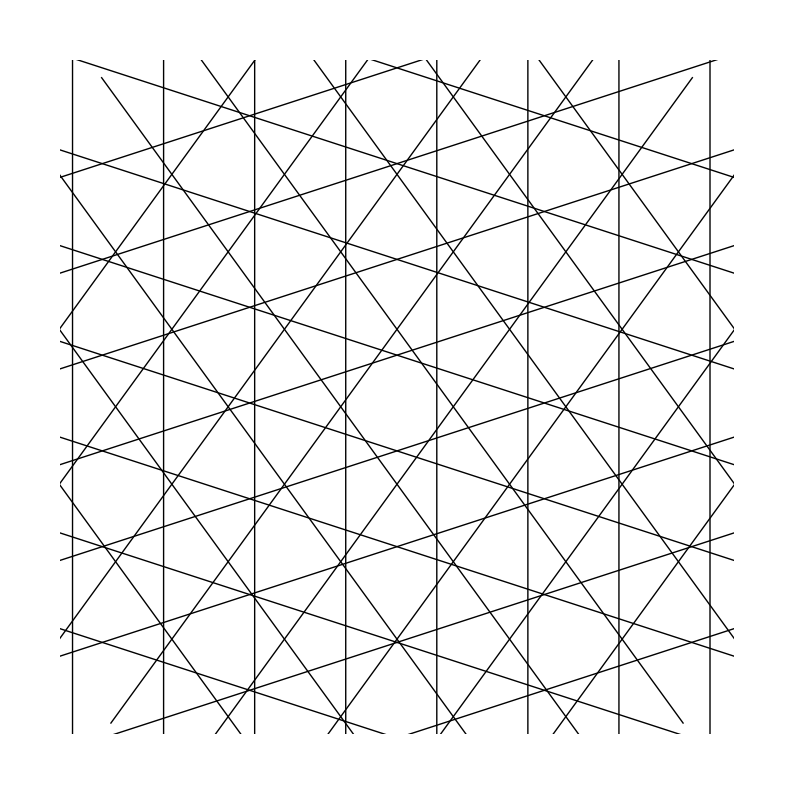

```mathematica
Show[Graphics@Line[Flatten[Table[Table[{RotationMatrix[Pi*i/5].({0.1,-2}+{g,0}),RotationMatrix[Pi*i/5].({0.1,2}+{g,0})},{g,-1.6,1.6,0.421}],{i,0,4}],1]],PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

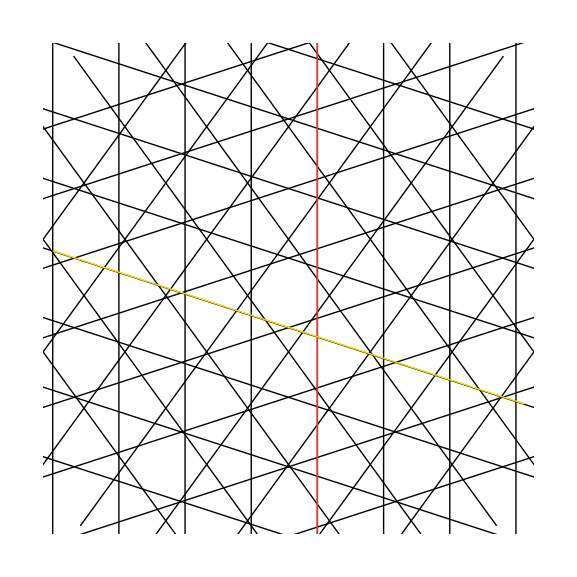

```mathematica
Show[Graphics@Line[Flatten[Table[Table[{RotationMatrix[Pi*i/5].({0.1,-2}+{g,0}),RotationMatrix[Pi*i/5].({0.1,2}+{g,0})},{g,-1.6,1.6,0.421}],{i,0,4}],1]],
Graphics[{NiceRed,Thick,Line[{{.1825,-2},{.1825,2}}]}],
Graphics[{NiceYellow,Thick,Line[{{1.5,-0.734},{-1.5,.24}}]}],
PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

```mathematica
Show[Graphics@Line[Flatten[Table[Table[{RotationMatrix[Pi*i/5].({0.1,-2}+{g,0}),RotationMatrix[Pi*i/5].({0.1,2}+{g,0})},{g,-1.6,1.6,0.421}],{i,0,4}],1]],
Graphics[{NiceRed,Thick,Line[{{.1825,-2},{.1825,2}}]}],
Graphics[{NiceYellow,Thick,Line[{{1.5,-0.734},{-1.5,.24}}]}],
PlotRange->{{-0.2,0.5},{-.7,.4}}]
```

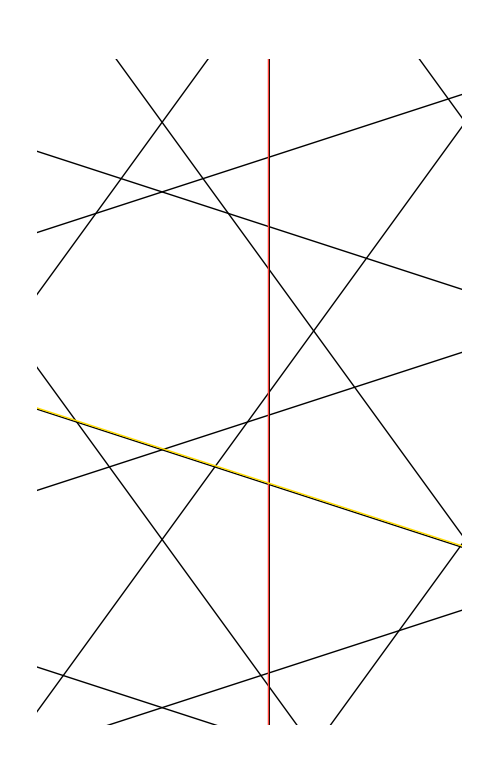

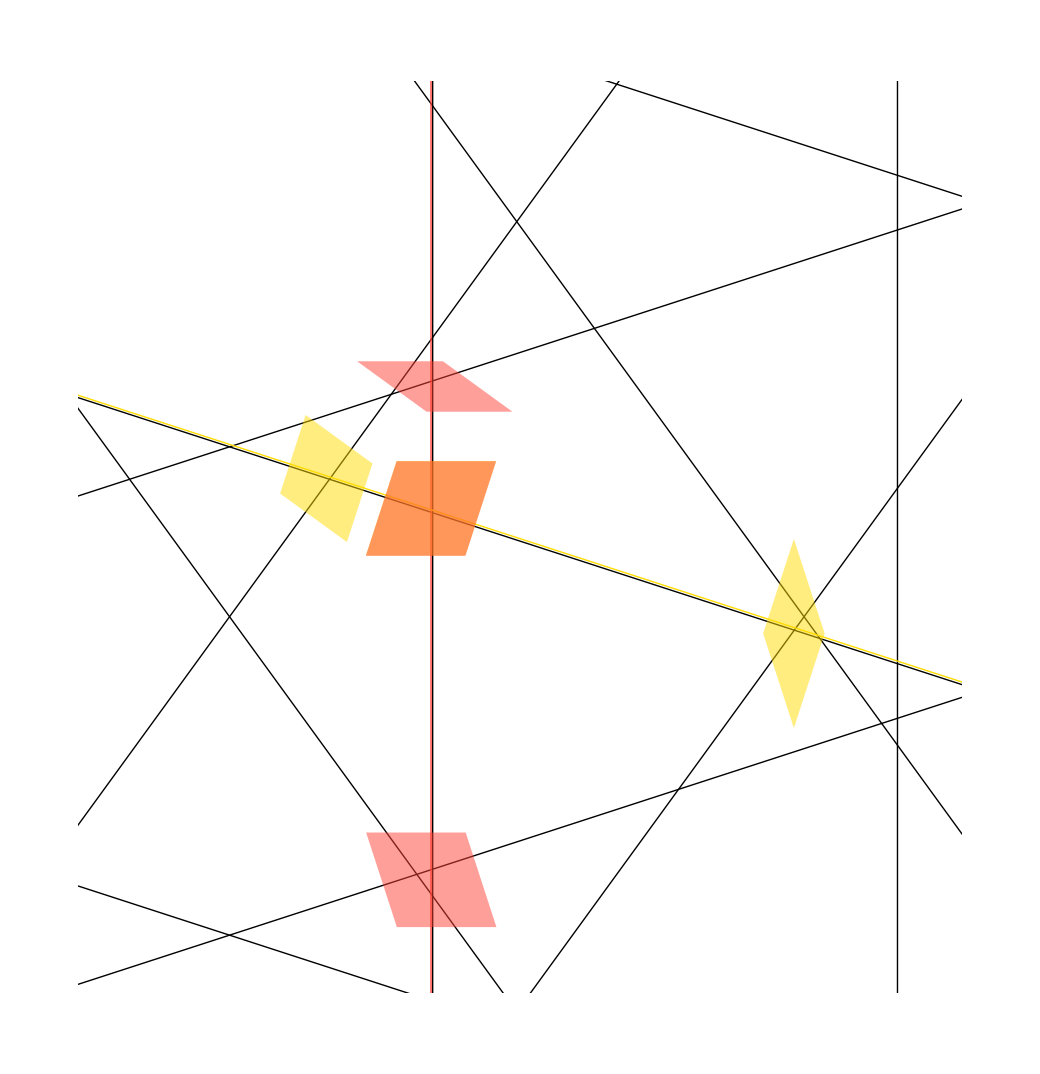

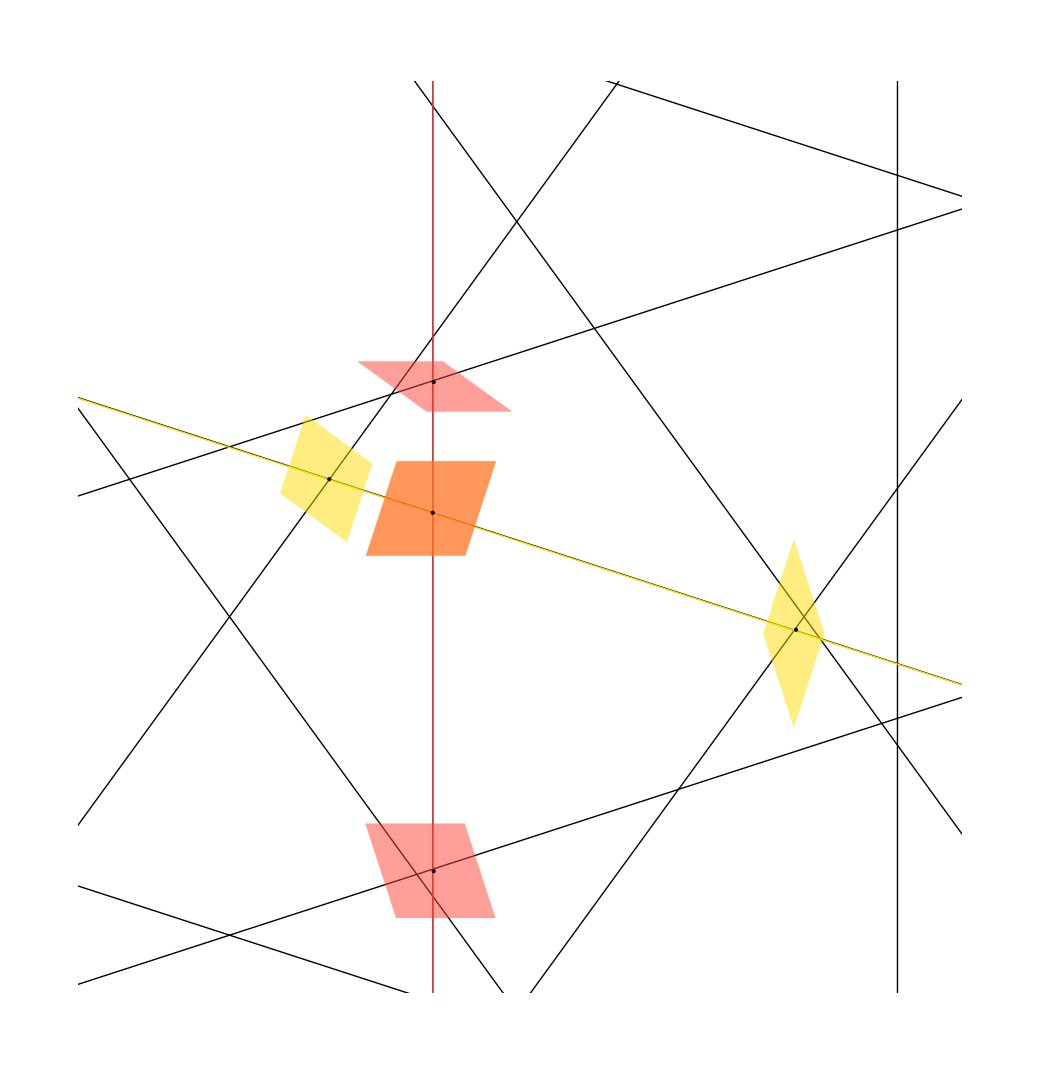

-Graphics-

```mathematica
Graphics[{NiceRed,Thick,Line[{{1.87,-2},{1.87,2}}]}]
```

-Graphics-

```mathematica
Hexagon[x_]:=Line[x+#&/@(Through[{Cos,Sin}[Pi#/3]]&/@Range[0,6])]

HexagonalGrid[x_,y_]:=Module[{i,j},
Table[Hexagon[{3/2i,Sqrt[3]j+Mod[i,2]Sqrt[3]/2}],{i,x},{j,y}]
]
```

```mathematica
Graphics[{Black,#}&/@Flatten[HexagonalGrid[7,7],1],
PlotRange->{{.7,10.2},{.7,10.2}}]
Export["Hexagons.png",%,Background->None]
```

-Graphics-

Hexagons.png

```mathematica
Show[Graphics@Line[Flatten[Table[Table[{RotationMatrix[Pi*i/3].({6,-20}+{g,0}),RotationMatrix[Pi*i/3].({6,20}+{g,0})},{g,-20,20,2}],{i,0,4}],1]],
Graphics[{Black,#}&/@Flatten[HexagonalGrid[7,7],1]],
PlotRange->{{1,10.2},{1,10.2}}]
```

-Graphics-

Graphics[List[GrayLevel[0],Line[List[List[7,Power[3,Rational[1,2]]],List[Rational[13,2],Times[Rational[3,2],Power[3,Rational[1,2]]]],List[Rational[11,2],Times[Rational[3,2],Power[3,Rational[1,2]]]],List[5,Power[3,Rational[1,2]]],List[Rational[11,2],Times[Rational[1,2],Power[3,Rational[1,2]]]],List[Rational[13,2],Times[Rational[1,2],Power[3,Rational[1,2]]]],List[7,Power[3,Rational[1,2]]]]]]]

```mathematica
Polygon
```

```mathematica
Show[Graphics[{FaceForm[None],EdgeForm[Black],Polygon[Table[{Cos[2π k/6],Sin[2π k/6]},{k,0,5}]]}],
Graphics[{PointSize@Large,NiceRed,Point[Table[{Cos[2π k/6],Sin[2π k/6]},{k,5,5}]]}]]
```

-Graphics-

```mathematica
Graphics[{FaceForm[None],EdgeForm[Black],Point[Table[{Cos[2π k/6],Sin[2π k/6]},{k,0,0}]]}]
```

-Graphics-

```mathematica
trigrid[x_,y_]:=Module[{i,j},
Table[tri[{3/2i,Sqrt[3]j+Mod[i,2]Sqrt[3]/2}],{i,x},{j,y}]
]
```

```mathematica
tripointsgrid[x_,y_]:=Module[{i,j},
Table[tripoints[{3/2i,Sqrt[3]j+Mod[i,2]Sqrt[3]/2}],{i,x},{j,y}]
]
```

```mathematica
HexagonPoint[x_]:=Point[x+#&/@(Through[{Cos,Sin}[Pi#/3]]&/@Range[0,6])]

HexagonalPointGrid[x_,y_]:=Module[{i,j},
Table[HexagonPoint[{3/2i,Sqrt[3]j+Mod[i,2]Sqrt[3]/2}],{i,x},{j,y}]
]
```

```mathematica
tri[x_]:=Line[x+#&/@(Through[{Cos,Sin}[2Pi#/3]]&/@Range[0,3])]
tripoints[x_]:=Point[x+#&/@(Through[{Cos,Sin}[2Pi#/3]]&/@Range[0,3])]
```

```mathematica
Show[Graphics[{NicePurple,Translate[trigrid[10,10],{3.5,0.5Sqrt[3]}]}],Graphics[{NiceBlue,PointSize@Large,Translate[tripointsgrid[10,10],{3.5,0.5Sqrt[3]}]}],Graphics@HexagonalGrid[10,10],Graphics[{NiceRed,PointSize@Medium,HexagonalPointGrid[10,10]}],ImageSize->Large]
QuickExport["HexagonDuals.png"]
```

-Graphics-

HexagonDuals.png

HexagonDuals.png

```mathematica
Show[Graphics@MapThread[{Thick,#1,#2}&,{{NiceOrange,NicePurple,NiceBlue},Map[Line,(Table[Table[{RotationMatrix[Pi*i/3].({0,-2}+{g,0}),RotationMatrix[Pi*i/3].({0,2}+{g,0})},{g,-2,2,0.5}],{i,0,2}])]}],
PlotRange->{{-1.5,1.5},{-1.5,1.5}},ImageSize->Large]
QuickExport["TriangleFamilies.png"]
```

-Graphics-

TriangleFamilies.png

```mathematica
Show[Graphics@MapThread[{Thick,#1,#2}&,{{NiceOrange,NicePurple,NiceBlue},Map[Line,(Table[Table[{RotationMatrix[Pi*i/3].({0,-2}+{g,0}),RotationMatrix[Pi*i/3].({0,2}+{g,0})},{g,-2,2,0.5}],{i,0,2}])]}],
Graphics[{FaceForm[None],EdgeForm[Black],Translate[Polygon[1/6Table[{Cos[2π k/6],Sin[2π k/6]},{k,0,5}]],Flatten[Table[Table[{0.5i,j 1/(2 √3)},{i,-2,2,2}],{j,-4,4,2}],1]]}],
Graphics[{FaceForm[None],EdgeForm[Black],Translate[Polygon[1/6Table[{Cos[2π k/6],Sin[2π k/6]},{k,0,5}]],Flatten[Table[Table[{0.5i,j 1/(2 √3)},{i,-3,3,2}],{j,-5,5,2}],1]]}],

Graphics[{Thick,NiceRed,Translate[Line[Table[1/6{Cos[2π k/6],Sin[2π k/6]},{k,0,1}]],{0,0}]}],
Graphics[{Thick,NiceRed,Translate[Line[Table[1/6{Cos[2π k/6],Sin[2π k/6]},{k,3,4}]],{0.5,1/(2 √3)}]}],

Graphics[{PointSize@Large,NiceRed,Translate[Point[Table[1/6{Cos[2π k/6],Sin[2π k/6]},{k,5,5}]],{0,0}]}],
Graphics[{PointSize@Large,NiceRed,Translate[Point[Table[1/6{Cos[2π k/6],Sin[2π k/6]},{k,1,1}]],{0,-2 1/(2 √3)}]}],
Graphics[{PointSize@Large,NiceRed,Translate[Point[Table[1/6{Cos[2π k/6],Sin[2π k/6]},{k,3,3}]],{0.5,-1/(2 √3)}]}],
PlotRange->{{-1.5,1.5},{-1.5,1.5}},ImageSize->Large]
QuickExport["HexagonDualSmall.png"]
```

-Graphics-

HexagonDualSmall.png

HexagonDualSmall.png

```mathematica
Flatten[Table[Table[{0.5i,j 1/(2 √3)},{i,-2,2,2}],{j,-2,2,1}],1]
```

{{-1.,-1/(√3)},{0.,-1/(√3)},{1.,-1/(√3)},{-1.,-1/(2 √3)},{0.,-1/(2 √3)},{1.,-1/(2 √3)},{-1.,0},{0.,0},{1.,0},{-1.,1/(2 √3)},{0.,1/(2 √3)},{1.,1/(2 √3)},{-1.,1/(√3)},{0.,1/(√3)},{1.,1/(√3)}}

```mathematica
Im[Sqrt[3]/3*Exp[I Pi/6]]
```

1/(2 √3)

```mathematica
Dimensions[%406]
```

{5,9,2,2}

```mathematica
Show[Graphics@MapThread[{#1,#2}&,{{NiceOrange,NicePurple,NiceBlue,NiceRed,NiceGreen},Map[Line,(Table[Table[{RotationMatrix[Pi*i/5].({0.1,-2}+{g,0}),RotationMatrix[Pi*i/5].({0.1,2}+{g,0})},{g,-1.6,1.6,0.821}],{i,0,4}])]}],

Show[Graphics[{Thick,Arrow[Table[{{0,0},1/0.821{Cos[i 2Pi/5],Sin[i 2Pi/5]}},{i,0,4}]]}],
Graphics@Table[Table[Text[Style[Subscript["ϵ⃗",ToString@i],30,FontFamily->"CMU Serif"],1/2*{Cos[i 2Pi/5+0.2],Sin[i 2Pi/5+0.2]}],{i,0,4}],{i,0,4}]],
PlotRange->{{-1.5,1.5},{-1.5,1.5}},ImageSize->Large]
QuickExport["RegularPentagrid.png"]
```

-Graphics-

RegularPentagrid.png

```mathematica
Show[Graphics@MapThread[{#1,#2}&,{{NiceOrange,NicePurple,NiceBlue,NiceRed,NiceGreen},Map[Line,(Table[Table[{RotationMatrix[Pi*i/5].({0.1,-2}+{g,0}),RotationMatrix[Pi*i/5].({0.1,2}+{g,0})},{g,-1.6,1.6,0.75}],{i,0,4}])]}],
Graphics[{Thick,Arrow[Table[{{0,0},1/0.75*{Cos[i 2Pi/5],Sin[i 2Pi/5]}},{i,0,4}]]}],
Graphics@Table[Table[Text[Style[Subscript["ϵ⃗",ToString@i],30,FontFamily->"CMU Serif"],1/2*{Cos[i 2Pi/5+0.2],Sin[i 2Pi/5+0.2]}],{i,0,4}],{i,0,4}],
PlotRange->{{-1.5,1.5},{-1.5,1.5}},ImageSize->Large]
QuickExport["SingularPentagrid.png"]
```

-Graphics-

SingularPentagrid.png

SingularPentagrid.png

```mathematica
Show[Graphics@Arrow[Table[{{0,0},{Cos[i 2Pi/5],Sin[i 2Pi/5]}},{i,0,4}]],
Graphics@Table[Table[Text[Style[Subscript["ϵ⃗",ToString@i],30,FontFamily->"CMU Serif"],1/2*{Cos[i 2Pi/5+0.2],Sin[i 2Pi/5+0.2]}],{i,0,4}],{i,0,4}]]
QuickExport["RootsUnity.png"]
```

-Graphics-

RootsUnity.png

```mathematica
Table[{{0,0},{Cos[i Pi/5],Sin[i Pi/5]}},{i,0,4}]
```

{{{0,0},{1,0}},{{0,0},{1/4 (1+√5),√(5/8-(√5)/8)}},{{0,0},{1/4 (-1+√5),√(5/8+(√5)/8)}},{{0,0},{1/4 (1-√5),√(5/8+(√5)/8)}},{{0,0},{1/4 (-1-√5),√(5/8-(√5)/8)}}}

```mathematica
subscript
```

```mathematica
Graphics@Table[Text[Subscript["ϵ⃗",ToString@i],1/2*{Cos[i 2Pi/5],Sin[i 2Pi/5]}],{i,0,4}]
```

```mathematica
-Graphics-Style[ToString@Subscript["ϵ⃗",ToString@i],1/2*{Cos[i 2Pi/5+0.1],Sin[i 2Pi/5+0.1]}],Red]
```

```mathematica
Style[ToString@Subscript["ϵ⃗",ToString@i],1/2*{Cos[i 2Pi/5+0.1],Sin[i 2Pi/5+0.1]},Red]
```

Style[⇀
ϵ
 i,{1/2 Cos[0.1+(2 i π)/5],1/2 Sin[0.1+(2 i π)/5]},-Graphics-]

{Text[(ϵ⃗)_0,{0.497502,0.0499167}],Text[(ϵ⃗)_1,{0.106263,0.488578}],Text[(ϵ⃗)_2,{-0.431828,0.252041}],Text[(ϵ⃗)_3,{-0.373147,-0.332808}],Text[(ϵ⃗)_4,{0.20121,-0.457727}]}

```mathematica
/.i->1
```

(ϵ⃗)_i

```mathematica
Graphics@Line[Flatten[Table[Table[{RotationMatrix[1Pi*i/5].({-1,0}+{g,0}),RotationMatrix[1Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,0,1}],1]]
QuickExport["Intersection1.png"]
```

-Graphics-

Intersection1.png

```mathematica
Graphics@Line[Flatten[Table[Table[{RotationMatrix[2Pi*i/5].({-1,0}+{g,0}),RotationMatrix[2Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,0,1}],1]]
QuickExport["Intersection2.png"]
```

-Graphics-

Intersection2.png

```mathematica
{{Graphics[1]}, {{{, , , , }}}}
QuickExport["RhombRibbons.png"]
```

-Graphics-

RhombRibbons.png

```mathematica
Show[Graphics@Line[Flatten[Table[Table[{RotationMatrix[Pi*2i/5].({0.1,-2}+{g,0}),RotationMatrix[Pi*2i/5].({0.1,2}+{g,0})},{g,1,1}],{i,2,3}],1]],PlotRange->{{-2,-.7},{-0.9,0.9}}]
```

-Graphics-

```mathematica
Show[Graphics[{Thick,Line[Flatten[Table[Table[{RotationMatrix[1Pi*i/5].({-1,0}+{g,0}),RotationMatrix[1Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,0,1}],1]]}],
Graphics[{Opacity[0.7],FaceForm[NiceYellow],Scale[Rotate[Rotate[Polygon/@Coor/@Δ/@FullInflate[{unitskinny},0],Pi/2],3Pi/5],0.5]}]]
QuickExport["ThinIntersection.png"]

Show[Graphics[{Thick,Line[Flatten[Table[Table[{RotationMatrix[2Pi*i/5].({-1,0}+{g,0}),RotationMatrix[2Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,0,1}],1]]}],
Graphics[{Opacity[0.7],FaceForm[NicePurple],Rotate[Rotate[Polygon/@Coor/@Δ/@FullInflate[{unitfat},0],Pi/2],Pi/5]}]
]
QuickExport["ThickIntersection.png"]
```

-Graphics-

ThinIntersection.png

-Graphics-

ThickIntersection.png

```mathematica
Show[Graphics[{Thick,Line[Flatten[Table[Table[{RotationMatrix[2Pi*i/5].({-1,0}+{g,0}),RotationMatrix[2Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,0,1}],1]]}],
Graphics[{NiceRed,Arrow[Flatten[Table[Table[{(({0,0}+{g,0})),RotationMatrix[Pi/2].RotationMatrix[2Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,{0}}],1]]}],
Graphics[{NicePurple,Arrow[Flatten[Table[Table[{(({0,0}+{g,0})),RotationMatrix[Pi].RotationMatrix[Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,{2.5}}],1]]}],

Graphics[{NiceGreen,Arrow[Flatten[Table[Table[{(({0,0}+{g,0})),RotationMatrix[Pi/2].RotationMatrix[2Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,{1}}],1]]}],
Graphics[{NiceBlue,Arrow[Flatten[Table[Table[{(({0,0}+{g,0})),RotationMatrix[Pi].RotationMatrix[Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,{4.5}}],1]]}]]
QuickExport["Intersection2Norms.png"]
```

-Graphics-

Intersection2Norms.png

```mathematica
Show[Graphics[{Thick,Line[Flatten[Table[Table[{RotationMatrix[1Pi*i/5].({-1,0}+{g,0}),RotationMatrix[1Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,0,1}],1]]}],
Graphics[{NiceRed,Arrow[Flatten[Table[Table[{(({0,0}+{g,0})),RotationMatrix[Pi/2].RotationMatrix[Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,{0}}],1]]}],
Graphics[{NicePurple,Arrow[Flatten[Table[Table[{(({0,0}+{g,0})),RotationMatrix[Pi].RotationMatrix[Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,{2.5}}],1]]}],
Graphics[{NiceGreen,Arrow[Flatten[Table[Table[{(({0,0}+{g,0})),RotationMatrix[Pi/2].RotationMatrix[Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,{1}}],1]]}],
Graphics[{NiceBlue,Arrow[Flatten[Table[Table[{(({0,0}+{g,0})),RotationMatrix[Pi].RotationMatrix[Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,{3.5}}],1]]}]]
QuickExport["Intersection1Norms.png"]
```

-Graphics-

Intersection1Norms.png

```mathematica
Show[
Graphics[{Thick,NicePurple,Line[{{-0.5,0},{0.,1.5388417685876268}}]}],
Graphics[{Thick,NiceGreen,Line[{{-0.5,0},{0.,-1.5388417685876268}}]}],
Graphics[{Thick,NiceBlue,Line[{{0.5,0},{0.,1.5388417685876268}}]}],
Graphics[{Thick,NiceRed,Line[{{0.5,0},{0.,-1.5388417685876268}}]}]]
QuickExport["ColouredSkinnyRhomb.png"]
```

-Graphics-

ColouredSkinnyRhomb.png

```mathematica
Coor/@Δ/@FullInflate[{unitfat},0]
```

{{{-0.809017,0},{-1.11022×10^-16,0.587785},{0.809017,0},{1.11022×10^-16,-0.587785}}}

```mathematica
Show[
Graphics[{Thick,NicePurple,Line[{{0.8090169943749475,0},{1.1102230246251565*^-16,-0.5877852522924732}}]}],
Graphics[{Thick,NiceGreen,Line[{{-0.8090169943749475,0},{1.1102230246251565*^-16,-0.5877852522924732}}]}],
Graphics[{Thick,NiceBlue,Line[{{0.8090169943749475,0},{-1.1102230246251565*^-16,0.5877852522924732}}]}],
Graphics[{Thick,NiceRed,Line[{{-0.8090169943749475,0},{-1.1102230246251565*^-16,0.5877852522924732}}]}]]
QuickExport["ColouredFatRhomb.png"]
```

-Graphics-

ColouredFatRhomb.png

```mathematica
Show[Graphics[{Opacity[0.7],FaceForm[NicePurple],Polygon/@Coor/@Δ/@FullInflate[{unitfat},0]}],
Graphics[MakeCurveRules/@Inflate[AddConj@{unitfat},0]]]
```

-Graphics-

-Graphics-

```mathematica
Graphics[Rotate[MakeCurveRules/@Inflate[AddConj@{unitfat},0],Pi/2]]
```

-Graphics-

```mathematica
FullInflate[{unitfat},0]
```

{{{-0.809017,-1.11022×10^-16+0.587785 ⅈ,0.809017,1.11022×10^-16-0.587785 ⅈ},fat}}

```mathematica
Show[SeeFaded@FullInflate[{unitskinny},0],SeeFadedEdges@FullInflate[{unitskinny},0]]
```

-Graphics-

```mathematica
ShiftVectors={-0.9,-0.3,0,0.3,0.9};
Show[Graphics@MapThread[{#1,#2}&,{{NiceOrange,NicePurple,NiceBlue,NiceRed,NiceGreen},(Table[Translate[Map[Line,Table[{RotationMatrix[Pi*i/5].({0,-2}+{g,0}),RotationMatrix[Pi*i/5].({0,2}+{g,0})},{g,-5,5,1}]],{Re[ShiftVectors[[i+1]]Exp[i 2Pi I/5]],Im[ShiftVectors[[i+1]]Exp[i 2Pi I/5]]}],{i,0,4}])}],

Show[Graphics[{Thick,Arrow[Table[{{0,0},{Cos[i 2Pi/5],Sin[i 2Pi/5]}},{i,0,4}]]}],
Graphics@Table[Table[Text[Style[Subscript["ϵ⃗",ToString@i],30,FontFamily->"CMU Serif"],1/2*{Cos[i 2Pi/5+0.2],Sin[i 2Pi/5+0.2]}],{i,0,4}],{i,0,4}]],
PlotRange->{{-1.5,1.5},{-1.5,1.5}},ImageSize->Large]
QuickExport["RegularPentagrid.png"]
```

-Graphics-

RegularPentagrid.png

```mathematica
Total@Table[g,{g,-2,2,1}]
```

0

```mathematica
Total[{-1.6,-0.7790000000000001,0.041999999999999815,0.863}]
```

-1.474

```mathematica
Show[Graphics@MapThread[{#1,#2}&,{{NiceOrange,NicePurple,NiceBlue,NiceRed,NiceGreen},Map[Line,(Table[Table[{RotationMatrix[Pi*i/5].({0,-2}+{g,0}),RotationMatrix[Pi*i/5].({0,2}+{g,0})},{g,-1,1,0.1}],{i,0,4}])]}]]
```

-Graphics-

```mathematica
Table[Table[{(RotationMatrix[Pi*i/5].({0,-2}+{g,0}))+RotationMatrix[Pi i/5].ShiftVectors[[i+1]],(RotationMatrix[Pi*i/5].({0,2}+{g,0}))++},{g,1,1,1}],{i,0,4}]
```

```mathematica
{-1,-0.3,0,0.3,1}
```

{-1.,-0.3,0,0.3,1.}

```mathematica
ShiftVectors={4,0,-2,-2,0}
Graphics@Table[Translate[Map[Line,Table[{RotationMatrix[Pi*i/5].({0,-5}+{g,0}),RotationMatrix[Pi*i/5].({0,5}+{g,0})},{g,0,0,1}]],{Re[ShiftVectors[[i+1]]Exp[i 2Pi I/5]],Im[ShiftVectors[[i+1]]Exp[i 2Pi I/5]]}],{i,0,4}]
```

{4,0,-2,-2,0}

-Graphics-

```mathematica
Manipulate[Graphics@Table[Translate[Map[Line,Table[{RotationMatrix[Pi*i/5].({0,-5}+{g,0}),RotationMatrix[Pi*i/5].({0,5}+{g,0})},{g,0,0,1}]],{Re[{a,b,c,d,e}[[i+1]]Exp[i 2Pi I/5]],Im[{a,b,c,d,e}[[i+1]]Exp[i 2Pi I/5]]}],{i,0,4}],{a,-2,2},{b,-2,2},{c,-2,2},{d,-2,2},{e,-2,2}]
```

```mathematica
??SeeFaded
```

Global`SeeFaded

SeeFaded:=Graphics[{Opacity[0.3],Transpose[{((IfFat[#1,NicePurple,NiceYellow]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}]&

```mathematica
Show[Graphics[{Thick,Line[Flatten[Table[Table[{RotationMatrix[1Pi*i/5].({-1,0}+{g,0}),RotationMatrix[1Pi*i/5].({1,0}+{g,0})},{g,0,0}],{i,0,1}],1]]}],Graphics[{Opacity[0.7],Transpose[{((IfFat[#1,NicePurple,NiceYellow]&)/@#1&)[#1],Scale[#,0.25]&@Rotate[#,Pi/10]&/@Polygon/@Coor/@Δ/@#1}]}]&@FullInflate[{unitskinny},0]]
```

-Graphics-

```mathematica
Graphics[{Opacity[0.7],Transpose[{((IfFat[#1,NicePurple,NiceYellow]&)/@#1&)[#1],Scale[#,0.25]&@Rotate[#,Pi/10]&/@Polygon/@Coor/@Δ/@#1}]}]&@FullInflate[{unitskinny},0]
```

```mathematica
ShiftVectors={4,0,-2,-2,0}
Graphics@Table[Translate[Map[Line,Table[{RotationMatrix[Pi*i/5].({0,-5}+{g,0}),RotationMatrix[Pi*i/5].({0,5}+{g,0})},{g,0,0,1}]],{Re[ShiftVectors[[i+1]]Exp[i 2Pi I/5]],Im[ShiftVectors[[i+1]]Exp[i 2Pi I/5]]}],{i,0,4}]
QuickExport["PentagridConstruct.png"]
```

{4,0,-2,-2,0}

-Graphics-

PentagridConstruct.png

```mathematica
-Graphics-//FullForm
```

```mathematica
Graphics[List[GeometricTransformation[Line[List[List[0,-5],List[0,5]]],List[4,0]],GeometricTransformation[Line[List[List[Times[Rational[5,2],Power[Times[Rational[1,2],Plus[5,Times[-1,Power[5,Rational[1,2]]]]],Rational[1,2]]],Times[Rational[-5,4],Plus[1,Power[5,Rational[1,2]]]]],List[Times[Rational[-5,2],Power[Times[Rational[1,2],Plus[5,Times[-1,Power[5,Rational[1,2]]]]],Rational[1,2]]],Times[Rational[5,4],Plus[1,Power[5,Rational[1,2]]]]]]],List[0,0]],GeometricTransformation[Line[List[List[Times[Rational[5,2],Power[Times[Rational[1,2],Plus[5,Power[5,Rational[1,2]]]],Rational[1,2]]],Times[Rational[-5,4],Plus[-1,Power[5,Rational[1,2]]]]],List[Times[Rational[-5,2],Power[Times[Rational[1,2],Plus[5,Power[5,Rational[1,2]]]],Rational[1,2]]],Times[Rational[5,4],Plus[-1,Power[5,Rational[1,2]]]]]]],List[Times[-2,Re[Power[E,Times[Complex[0,Rational[4,5]],Pi]]]],Times[-2,Im[Power[E,Times[Complex[0,Rational[4,5]],Pi]]]]]],GeometricTransformation[Line[List[List[Times[Rational[5,2],Power[Times[Rational[1,2],Plus[5,Power[5,Rational[1,2]]]],Rational[1,2]]],Times[Rational[-5,4],Plus[1,Times[-1,Power[5,Rational[1,2]]]]]],List[Times[Rational[-5,2],Power[Times[Rational[1,2],Plus[5,Power[5,Rational[1,2]]]],Rational[1,2]]],Times[Rational[5,4],Plus[1,Times[-1,Power[5,Rational[1,2]]]]]]]],List[Times[-2,Re[Power[E,Times[Complex[0,Rational[-4,5]],Pi]]]],Times[-2,Im[Power[E,Times[Complex[0,Rational[-4,5]],Pi]]]]]],GeometricTransformation[Line[List[List[Times[Rational[5,2],Power[Times[Rational[1,2],Plus[5,Times[-1,Power[5,Rational[1,2]]]]],Rational[1,2]]],Times[Rational[-5,4],Plus[-1,Times[-1,Power[5,Rational[1,2]]]]]],List[Times[Rational[-5,2],Power[Times[Rational[1,2],Plus[5,Times[-1,Power[5,Rational[1,2]]]]],Rational[1,2]]],Times[Rational[5,4],Plus[-1,Times[-1,Power[5,Rational[1,2]]]]]]]],List[0,0]],List[Opacity[0.7],List[RGBColor[1.,0.8627450980392157,0.],GeometricTransformation[Polygon[List[List[-0.4020772414084258,0.08748494703705845],List[0.09792275859157423,1.6263267156246852],List[0.597922758591574,0.08748494703705845],List[0.0979227585915739,-1.4513568215505683]]],List[List[List[List[0.4503502062995741,-0.3382827244446445],List[0.3382827244446447,0.45035020629957423]],List[0.6299616142594655,0.7951093939139189]]]]]],List[Opacity[0.7],List[RGBColor[1.,0.8627450980392157,0.],GeometricTransformation[Polygon[List[List[-0.890426178094155,-0.08597644903816531],List[-0.39042617809415514,1.4528653195494614],List[0.10957382190584475,-0.08597644903816543],List[-0.39042617809415514,-1.6248182176257921]]],List[List[List[List[0.4664782486448106,0.31567159123530675],List[-0.3156715912353068,0.4664782486448106]],List[0.8352843361383749,-0.9965937219973476]]]]]],List[Opacity[0.7],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[-0.7945121060734004,0.03626222075387364],List[0.014504888301547059,0.6240474730463469],List[0.8235218826764945,0.03626222075387364],List[0.014504888301547059,-0.5515230315385996]]]]],List[Opacity[0.7],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[3.342244069041266,2.427811222858209],List[4.342172267126364,2.4158279564300247],List[4.639770309866353,1.4611366948394893],List[3.639842111781255,1.4731199612676735]]]]],List[Opacity[0.7],List[RGBColor[0.6941176470588235,0.050980392156862744,0.788235294117647],Polygon[List[List[4.648210402620274,-1.4995325611324661],List[4.334993873694138,-2.4492143004575224],List[3.33500363674522,-2.4447954763099724],List[3.648220165671356,-1.4951137369849152]]]]]],Rule[ImagePadding,List[List[0.,1.111111],List[1.111111,0.]]],Rule[ImageSize,List[759.9999999999995,Automatic]],Rule[PlotRange,List[List[-3.3353853669540294,6.571453344453819],List[-5.190211303259031,5.190211303259031]]],Rule[PlotRangePadding,Automatic]]
QuickExport["RhombPlacement.png"]
```

-Graphics-

RhombPlacement.png

RhombPlacement.png

```mathematica
See@FullInflate[{unitfat},1]
QuickExport["RhombConstructed.png"]
```

-Graphics-

RhombConstructed.png

```mathematica
Graphics[{Opacity[0.7],Transpose[{((IfFat[#1,NicePurple,NiceYellow]&)/@#1&)[#1],Scale[#,1]&/@Polygon/@Coor/@Δ/@#1}]}]&@FullInflate[{unitskinny},0]
Graphics[{Opacity[0.7],Transpose[{((IfFat[#1,NicePurple,NiceYellow]&)/@#1&)[#1],Polygon/@Coor/@Δ/@#1}]}]&@FullInflate[{unitfat},0]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
tiling=FullInflate[starseed,5];
pathtris=Midpoints/@MakePathTriangles@tiling;
Show[See@(tiling),SeeTri/@pathtris]
```

-Graphics-

```mathematica
Length@pathtris
```

1490

```mathematica
Show[See@tiling,Graphics[{NiceBlue,Thick,#}]&/@GeneratePath[{pathtris,56,3,1}],Graphics[{Thick,Green,Point[Coor@{pathtris[[56,3]]}]}]]
Table[Show[SeeEdges@tiling,Graphics[{NiceRed,Thick,#}]&/@GeneratePath[{pathtris,i,j,k}],Graphics[{Thick,Green,Point[Coor@{pathtris[[56,3]]}]}]],{i,1, Length@pathtris},{j,1,3},{k,{-1,1}}]
```

-Graphics-

```mathematica
tiling=FullInflate[starseed,6];
pathtris=Midpoints/@MakePathTriangles@tiling;
Show[SeeEdges@tiling,Graphics[{NiceRed,Thick,#}]&/@GeneratePath[{pathtris,1490,3,-1}],
Show[SeeEdges@tiling,Graphics[{NiceRed,Thick,#}]&/@GeneratePath[{pathtris,1490,2,1}]]]
```

```mathematica
-Graphics-
QuickExport["FlowerPart.png"]
```

-Graphics-

FlowerPart.png

```mathematica
-Graphics-
QuickExport["Peanut.png"]
```

-Graphics-

Peanut.png

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-]
```

```mathematica
-Graphics-
QuickExport["Chains.png"]
```

-Graphics-

Chains.png

```mathematica
Show[-Graphics-,-Graphics-]
```

```mathematica
-Graphics-
QuickExport["Rings.png"]
```

-Graphics-

Rings.png

```mathematica
tiling=FullInflate[starseed,3];
pathtris=Midpoints/@MakePathTriangles@tiling;
Show[SeeEdges@tiling,
Graphics[{NiceRed,Thick,#}]&/@GeneratePath[{pathtris,1,3,-1}],
Graphics[{EdgeForm[Gray],FaceForm[None],Polygon[Coor[#]]}]&/@pathtris,
Graphics[{PointSize@Large,Green,Point[Coor@{pathtris[[1,3]]}]}]]
QuickExport["Geodesic.png"]
```

-Graphics-

Geodesic.png

```mathematica
Show[SeeEdges@tiling]
```

```mathematica
-Graphics-
QuickExport["PathRhombsRegion.png"]
```

-Graphics-

PathRhombsRegion.png

```mathematica
Show[SeeEdges@tiling,
Graphics[{EdgeForm[Gray],FaceForm[None],Polygon[Coor[#]]}]&/@pathtris]
```

```mathematica
-Graphics-
QuickExport["InscribedMesh.png"]
```

-Graphics-

InscribedMesh.png

```mathematica
Show[SeeEdges@tiling,
Graphics[{EdgeForm[Gray],FaceForm[None],Polygon[Coor[#]]}]&/@pathtris,
Graphics[{PointSize@Large,Green,Point[Coor@{pathtris[[1,3]]}]}]]
```

```mathematica
-Graphics-
QuickExport["PathStart.png"]
```

-Graphics-

PathStart.png

```mathematica
Show[SeeEdges@tiling,
Graphics[{NiceRed,Thick,#}]&/@{GeneratePath[{pathtris,1,3,-1}][[1]]},
Graphics[{EdgeForm[Gray],FaceForm[None],Polygon[Coor[#]]}]&/@pathtris,
Graphics[{PointSize@Large,Green,Point[Coor@{pathtris[[1,3]]}]}]]
```

```mathematica
-Graphics-
QuickExport["FirstStep.png"]
```

-Graphics-

FirstStep.png

```mathematica
Show[SeeEdges@tiling,
Graphics[{NiceRed,Thick,#}]&/@{GeneratePath[{pathtris,1,3,-1}][[1;;2]]},
Graphics[{NiceBlue,Thick,#}]&/@{GeneratePath[{pathtris,1,3,-1}][[2]]},
Graphics[{NiceOrange,Thick,#}]&/@{GeneratePath[{pathtris,2,2,-1}][[1]]},
Graphics[{EdgeForm[Gray],FaceForm[None],Polygon[Coor[#]]}]&/@pathtris,
Graphics[{PointSize@Large,Green,Point[Coor@{pathtris[[1,3]]}]}],
Graphics[{PointSize@Large,Teal,Point[Coor@{pathtris[[2,2]]}]}]]
```

```mathematica
-Graphics-
QuickExport["NextStep.png"]
```

-Graphics-

NextStep.png

-Graphics-

NextStep.png

```mathematica
pathtris[[1,2]]
```

-1.42705+0. ⅈ

```mathematica
Position[pathtris,-1.4270509831248424+0. ⅈ]
```

{{1,2},{2,2}}

```mathematica
-Graphics-
QuickExport["RightStep.png"]
```

-Graphics-

RightStep.png

```mathematica
??SeeTri
```

PenroseTilingFunctions`SeeTri

SeeTri[points_]:=Graphics[Polygon[Coor[points]]]